```mathematica
Quit[]
```

```mathematica
-9(n-1)/(n-2)(1+w)(n/(2(n-2))(1+w)-1)/.{w->1/3,n->16}//N
```

3.06122

```mathematica
(13+18)/2//N
```

15.5

```mathematica
ρ[h_]=Integrate[1/Sqrt[1+ξ h^2],h]
```

ArcSinh[h √ξ]/(√ξ)

```mathematica
h[ρ_]=1/Sqrt[ξ] Sinh[Sqrt[ξ]ρ]
```

Sinh[√ξ ρ]/(√ξ)

```mathematica
Simplify[ρ[h[ρ]],{ξ>0,ρ>0}]
```

ρ

```mathematica
h[ρ]^2/(1+ξ h[ρ]^2)//Simplify
```

Tanh[√ξ ρ]^2/ξ

```mathematica
Normal[Series[x^2/(1+ξ (x/Mpl)^2)/.{x->Mpl/Sqrt[ξ] E^(((1+ϵ)y0)/(Sqrt[6]Mpl))x0/(Mpl/Sqrt[ξ] E^(y0/Sqrt[6]/Mpl))},{ϵ,0,6},{ξ,∞,2}]]/.{ϵ->dy/y0}
```

-dy^4/(54 x0^2 ξ^2)-dy^6/(2430 Mpl^2 x0^2 ξ^2)+dy^5/(135 √6 Mpl x0^2 ξ^2)+(√(2/3) dy^3 Mpl)/(9 x0^2 ξ^2)-(dy^2 Mpl^2)/(3 x0^2 ξ^2)+(√(2/3) dy Mpl^3)/(x0^2 ξ^2)-Mpl^4/(x0^2 ξ^2)+Mpl^2/ξ

```mathematica
Normal[Series[x^2/(1+ξ (x/Mpl)^2),{x,0,6},{ξ,∞,2}]]
```

x^2-(x^4 ξ)/Mpl^2+(x^6 ξ^2)/Mpl^4

### covariant gauge

```mathematica
$Assumptions={x1>0,x2>0,x3>0,x4>0,dx1>0,dx2>0,dx3>0,dx4>0,B>0,A1>0,A2>0,A3>0,g>0,gp>0,h1>0,h2>0,h3>0,h4>0}
```

{x1>0,x2>0,x3>0,x4>0,dx1>0,dx2>0,dx3>0,dx4>0,B>0,A1>0,A2>0,A3>0,g>0,gp>0,h1>0,h2>0,h3>0,h4>0}

```mathematica
t1={{0,1},{1,0}};
t2={{0,-I},{I,0}};
t3={{1,0},{0,-1}};
```

```mathematica
t1.t2+t2.t1
t2.t3+t3.t2
t3.t1+t1.t3
```

{{0,0},{0,0}}

{{0,0},{0,0}}

{{0,0},{0,0}}

```mathematica
t1.t1
t2.t2
t3.t3
```

{{1,0},{0,1}}

{{1,0},{0,1}}

{{1,0},{0,1}}

```mathematica
X=1/Sqrt[2]{{x1+I x2},{x3+I x4}};
dX=1/Sqrt[2]{{dx1+I dx2},{dx3+I dx4}};
```

```mathematica
Simplify[Conjugate[Transpose[X]].X]
```

{{1/2 (x1^2+x2^2+x3^2+x4^2)}}

```mathematica
DX=dX+(-I/2 gp B{{1,0},{0,1}}-I g 1/2 t1 A1-I g 1/2 t2 A2-I g 1/2 t3 A3).X
```

{{(dx1+ⅈ dx2)/(√2)+((-1/2 ⅈ A3 g-(ⅈ B gp)/2) (x1+ⅈ x2))/(√2)+((-1/2 ⅈ A1 g-(A2 g)/2) (x3+ⅈ x4))/(√2)},{(dx3+ⅈ dx4)/(√2)+((-1/2 ⅈ A1 g+(A2 g)/2) (x1+ⅈ x2))/(√2)+(((ⅈ A3 g)/2-(ⅈ B gp)/2) (x3+ⅈ x4))/(√2)}}

```mathematica
kin=-Collect[FullSimplify[Conjugate[Expand[Transpose[DX]]]].DX//Expand,{gp,g,B,A1,A2},Simplify][[1,1]]
```

1/2 (-dx1^2-dx2^2-dx3^2-dx4^2)-1/8 B^2 gp^2 (x1^2+x2^2+x3^2+x4^2)-g (1/2 A1 (-dx4 x1+dx3 x2-dx2 x3+dx1 x4)+1/2 A2 (dx3 x1+dx4 x2-dx1 x3-dx2 x4)+1/2 A3 (-dx2 x1+dx1 x2+dx4 x3-dx3 x4))-g^2 (1/8 A1^2 (x1^2+x2^2+x3^2+x4^2)+1/8 A2^2 (x1^2+x2^2+x3^2+x4^2)+1/8 A3^2 (x1^2+x2^2+x3^2+x4^2))-gp (1/2 B (-dx2 x1+dx1 x2-dx4 x3+dx3 x4)+B g (1/2 A2 (-x2 x3+x1 x4)+1/2 A1 (x1 x3+x2 x4)+1/4 A3 (x1^2+x2^2-x3^2-x4^2)))

```mathematica
Conjugate[Transpose[X]].t1.X//Simplify
Conjugate[Transpose[X]].t2.X//Simplify
Conjugate[Transpose[X]].t3.X//Simplify
```

{{x1 x3+x2 x4}}

{{-x2 x3+x1 x4}}

{{1/2 (x1^2+x2^2-x3^2-x4^2)}}

### Higgs metric

```mathematica
Clear[coord,metric,inversemetric,affine,riemann,ricci,acalar,einstein,r,θ,ϕ,t]
```

```mathematica
coord={h1,h2,h3,h4};
n=Length[coord]
```

4

```mathematica
$Assumptions={Mp>0};
```

```mathematica
metric=DiagonalMatrix[Table[1/(1+ξ Sum[coord[[i]]^2,{i,n}]),{j,n}]]+Table[(6 ξ^2 coord[[i]]coord[[j]])/((1+ξ Sum[coord[[k]]^2,{k,n}])^2),{i,n},{j,n}]//Simplify
```

{{(1+(h1^2+h2^2+h3^2+h4^2) ξ+6 h1^2 ξ^2)/((1+(h1^2+h2^2+h3^2+h4^2) ξ)^2),(6 h1 h2 ξ^2)/((1+(h1^2+h2^2+h3^2+h4^2) ξ)^2),(6 h1 h3 ξ^2)/((1+(h1^2+h2^2+h3^2+h4^2) ξ)^2),(6 h1 h4 ξ^2)/((1+(h1^2+h2^2+h3^2+h4^2) ξ)^2)},{(6 h1 h2 ξ^2)/((1+(h1^2+h2^2+h3^2+h4^2) ξ)^2),(1+(h1^2+h2^2+h3^2+h4^2) ξ+6 h2^2 ξ^2)/((1+(h1^2+h2^2+h3^2+h4^2) ξ)^2),(6 h2 h3 ξ^2)/((1+(h1^2+h2^2+h3^2+h4^2) ξ)^2),(6 h2 h4 ξ^2)/((1+(h1^2+h2^2+h3^2+h4^2) ξ)^2)},{(6 h1 h3 ξ^2)/((1+(h1^2+h2^2+h3^2+h4^2) ξ)^2),(6 h2 h3 ξ^2)/((1+(h1^2+h2^2+h3^2+h4^2) ξ)^2),(1+(h1^2+h2^2+h3^2+h4^2) ξ+6 h3^2 ξ^2)/((1+(h1^2+h2^2+h3^2+h4^2) ξ)^2),(6 h3 h4 ξ^2)/((1+(h1^2+h2^2+h3^2+h4^2) ξ)^2)},{(6 h1 h4 ξ^2)/((1+(h1^2+h2^2+h3^2+h4^2) ξ)^2),(6 h2 h4 ξ^2)/((1+(h1^2+h2^2+h3^2+h4^2) ξ)^2),(6 h3 h4 ξ^2)/((1+(h1^2+h2^2+h3^2+h4^2) ξ)^2),(1+(h1^2+h2^2+h3^2+h4^2) ξ+6 h4^2 ξ^2)/((1+(h1^2+h2^2+h3^2+h4^2) ξ)^2)}}

```mathematica
metric//MatrixForm
```

((1+(h1^2+h2^2+h3^2+h4^2) ξ+6 h1^2 ξ^2)/((1+(h1^2+h2^2+h3^2+h4^2) ξ)^2) | (6 h1 h2 ξ^2)/((1+(h1^2+h2^2+h3^2+h4^2) ξ)^2) | (6 h1 h3 ξ^2)/((1+(h1^2+h2^2+h3^2+h4^2) ξ)^2) | (6 h1 h4 ξ^2)/((1+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
(6 h1 h2 ξ^2)/((1+(h1^2+h2^2+h3^2+h4^2) ξ)^2) | (1+(h1^2+h2^2+h3^2+h4^2) ξ+6 h2^2 ξ^2)/((1+(h1^2+h2^2+h3^2+h4^2) ξ)^2) | (6 h2 h3 ξ^2)/((1+(h1^2+h2^2+h3^2+h4^2) ξ)^2) | (6 h2 h4 ξ^2)/((1+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
(6 h1 h3 ξ^2)/((1+(h1^2+h2^2+h3^2+h4^2) ξ)^2) | (6 h2 h3 ξ^2)/((1+(h1^2+h2^2+h3^2+h4^2) ξ)^2) | (1+(h1^2+h2^2+h3^2+h4^2) ξ+6 h3^2 ξ^2)/((1+(h1^2+h2^2+h3^2+h4^2) ξ)^2) | (6 h3 h4 ξ^2)/((1+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
(6 h1 h4 ξ^2)/((1+(h1^2+h2^2+h3^2+h4^2) ξ)^2) | (6 h2 h4 ξ^2)/((1+(h1^2+h2^2+h3^2+h4^2) ξ)^2) | (6 h3 h4 ξ^2)/((1+(h1^2+h2^2+h3^2+h4^2) ξ)^2) | (1+(h1^2+h2^2+h3^2+h4^2) ξ+6 h4^2 ξ^2)/((1+(h1^2+h2^2+h3^2+h4^2) ξ)^2))

```mathematica
inversemetric=Simplify[Inverse[metric]]
```

{{((1+h1^2 ξ+h2^2 ξ+h3^2 ξ+h4^2 ξ) (1+h1^2 ξ+h3^2 ξ+h4^2 ξ+6 h3^2 ξ^2+6 h4^2 ξ^2+h2^2 ξ (1+6 ξ)))/(1+h3^2 ξ+h4^2 ξ+6 h3^2 ξ^2+6 h4^2 ξ^2+h1^2 ξ (1+6 ξ)+h2^2 ξ (1+6 ξ)),-(6 h1 h2 ξ^2 (1+h1^2 ξ+h2^2 ξ+h3^2 ξ+h4^2 ξ))/(1+h3^2 ξ+h4^2 ξ+6 h3^2 ξ^2+6 h4^2 ξ^2+h1^2 ξ (1+6 ξ)+h2^2 ξ (1+6 ξ)),-(6 h1 h3 ξ^2 (1+h1^2 ξ+h2^2 ξ+h3^2 ξ+h4^2 ξ))/(1+h3^2 ξ+h4^2 ξ+6 h3^2 ξ^2+6 h4^2 ξ^2+h1^2 ξ (1+6 ξ)+h2^2 ξ (1+6 ξ)),-(6 h1 h4 ξ^2 (1+h1^2 ξ+h2^2 ξ+h3^2 ξ+h4^2 ξ))/(1+h3^2 ξ+h4^2 ξ+6 h3^2 ξ^2+6 h4^2 ξ^2+h1^2 ξ (1+6 ξ)+h2^2 ξ (1+6 ξ))},{-(6 h1 h2 ξ^2 (1+h1^2 ξ+h2^2 ξ+h3^2 ξ+h4^2 ξ))/(1+h3^2 ξ+h4^2 ξ+6 h3^2 ξ^2+6 h4^2 ξ^2+h1^2 ξ (1+6 ξ)+h2^2 ξ (1+6 ξ)),((1+h1^2 ξ+h2^2 ξ+h3^2 ξ+h4^2 ξ) (1+h2^2 ξ+h3^2 ξ+h4^2 ξ+6 h3^2 ξ^2+6 h4^2 ξ^2+h1^2 ξ (1+6 ξ)))/(1+h3^2 ξ+h4^2 ξ+6 h3^2 ξ^2+6 h4^2 ξ^2+h1^2 ξ (1+6 ξ)+h2^2 ξ (1+6 ξ)),-(6 h2 h3 ξ^2 (1+h1^2 ξ+h2^2 ξ+h3^2 ξ+h4^2 ξ))/(1+h3^2 ξ+h4^2 ξ+6 h3^2 ξ^2+6 h4^2 ξ^2+h1^2 ξ (1+6 ξ)+h2^2 ξ (1+6 ξ)),-(6 h2 h4 ξ^2 (1+h1^2 ξ+h2^2 ξ+h3^2 ξ+h4^2 ξ))/(1+h3^2 ξ+h4^2 ξ+6 h3^2 ξ^2+6 h4^2 ξ^2+h1^2 ξ (1+6 ξ)+h2^2 ξ (1+6 ξ))},{-(6 h1 h3 ξ^2 (1+h1^2 ξ+h2^2 ξ+h3^2 ξ+h4^2 ξ))/(1+h3^2 ξ+h4^2 ξ+6 h3^2 ξ^2+6 h4^2 ξ^2+h1^2 ξ (1+6 ξ)+h2^2 ξ (1+6 ξ)),-(6 h2 h3 ξ^2 (1+h1^2 ξ+h2^2 ξ+h3^2 ξ+h4^2 ξ))/(1+h3^2 ξ+h4^2 ξ+6 h3^2 ξ^2+6 h4^2 ξ^2+h1^2 ξ (1+6 ξ)+h2^2 ξ (1+6 ξ)),((1+h1^2 ξ+h2^2 ξ+h3^2 ξ+h4^2 ξ) (1+h3^2 ξ+h4^2 ξ+6 h4^2 ξ^2+h1^2 ξ (1+6 ξ)+h2^2 ξ (1+6 ξ)))/(1+h3^2 ξ+h4^2 ξ+6 h3^2 ξ^2+6 h4^2 ξ^2+h1^2 ξ (1+6 ξ)+h2^2 ξ (1+6 ξ)),-(6 h3 h4 ξ^2 (1+h1^2 ξ+h2^2 ξ+h3^2 ξ+h4^2 ξ))/(1+h3^2 ξ+h4^2 ξ+6 h3^2 ξ^2+6 h4^2 ξ^2+h1^2 ξ (1+6 ξ)+h2^2 ξ (1+6 ξ))},{-(6 h1 h4 ξ^2 (1+h1^2 ξ+h2^2 ξ+h3^2 ξ+h4^2 ξ))/(1+h3^2 ξ+h4^2 ξ+6 h3^2 ξ^2+6 h4^2 ξ^2+h1^2 ξ (1+6 ξ)+h2^2 ξ (1+6 ξ)),-(6 h2 h4 ξ^2 (1+h1^2 ξ+h2^2 ξ+h3^2 ξ+h4^2 ξ))/(1+h3^2 ξ+h4^2 ξ+6 h3^2 ξ^2+6 h4^2 ξ^2+h1^2 ξ (1+6 ξ)+h2^2 ξ (1+6 ξ)),-(6 h3 h4 ξ^2 (1+h1^2 ξ+h2^2 ξ+h3^2 ξ+h4^2 ξ))/(1+h3^2 ξ+h4^2 ξ+6 h3^2 ξ^2+6 h4^2 ξ^2+h1^2 ξ (1+6 ξ)+h2^2 ξ (1+6 ξ)),((1+h1^2 ξ+h2^2 ξ+h3^2 ξ+h4^2 ξ) (1+h3^2 ξ+h4^2 ξ+6 h3^2 ξ^2+h1^2 ξ (1+6 ξ)+h2^2 ξ (1+6 ξ)))/(1+h3^2 ξ+h4^2 ξ+6 h3^2 ξ^2+6 h4^2 ξ^2+h1^2 ξ (1+6 ξ)+h2^2 ξ (1+6 ξ))}}

```mathematica
inversemetric//MatrixForm
```

(((1+h1^2 ξ+h2^2 ξ+h3^2 ξ+h4^2 ξ) (1+h1^2 ξ+h3^2 ξ+h4^2 ξ+6 h3^2 ξ^2+6 h4^2 ξ^2+h2^2 ξ (1+6 ξ)))/(1+h3^2 ξ+h4^2 ξ+6 h3^2 ξ^2+6 h4^2 ξ^2+h1^2 ξ (1+6 ξ)+h2^2 ξ (1+6 ξ)) | -(6 h1 h2 ξ^2 (1+h1^2 ξ+h2^2 ξ+h3^2 ξ+h4^2 ξ))/(1+h3^2 ξ+h4^2 ξ+6 h3^2 ξ^2+6 h4^2 ξ^2+h1^2 ξ (1+6 ξ)+h2^2 ξ (1+6 ξ)) | -(6 h1 h3 ξ^2 (1+h1^2 ξ+h2^2 ξ+h3^2 ξ+h4^2 ξ))/(1+h3^2 ξ+h4^2 ξ+6 h3^2 ξ^2+6 h4^2 ξ^2+h1^2 ξ (1+6 ξ)+h2^2 ξ (1+6 ξ)) | -(6 h1 h4 ξ^2 (1+h1^2 ξ+h2^2 ξ+h3^2 ξ+h4^2 ξ))/(1+h3^2 ξ+h4^2 ξ+6 h3^2 ξ^2+6 h4^2 ξ^2+h1^2 ξ (1+6 ξ)+h2^2 ξ (1+6 ξ))
-(6 h1 h2 ξ^2 (1+h1^2 ξ+h2^2 ξ+h3^2 ξ+h4^2 ξ))/(1+h3^2 ξ+h4^2 ξ+6 h3^2 ξ^2+6 h4^2 ξ^2+h1^2 ξ (1+6 ξ)+h2^2 ξ (1+6 ξ)) | ((1+h1^2 ξ+h2^2 ξ+h3^2 ξ+h4^2 ξ) (1+h2^2 ξ+h3^2 ξ+h4^2 ξ+6 h3^2 ξ^2+6 h4^2 ξ^2+h1^2 ξ (1+6 ξ)))/(1+h3^2 ξ+h4^2 ξ+6 h3^2 ξ^2+6 h4^2 ξ^2+h1^2 ξ (1+6 ξ)+h2^2 ξ (1+6 ξ)) | -(6 h2 h3 ξ^2 (1+h1^2 ξ+h2^2 ξ+h3^2 ξ+h4^2 ξ))/(1+h3^2 ξ+h4^2 ξ+6 h3^2 ξ^2+6 h4^2 ξ^2+h1^2 ξ (1+6 ξ)+h2^2 ξ (1+6 ξ)) | -(6 h2 h4 ξ^2 (1+h1^2 ξ+h2^2 ξ+h3^2 ξ+h4^2 ξ))/(1+h3^2 ξ+h4^2 ξ+6 h3^2 ξ^2+6 h4^2 ξ^2+h1^2 ξ (1+6 ξ)+h2^2 ξ (1+6 ξ))
-(6 h1 h3 ξ^2 (1+h1^2 ξ+h2^2 ξ+h3^2 ξ+h4^2 ξ))/(1+h3^2 ξ+h4^2 ξ+6 h3^2 ξ^2+6 h4^2 ξ^2+h1^2 ξ (1+6 ξ)+h2^2 ξ (1+6 ξ)) | -(6 h2 h3 ξ^2 (1+h1^2 ξ+h2^2 ξ+h3^2 ξ+h4^2 ξ))/(1+h3^2 ξ+h4^2 ξ+6 h3^2 ξ^2+6 h4^2 ξ^2+h1^2 ξ (1+6 ξ)+h2^2 ξ (1+6 ξ)) | ((1+h1^2 ξ+h2^2 ξ+h3^2 ξ+h4^2 ξ) (1+h3^2 ξ+h4^2 ξ+6 h4^2 ξ^2+h1^2 ξ (1+6 ξ)+h2^2 ξ (1+6 ξ)))/(1+h3^2 ξ+h4^2 ξ+6 h3^2 ξ^2+6 h4^2 ξ^2+h1^2 ξ (1+6 ξ)+h2^2 ξ (1+6 ξ)) | -(6 h3 h4 ξ^2 (1+h1^2 ξ+h2^2 ξ+h3^2 ξ+h4^2 ξ))/(1+h3^2 ξ+h4^2 ξ+6 h3^2 ξ^2+6 h4^2 ξ^2+h1^2 ξ (1+6 ξ)+h2^2 ξ (1+6 ξ))
-(6 h1 h4 ξ^2 (1+h1^2 ξ+h2^2 ξ+h3^2 ξ+h4^2 ξ))/(1+h3^2 ξ+h4^2 ξ+6 h3^2 ξ^2+6 h4^2 ξ^2+h1^2 ξ (1+6 ξ)+h2^2 ξ (1+6 ξ)) | -(6 h2 h4 ξ^2 (1+h1^2 ξ+h2^2 ξ+h3^2 ξ+h4^2 ξ))/(1+h3^2 ξ+h4^2 ξ+6 h3^2 ξ^2+6 h4^2 ξ^2+h1^2 ξ (1+6 ξ)+h2^2 ξ (1+6 ξ)) | -(6 h3 h4 ξ^2 (1+h1^2 ξ+h2^2 ξ+h3^2 ξ+h4^2 ξ))/(1+h3^2 ξ+h4^2 ξ+6 h3^2 ξ^2+6 h4^2 ξ^2+h1^2 ξ (1+6 ξ)+h2^2 ξ (1+6 ξ)) | ((1+h1^2 ξ+h2^2 ξ+h3^2 ξ+h4^2 ξ) (1+h3^2 ξ+h4^2 ξ+6 h3^2 ξ^2+h1^2 ξ (1+6 ξ)+h2^2 ξ (1+6 ξ)))/(1+h3^2 ξ+h4^2 ξ+6 h3^2 ξ^2+6 h4^2 ξ^2+h1^2 ξ (1+6 ξ)+h2^2 ξ (1+6 ξ)))

```mathematica
affine:=affine=Simplify[Table[(1/2)*Sum[(inversemetric[[i,s]])*(D[metric[[s,j]],coord[[k]]]+D[metric[[s,k]],coord[[j]]]-D[metric[[j,k]],coord[[s]]]),{s,1,n}],{i,1,n},{j,1,n},{k,1,n}]]
```

```mathematica
listaffine:=Table[If[UnsameQ[affine[[i,j,k]],0],{ToString[Γ[i,j,k]],affine[[i,j,k]]}],{i,1,n},{j,1,n},{k,1,j}]
```

```mathematica
TableForm[Partition[DeleteCases[Flatten[listaffine],Null],2],TableSpacing->{2,2}]
```

Γ[1, 1, 1] | -(h1 ξ (1+(-6+h1^2+h2^2+h3^2+h4^2) ξ+6 (h1^2+h2^2+h3^2+h4^2) ξ^2))/((1+h1^2 ξ+h2^2 ξ+h3^2 ξ+h4^2 ξ) (1+h3^2 ξ+h4^2 ξ+6 h3^2 ξ^2+6 h4^2 ξ^2+h1^2 ξ (1+6 ξ)+h2^2 ξ (1+6 ξ)))
Γ[1, 2, 1] | -(h2 ξ)/(1+h1^2 ξ+h2^2 ξ+h3^2 ξ+h4^2 ξ)
Γ[1, 2, 2] | (h1 ξ (1+6 ξ))/(1+h3^2 ξ+h4^2 ξ+6 h3^2 ξ^2+6 h4^2 ξ^2+h1^2 ξ (1+6 ξ)+h2^2 ξ (1+6 ξ))
Γ[1, 3, 1] | -(h3 ξ)/(1+h1^2 ξ+h2^2 ξ+h3^2 ξ+h4^2 ξ)
Γ[1, 3, 3] | (h1 ξ (1+6 ξ))/(1+h3^2 ξ+h4^2 ξ+6 h3^2 ξ^2+6 h4^2 ξ^2+h1^2 ξ (1+6 ξ)+h2^2 ξ (1+6 ξ))
Γ[1, 4, 1] | -(h4 ξ)/(1+h1^2 ξ+h2^2 ξ+h3^2 ξ+h4^2 ξ)
Γ[1, 4, 4] | (h1 ξ (1+6 ξ))/(1+h3^2 ξ+h4^2 ξ+6 h3^2 ξ^2+6 h4^2 ξ^2+h1^2 ξ (1+6 ξ)+h2^2 ξ (1+6 ξ))
Γ[2, 1, 1] | (h2 ξ (1+6 ξ))/(1+h3^2 ξ+h4^2 ξ+6 h3^2 ξ^2+6 h4^2 ξ^2+h1^2 ξ (1+6 ξ)+h2^2 ξ (1+6 ξ))
Γ[2, 2, 1] | -(h1 ξ)/(1+h1^2 ξ+h2^2 ξ+h3^2 ξ+h4^2 ξ)
Γ[2, 2, 2] | -(h2 ξ (1+(-6+h1^2+h2^2+h3^2+h4^2) ξ+6 (h1^2+h2^2+h3^2+h4^2) ξ^2))/((1+h1^2 ξ+h2^2 ξ+h3^2 ξ+h4^2 ξ) (1+h3^2 ξ+h4^2 ξ+6 h3^2 ξ^2+6 h4^2 ξ^2+h1^2 ξ (1+6 ξ)+h2^2 ξ (1+6 ξ)))
Γ[2, 3, 2] | -(h3 ξ)/(1+h1^2 ξ+h2^2 ξ+h3^2 ξ+h4^2 ξ)
Γ[2, 3, 3] | (h2 ξ (1+6 ξ))/(1+h3^2 ξ+h4^2 ξ+6 h3^2 ξ^2+6 h4^2 ξ^2+h1^2 ξ (1+6 ξ)+h2^2 ξ (1+6 ξ))
Γ[2, 4, 2] | -(h4 ξ)/(1+h1^2 ξ+h2^2 ξ+h3^2 ξ+h4^2 ξ)
Γ[2, 4, 4] | (h2 ξ (1+6 ξ))/(1+h3^2 ξ+h4^2 ξ+6 h3^2 ξ^2+6 h4^2 ξ^2+h1^2 ξ (1+6 ξ)+h2^2 ξ (1+6 ξ))
Γ[3, 1, 1] | (h3 ξ (1+6 ξ))/(1+h3^2 ξ+h4^2 ξ+6 h3^2 ξ^2+6 h4^2 ξ^2+h1^2 ξ (1+6 ξ)+h2^2 ξ (1+6 ξ))
Γ[3, 2, 2] | (h3 ξ (1+6 ξ))/(1+h3^2 ξ+h4^2 ξ+6 h3^2 ξ^2+6 h4^2 ξ^2+h1^2 ξ (1+6 ξ)+h2^2 ξ (1+6 ξ))
Γ[3, 3, 1] | -(h1 ξ)/(1+h1^2 ξ+h2^2 ξ+h3^2 ξ+h4^2 ξ)
Γ[3, 3, 2] | -(h2 ξ)/(1+h1^2 ξ+h2^2 ξ+h3^2 ξ+h4^2 ξ)
Γ[3, 3, 3] | -(h3 ξ (1+(-6+h1^2+h2^2+h3^2+h4^2) ξ+6 (h1^2+h2^2+h3^2+h4^2) ξ^2))/((1+h1^2 ξ+h2^2 ξ+h3^2 ξ+h4^2 ξ) (1+h3^2 ξ+h4^2 ξ+6 h3^2 ξ^2+6 h4^2 ξ^2+h1^2 ξ (1+6 ξ)+h2^2 ξ (1+6 ξ)))
Γ[3, 4, 3] | -(h4 ξ)/(1+h1^2 ξ+h2^2 ξ+h3^2 ξ+h4^2 ξ)
Γ[3, 4, 4] | (h3 ξ (1+6 ξ))/(1+h3^2 ξ+h4^2 ξ+6 h3^2 ξ^2+6 h4^2 ξ^2+h1^2 ξ (1+6 ξ)+h2^2 ξ (1+6 ξ))
Γ[4, 1, 1] | (h4 ξ (1+6 ξ))/(1+h3^2 ξ+h4^2 ξ+6 h3^2 ξ^2+6 h4^2 ξ^2+h1^2 ξ (1+6 ξ)+h2^2 ξ (1+6 ξ))
Γ[4, 2, 2] | (h4 ξ (1+6 ξ))/(1+h3^2 ξ+h4^2 ξ+6 h3^2 ξ^2+6 h4^2 ξ^2+h1^2 ξ (1+6 ξ)+h2^2 ξ (1+6 ξ))
Γ[4, 3, 3] | (h4 ξ (1+6 ξ))/(1+h3^2 ξ+h4^2 ξ+6 h3^2 ξ^2+6 h4^2 ξ^2+h1^2 ξ (1+6 ξ)+h2^2 ξ (1+6 ξ))
Γ[4, 4, 1] | -(h1 ξ)/(1+h1^2 ξ+h2^2 ξ+h3^2 ξ+h4^2 ξ)
Γ[4, 4, 2] | -(h2 ξ)/(1+h1^2 ξ+h2^2 ξ+h3^2 ξ+h4^2 ξ)
Γ[4, 4, 3] | -(h3 ξ)/(1+h1^2 ξ+h2^2 ξ+h3^2 ξ+h4^2 ξ)
Γ[4, 4, 4] | -(h4 ξ (1+(-6+h1^2+h2^2+h3^2+h4^2) ξ+6 (h1^2+h2^2+h3^2+h4^2) ξ^2))/((1+h1^2 ξ+h2^2 ξ+h3^2 ξ+h4^2 ξ) (1+h3^2 ξ+h4^2 ξ+6 h3^2 ξ^2+6 h4^2 ξ^2+h1^2 ξ (1+6 ξ)+h2^2 ξ (1+6 ξ)))

```mathematica
riemann:=riemann=Simplify[Table[D[affine[[i,j,l]],coord[[k]]]-D[affine[[i,j,k]],coord[[l]]]+Sum[affine[[s,j,l]]affine[[i,k,s]]-affine[[s,j,k]]affine[[i,l,s]],{s,1,n}],{i,1,n},{j,1,n},{k,1,n},{l,1,n}]]
```

```mathematica
listriemann:=Table[If[UnsameQ[riemann[[i,j,k,l]],0],{ToString[R[i,j,k,l]],riemann[[i,j,k,l]]}],{i,1,n},{j,1,n},{k,1,n},{l,1,k-1}]
```

```mathematica
TableForm[Partition[DeleteCases[Flatten[listriemann],Null],2],TableSpacing->{2,2}]
```

R[1, 1, 2, 1] | -(12 h1 h2 ξ^3 (1+(3+h1^2+h2^2+h3^2+h4^2) ξ+6 (h1^2+h2^2+h3^2+h4^2) ξ^2))/((1+h1^2 ξ+h2^2 ξ+h3^2 ξ+h4^2 ξ)^2 (1+h3^2 ξ+h4^2 ξ+6 h3^2 ξ^2+6 h4^2 ξ^2+h1^2 ξ (1+6 ξ)+h2^2 ξ (1+6 ξ))^2)
R[1, 1, 3, 1] | -(12 h1 h3 ξ^3 (1+(3+h1^2+h2^2+h3^2+h4^2) ξ+6 (h1^2+h2^2+h3^2+h4^2) ξ^2))/((1+h1^2 ξ+h2^2 ξ+h3^2 ξ+h4^2 ξ)^2 (1+h3^2 ξ+h4^2 ξ+6 h3^2 ξ^2+6 h4^2 ξ^2+h1^2 ξ (1+6 ξ)+h2^2 ξ (1+6 ξ))^2)
R[1, 1, 4, 1] | -(12 h1 h4 ξ^3 (1+(3+h1^2+h2^2+h3^2+h4^2) ξ+6 (h1^2+h2^2+h3^2+h4^2) ξ^2))/((1+h1^2 ξ+h2^2 ξ+h3^2 ξ+h4^2 ξ)^2 (1+h3^2 ξ+h4^2 ξ+6 h3^2 ξ^2+6 h4^2 ξ^2+h1^2 ξ (1+6 ξ)+h2^2 ξ (1+6 ξ))^2)
R[1, 2, 2, 1] | -(ξ (2+(6+4 h1^2+4 h2^2+5 h3^2+5 h4^2) ξ+2 (h1^4+h2^4+15 h3^2+2 h3^4+15 h4^2+4 h3^2 h4^2+2 h4^4+3 h2^2 (5+h3^2+h4^2)+h1^2 (2 h2^2+3 (3+h3^2+h4^2))) ξ^2+(36 h3^2+36 h3^4+h3^6+36 h4^2+72 h3^2 h4^2+3 h3^4 h4^2+36 h4^4+3 h3^2 h4^4+h4^6+h1^4 (12+h3^2+h4^2)+h2^4 (24+h3^2+h4^2)+2 h2^2 (18+h3^4+30 h4^2+h4^4+2 h3^2 (15+h4^2))+2 h1^2 (h3^4+2 h3^2 (12+h4^2)+h4^2 (24+h4^2)+h2^2 (18+h3^2+h4^2))) ξ^3+12 (h1^4 (h3^2+h4^2)+2 h1^2 (3+h3^2+h4^2) (h2^2+h3^2+h4^2)+(6+h3^2+h4^2) (h2^2+h3^2+h4^2)^2) ξ^4+36 (h3^2+h4^2) (h1^2+h2^2+h3^2+h4^2)^2 ξ^5))/((1+h1^2 ξ+h2^2 ξ+h3^2 ξ+h4^2 ξ)^2 (1+h3^2 ξ+h4^2 ξ+6 h3^2 ξ^2+6 h4^2 ξ^2+h1^2 ξ (1+6 ξ)+h2^2 ξ (1+6 ξ))^2)
R[1, 2, 3, 1] | (h2 h3 ξ^2)/((1+h1^2 ξ+h2^2 ξ+h3^2 ξ+h4^2 ξ)^2)
R[1, 2, 3, 2] | -(h1 h3 ξ^2 (1+6 ξ)^2)/((1+h3^2 ξ+h4^2 ξ+6 h3^2 ξ^2+6 h4^2 ξ^2+h1^2 ξ (1+6 ξ)+h2^2 ξ (1+6 ξ))^2)
R[1, 2, 4, 1] | (h2 h4 ξ^2)/((1+h1^2 ξ+h2^2 ξ+h3^2 ξ+h4^2 ξ)^2)
R[1, 2, 4, 2] | -(h1 h4 ξ^2 (1+6 ξ)^2)/((1+h3^2 ξ+h4^2 ξ+6 h3^2 ξ^2+6 h4^2 ξ^2+h1^2 ξ (1+6 ξ)+h2^2 ξ (1+6 ξ))^2)
R[1, 3, 2, 1] | (h2 h3 ξ^2)/((1+h1^2 ξ+h2^2 ξ+h3^2 ξ+h4^2 ξ)^2)
R[1, 3, 3, 1] | -(ξ (2+(6+4 h1^2+5 h2^2+4 h3^2+5 h4^2) ξ+2 (h1^4+2 h2^4+15 h3^2+h3^4+15 h4^2+3 h3^2 h4^2+2 h4^4+h1^2 (9+3 h2^2+2 h3^2+3 h4^2)+h2^2 (15+3 h3^2+4 h4^2)) ξ^2+(h2^6+36 h3^2+24 h3^4+36 h4^2+60 h3^2 h4^2+h3^4 h4^2+36 h4^4+2 h3^2 h4^4+h4^6+h1^4 (12+h2^2+h4^2)+h2^4 (36+2 h3^2+3 h4^2)+2 h1^2 (h2^4+h3^2 (18+h4^2)+h4^2 (24+h4^2)+h2^2 (24+h3^2+2 h4^2))+h2^2 (h3^4+4 h3^2 (15+h4^2)+3 (12+24 h4^2+h4^4))) ξ^3+12 (h1^4 (h2^2+h4^2)+2 h1^2 (3+h2^2+h4^2) (h2^2+h3^2+h4^2)+(6+h2^2+h4^2) (h2^2+h3^2+h4^2)^2) ξ^4+36 (h2^2+h4^2) (h1^2+h2^2+h3^2+h4^2)^2 ξ^5))/((1+h1^2 ξ+h2^2 ξ+h3^2 ξ+h4^2 ξ)^2 (1+h3^2 ξ+h4^2 ξ+6 h3^2 ξ^2+6 h4^2 ξ^2+h1^2 ξ (1+6 ξ)+h2^2 ξ (1+6 ξ))^2)
R[1, 3, 3, 2] | (h1 h2 ξ^2 (1+6 ξ)^2)/((1+h3^2 ξ+h4^2 ξ+6 h3^2 ξ^2+6 h4^2 ξ^2+h1^2 ξ (1+6 ξ)+h2^2 ξ (1+6 ξ))^2)
R[1, 3, 4, 1] | (h3 h4 ξ^2)/((1+h1^2 ξ+h2^2 ξ+h3^2 ξ+h4^2 ξ)^2)
R[1, 3, 4, 3] | -(h1 h4 ξ^2 (1+6 ξ)^2)/((1+h3^2 ξ+h4^2 ξ+6 h3^2 ξ^2+6 h4^2 ξ^2+h1^2 ξ (1+6 ξ)+h2^2 ξ (1+6 ξ))^2)
R[1, 4, 2, 1] | (h2 h4 ξ^2)/((1+h1^2 ξ+h2^2 ξ+h3^2 ξ+h4^2 ξ)^2)
R[1, 4, 3, 1] | (h3 h4 ξ^2)/((1+h1^2 ξ+h2^2 ξ+h3^2 ξ+h4^2 ξ)^2)
R[1, 4, 4, 1] | -(ξ (2+(6+4 h1^2+5 h2^2+5 h3^2+4 h4^2) ξ+2 (h1^4+2 h2^4+15 h3^2+2 h3^4+15 h4^2+3 h3^2 h4^2+h4^4+h1^2 (9+3 h2^2+3 h3^2+2 h4^2)+h2^2 (15+4 h3^2+3 h4^2)) ξ^2+(h2^6+36 h3^2+36 h3^4+h3^6+h1^4 (12+h2^2+h3^2)+36 h4^2+60 h3^2 h4^2+2 h3^4 h4^2+24 h4^4+h3^2 h4^4+h2^4 (36+3 h3^2+2 h4^2)+h2^2 (36+3 h3^4+60 h4^2+h4^4+4 h3^2 (18+h4^2))+2 h1^2 (h2^4+h3^4+18 h4^2+h3^2 (24+h4^2)+h2^2 (24+2 h3^2+h4^2))) ξ^3+12 (h1^4 (h2^2+h3^2)+2 h1^2 (3+h2^2+h3^2) (h2^2+h3^2+h4^2)+(6+h2^2+h3^2) (h2^2+h3^2+h4^2)^2) ξ^4+36 (h2^2+h3^2) (h1^2+h2^2+h3^2+h4^2)^2 ξ^5))/((1+h1^2 ξ+h2^2 ξ+h3^2 ξ+h4^2 ξ)^2 (1+h3^2 ξ+h4^2 ξ+6 h3^2 ξ^2+6 h4^2 ξ^2+h1^2 ξ (1+6 ξ)+h2^2 ξ (1+6 ξ))^2)
R[1, 4, 4, 2] | (h1 h2 ξ^2 (1+6 ξ)^2)/((1+h3^2 ξ+h4^2 ξ+6 h3^2 ξ^2+6 h4^2 ξ^2+h1^2 ξ (1+6 ξ)+h2^2 ξ (1+6 ξ))^2)
R[1, 4, 4, 3] | (h1 h3 ξ^2 (1+6 ξ)^2)/((1+h3^2 ξ+h4^2 ξ+6 h3^2 ξ^2+6 h4^2 ξ^2+h1^2 ξ (1+6 ξ)+h2^2 ξ (1+6 ξ))^2)
R[2, 1, 2, 1] | (ξ (2+(6+4 h1^2+4 h2^2+5 h3^2+5 h4^2) ξ+2 (h1^4+h2^4+15 h3^2+2 h3^4+15 h4^2+4 h3^2 h4^2+2 h4^4+3 h2^2 (3+h3^2+h4^2)+h1^2 (2 h2^2+3 (5+h3^2+h4^2))) ξ^2+(36 h3^2+36 h3^4+h3^6+36 h4^2+72 h3^2 h4^2+3 h3^4 h4^2+36 h4^4+3 h3^2 h4^4+h4^6+h2^4 (12+h3^2+h4^2)+h1^4 (24+h3^2+h4^2)+2 h2^2 (h3^4+2 h3^2 (12+h4^2)+h4^2 (24+h4^2))+2 h1^2 (18+h3^4+30 h4^2+h4^4+2 h3^2 (15+h4^2)+h2^2 (18+h3^2+h4^2))) ξ^3+12 (h1^4 (6+h3^2+h4^2)+2 h1^2 (h3^4+2 h3^2 (3+h4^2)+h4^2 (6+h4^2)+h2^2 (3+h3^2+h4^2))+(h3^2+h4^2) (h2^4+h3^4+2 h3^2 (3+h4^2)+h4^2 (6+h4^2)+2 h2^2 (3+h3^2+h4^2))) ξ^4+36 (h3^2+h4^2) (h1^2+h2^2+h3^2+h4^2)^2 ξ^5))/((1+h1^2 ξ+h2^2 ξ+h3^2 ξ+h4^2 ξ)^2 (1+h3^2 ξ+h4^2 ξ+6 h3^2 ξ^2+6 h4^2 ξ^2+h1^2 ξ (1+6 ξ)+h2^2 ξ (1+6 ξ))^2)
R[2, 1, 3, 1] | -(h2 h3 ξ^2 (1+6 ξ)^2)/((1+h3^2 ξ+h4^2 ξ+6 h3^2 ξ^2+6 h4^2 ξ^2+h1^2 ξ (1+6 ξ)+h2^2 ξ (1+6 ξ))^2)
R[2, 1, 3, 2] | (h1 h3 ξ^2)/((1+h1^2 ξ+h2^2 ξ+h3^2 ξ+h4^2 ξ)^2)
R[2, 1, 4, 1] | -(h2 h4 ξ^2 (1+6 ξ)^2)/((1+h3^2 ξ+h4^2 ξ+6 h3^2 ξ^2+6 h4^2 ξ^2+h1^2 ξ (1+6 ξ)+h2^2 ξ (1+6 ξ))^2)
R[2, 1, 4, 2] | (h1 h4 ξ^2)/((1+h1^2 ξ+h2^2 ξ+h3^2 ξ+h4^2 ξ)^2)
R[2, 2, 2, 1] | (12 h1 h2 ξ^3 (1+(3+h1^2+h2^2+h3^2+h4^2) ξ+6 (h1^2+h2^2+h3^2+h4^2) ξ^2))/((1+h1^2 ξ+h2^2 ξ+h3^2 ξ+h4^2 ξ)^2 (1+h3^2 ξ+h4^2 ξ+6 h3^2 ξ^2+6 h4^2 ξ^2+h1^2 ξ (1+6 ξ)+h2^2 ξ (1+6 ξ))^2)
R[2, 2, 3, 2] | -(12 h2 h3 ξ^3 (1+(3+h1^2+h2^2+h3^2+h4^2) ξ+6 (h1^2+h2^2+h3^2+h4^2) ξ^2))/((1+h1^2 ξ+h2^2 ξ+h3^2 ξ+h4^2 ξ)^2 (1+h3^2 ξ+h4^2 ξ+6 h3^2 ξ^2+6 h4^2 ξ^2+h1^2 ξ (1+6 ξ)+h2^2 ξ (1+6 ξ))^2)
R[2, 2, 4, 2] | -(12 h2 h4 ξ^3 (1+(3+h1^2+h2^2+h3^2+h4^2) ξ+6 (h1^2+h2^2+h3^2+h4^2) ξ^2))/((1+h1^2 ξ+h2^2 ξ+h3^2 ξ+h4^2 ξ)^2 (1+h3^2 ξ+h4^2 ξ+6 h3^2 ξ^2+6 h4^2 ξ^2+h1^2 ξ (1+6 ξ)+h2^2 ξ (1+6 ξ))^2)
R[2, 3, 2, 1] | -(h1 h3 ξ^2)/((1+h1^2 ξ+h2^2 ξ+h3^2 ξ+h4^2 ξ)^2)
R[2, 3, 3, 1] | (h1 h2 ξ^2 (1+6 ξ)^2)/((1+h3^2 ξ+h4^2 ξ+6 h3^2 ξ^2+6 h4^2 ξ^2+h1^2 ξ (1+6 ξ)+h2^2 ξ (1+6 ξ))^2)
R[2, 3, 3, 2] | -(ξ (2+(6+5 h1^2+4 h2^2+4 h3^2+5 h4^2) ξ+2 (2 h1^4+h2^4+15 h3^2+h3^4+15 h4^2+3 h3^2 h4^2+2 h4^4+h2^2 (9+2 h3^2+3 h4^2)+h1^2 (15+3 h2^2+3 h3^2+4 h4^2)) ξ^2+(h1^6+36 h3^2+24 h3^4+36 h4^2+60 h3^2 h4^2+h3^4 h4^2+36 h4^4+2 h3^2 h4^4+h4^6+h2^4 (12+h4^2)+h1^4 (36+2 h2^2+2 h3^2+3 h4^2)+2 h2^2 (h3^2 (18+h4^2)+h4^2 (24+h4^2))+h1^2 (h2^4+h3^4+4 h3^2 (15+h4^2)+2 h2^2 (24+h3^2+2 h4^2)+3 (12+24 h4^2+h4^4))) ξ^3+12 (h1^6+h2^4 h4^2+2 h2^2 (3+h4^2) (h3^2+h4^2)+(6+h4^2) (h3^2+h4^2)^2+h1^4 (6+2 h2^2+2 h3^2+3 h4^2)+h1^2 (h2^4+h3^4+4 h3^2 (3+h4^2)+3 h4^2 (4+h4^2)+2 h2^2 (3+h3^2+2 h4^2))) ξ^4+36 (h1^2+h4^2) (h1^2+h2^2+h3^2+h4^2)^2 ξ^5))/((1+h1^2 ξ+h2^2 ξ+h3^2 ξ+h4^2 ξ)^2 (1+h3^2 ξ+h4^2 ξ+6 h3^2 ξ^2+6 h4^2 ξ^2+h1^2 ξ (1+6 ξ)+h2^2 ξ (1+6 ξ))^2)
R[2, 3, 4, 2] | (h3 h4 ξ^2)/((1+h1^2 ξ+h2^2 ξ+h3^2 ξ+h4^2 ξ)^2)
R[2, 3, 4, 3] | -(h2 h4 ξ^2 (1+6 ξ)^2)/((1+h3^2 ξ+h4^2 ξ+6 h3^2 ξ^2+6 h4^2 ξ^2+h1^2 ξ (1+6 ξ)+h2^2 ξ (1+6 ξ))^2)
R[2, 4, 2, 1] | -(h1 h4 ξ^2)/((1+h1^2 ξ+h2^2 ξ+h3^2 ξ+h4^2 ξ)^2)
R[2, 4, 3, 2] | (h3 h4 ξ^2)/((1+h1^2 ξ+h2^2 ξ+h3^2 ξ+h4^2 ξ)^2)
R[2, 4, 4, 1] | (h1 h2 ξ^2 (1+6 ξ)^2)/((1+h3^2 ξ+h4^2 ξ+6 h3^2 ξ^2+6 h4^2 ξ^2+h1^2 ξ (1+6 ξ)+h2^2 ξ (1+6 ξ))^2)
R[2, 4, 4, 2] | -(ξ (2+(6+5 h1^2+4 h2^2+5 h3^2+4 h4^2) ξ+2 (2 h1^4+h2^4+15 h3^2+2 h3^4+15 h4^2+3 h3^2 h4^2+h4^4+h2^2 (9+3 h3^2+2 h4^2)+h1^2 (15+3 h2^2+4 h3^2+3 h4^2)) ξ^2+(h1^6+36 h3^2+36 h3^4+h3^6+h2^4 (12+h3^2)+36 h4^2+60 h3^2 h4^2+2 h3^4 h4^2+24 h4^4+h3^2 h4^4+h1^4 (36+2 h2^2+3 h3^2+2 h4^2)+2 h2^2 (h3^4+18 h4^2+h3^2 (24+h4^2))+h1^2 (36+h2^4+3 h3^4+60 h4^2+h4^4+4 h3^2 (18+h4^2)+2 h2^2 (24+2 h3^2+h4^2))) ξ^3+12 (h1^6+h2^4 h3^2+2 h2^2 (3+h3^2) (h3^2+h4^2)+(6+h3^2) (h3^2+h4^2)^2+h1^4 (6+2 h2^2+3 h3^2+2 h4^2)+h1^2 (h2^4+3 h3^4+4 h3^2 (3+h4^2)+h4^2 (12+h4^2)+2 h2^2 (3+2 h3^2+h4^2))) ξ^4+36 (h1^2+h3^2) (h1^2+h2^2+h3^2+h4^2)^2 ξ^5))/((1+h1^2 ξ+h2^2 ξ+h3^2 ξ+h4^2 ξ)^2 (1+h3^2 ξ+h4^2 ξ+6 h3^2 ξ^2+6 h4^2 ξ^2+h1^2 ξ (1+6 ξ)+h2^2 ξ (1+6 ξ))^2)
R[2, 4, 4, 3] | (h2 h3 ξ^2 (1+6 ξ)^2)/((1+h3^2 ξ+h4^2 ξ+6 h3^2 ξ^2+6 h4^2 ξ^2+h1^2 ξ (1+6 ξ)+h2^2 ξ (1+6 ξ))^2)
R[3, 1, 2, 1] | -(h2 h3 ξ^2 (1+6 ξ)^2)/((1+h3^2 ξ+h4^2 ξ+6 h3^2 ξ^2+6 h4^2 ξ^2+h1^2 ξ (1+6 ξ)+h2^2 ξ (1+6 ξ))^2)
R[3, 1, 3, 1] | (ξ (2+(6+4 h1^2+5 h2^2+4 h3^2+5 h4^2) ξ+2 (h1^4+2 h2^4+9 h3^2+h3^4+15 h4^2+3 h3^2 h4^2+2 h4^4+h1^2 (15+3 h2^2+2 h3^2+3 h4^2)+h2^2 (15+3 h3^2+4 h4^2)) ξ^2+(h2^6+12 h3^4+36 h4^2+48 h3^2 h4^2+h3^4 h4^2+36 h4^4+2 h3^2 h4^4+h4^6+h1^4 (24+h2^2+h4^2)+h2^4 (36+2 h3^2+3 h4^2)+2 h1^2 (18+h2^4+30 h4^2+h4^4+h3^2 (18+h4^2)+h2^2 (30+h3^2+2 h4^2))+h2^2 (h3^4+4 h3^2 (12+h4^2)+3 (12+24 h4^2+h4^4))) ξ^3+12 (h1^4 (6+h2^2+h4^2)+(h2^2+h4^2) (h2^4+h3^4+2 h3^2 (3+h4^2)+h4^2 (6+h4^2)+2 h2^2 (3+h3^2+h4^2))+2 h1^2 (h2^4+h3^2 (3+h4^2)+h4^2 (6+h4^2)+h2^2 (6+h3^2+2 h4^2))) ξ^4+36 (h2^2+h4^2) (h1^2+h2^2+h3^2+h4^2)^2 ξ^5))/((1+h1^2 ξ+h2^2 ξ+h3^2 ξ+h4^2 ξ)^2 (1+h3^2 ξ+h4^2 ξ+6 h3^2 ξ^2+6 h4^2 ξ^2+h1^2 ξ (1+6 ξ)+h2^2 ξ (1+6 ξ))^2)
R[3, 1, 3, 2] | -(h1 h2 ξ^2)/((1+h1^2 ξ+h2^2 ξ+h3^2 ξ+h4^2 ξ)^2)
R[3, 1, 4, 1] | -(h3 h4 ξ^2 (1+6 ξ)^2)/((1+h3^2 ξ+h4^2 ξ+6 h3^2 ξ^2+6 h4^2 ξ^2+h1^2 ξ (1+6 ξ)+h2^2 ξ (1+6 ξ))^2)
R[3, 1, 4, 3] | (h1 h4 ξ^2)/((1+h1^2 ξ+h2^2 ξ+h3^2 ξ+h4^2 ξ)^2)
R[3, 2, 2, 1] | (h1 h3 ξ^2 (1+6 ξ)^2)/((1+h3^2 ξ+h4^2 ξ+6 h3^2 ξ^2+6 h4^2 ξ^2+h1^2 ξ (1+6 ξ)+h2^2 ξ (1+6 ξ))^2)
R[3, 2, 3, 1] | -(h1 h2 ξ^2)/((1+h1^2 ξ+h2^2 ξ+h3^2 ξ+h4^2 ξ)^2)
R[3, 2, 3, 2] | (ξ (2+(6+5 h1^2+4 h2^2+4 h3^2+5 h4^2) ξ+2 (2 h1^4+h2^4+9 h3^2+h3^4+15 h4^2+3 h3^2 h4^2+2 h4^4+h2^2 (15+2 h3^2+3 h4^2)+h1^2 (15+3 h2^2+3 h3^2+4 h4^2)) ξ^2+(h1^6+12 h3^4+36 h4^2+48 h3^2 h4^2+h3^4 h4^2+36 h4^4+2 h3^2 h4^4+h4^6+h2^4 (24+h4^2)+h1^4 (36+2 h2^2+2 h3^2+3 h4^2)+2 h2^2 (18+30 h4^2+h4^4+h3^2 (18+h4^2))+h1^2 (h2^4+h3^4+4 h3^2 (12+h4^2)+2 h2^2 (30+h3^2+2 h4^2)+3 (12+24 h4^2+h4^4))) ξ^3+12 (h1^6+h2^4 (6+h4^2)+h1^4 (6+2 h2^2+2 h3^2+3 h4^2)+2 h2^2 (h3^2 (3+h4^2)+h4^2 (6+h4^2))+h4^2 (h3^4+2 h3^2 (3+h4^2)+h4^2 (6+h4^2))+h1^2 (h2^4+h3^4+3 h4^2 (4+h4^2)+2 h2^2 (6+h3^2+2 h4^2)+h3^2 (6+4 h4^2))) ξ^4+36 (h1^2+h4^2) (h1^2+h2^2+h3^2+h4^2)^2 ξ^5))/((1+h1^2 ξ+h2^2 ξ+h3^2 ξ+h4^2 ξ)^2 (1+h3^2 ξ+h4^2 ξ+6 h3^2 ξ^2+6 h4^2 ξ^2+h1^2 ξ (1+6 ξ)+h2^2 ξ (1+6 ξ))^2)
R[3, 2, 4, 2] | -(h3 h4 ξ^2 (1+6 ξ)^2)/((1+h3^2 ξ+h4^2 ξ+6 h3^2 ξ^2+6 h4^2 ξ^2+h1^2 ξ (1+6 ξ)+h2^2 ξ (1+6 ξ))^2)
R[3, 2, 4, 3] | (h2 h4 ξ^2)/((1+h1^2 ξ+h2^2 ξ+h3^2 ξ+h4^2 ξ)^2)
R[3, 3, 3, 1] | (12 h1 h3 ξ^3 (1+(3+h1^2+h2^2+h3^2+h4^2) ξ+6 (h1^2+h2^2+h3^2+h4^2) ξ^2))/((1+h1^2 ξ+h2^2 ξ+h3^2 ξ+h4^2 ξ)^2 (1+h3^2 ξ+h4^2 ξ+6 h3^2 ξ^2+6 h4^2 ξ^2+h1^2 ξ (1+6 ξ)+h2^2 ξ (1+6 ξ))^2)
R[3, 3, 3, 2] | (12 h2 h3 ξ^3 (1+(3+h1^2+h2^2+h3^2+h4^2) ξ+6 (h1^2+h2^2+h3^2+h4^2) ξ^2))/((1+h1^2 ξ+h2^2 ξ+h3^2 ξ+h4^2 ξ)^2 (1+h3^2 ξ+h4^2 ξ+6 h3^2 ξ^2+6 h4^2 ξ^2+h1^2 ξ (1+6 ξ)+h2^2 ξ (1+6 ξ))^2)
R[3, 3, 4, 3] | -(12 h3 h4 ξ^3 (1+(3+h1^2+h2^2+h3^2+h4^2) ξ+6 (h1^2+h2^2+h3^2+h4^2) ξ^2))/((1+h1^2 ξ+h2^2 ξ+h3^2 ξ+h4^2 ξ)^2 (1+h3^2 ξ+h4^2 ξ+6 h3^2 ξ^2+6 h4^2 ξ^2+h1^2 ξ (1+6 ξ)+h2^2 ξ (1+6 ξ))^2)
R[3, 4, 3, 1] | -(h1 h4 ξ^2)/((1+h1^2 ξ+h2^2 ξ+h3^2 ξ+h4^2 ξ)^2)
R[3, 4, 3, 2] | -(h2 h4 ξ^2)/((1+h1^2 ξ+h2^2 ξ+h3^2 ξ+h4^2 ξ)^2)
R[3, 4, 4, 1] | (h1 h3 ξ^2 (1+6 ξ)^2)/((1+h3^2 ξ+h4^2 ξ+6 h3^2 ξ^2+6 h4^2 ξ^2+h1^2 ξ (1+6 ξ)+h2^2 ξ (1+6 ξ))^2)
R[3, 4, 4, 2] | (h2 h3 ξ^2 (1+6 ξ)^2)/((1+h3^2 ξ+h4^2 ξ+6 h3^2 ξ^2+6 h4^2 ξ^2+h1^2 ξ (1+6 ξ)+h2^2 ξ (1+6 ξ))^2)
R[3, 4, 4, 3] | -(ξ (2+(6+5 h1^2+5 h2^2+4 h3^2+4 h4^2) ξ+2 (2 h1^4+2 h2^4+9 h3^2+h3^4+15 h4^2+2 h3^2 h4^2+h4^4+3 h2^2 (5+h3^2+h4^2)+h1^2 (4 h2^2+3 (5+h3^2+h4^2))) ξ^2+(h1^6+h2^6+2 h2^4 (18+h3^2+h4^2)+12 (h3^4+3 h4^2+3 h3^2 h4^2+2 h4^4)+h2^2 (36+h3^4+60 h4^2+h4^4+2 h3^2 (24+h4^2))+h1^4 (3 h2^2+2 (18+h3^2+h4^2))+h1^2 (36+3 h2^4+h3^4+60 h4^2+h4^4+2 h3^2 (24+h4^2)+4 h2^2 (18+h3^2+h4^2))) ξ^3+12 (h1^6+h2^6+6 h4^2 (h3^2+h4^2)+2 h2^4 (3+h3^2+h4^2)+h2^2 (h3^4+2 h3^2 (3+h4^2)+h4^2 (12+h4^2))+h1^4 (3 h2^2+2 (3+h3^2+h4^2))+h1^2 (3 h2^4+h3^4+2 h3^2 (3+h4^2)+h4^2 (12+h4^2)+4 h2^2 (3+h3^2+h4^2))) ξ^4+36 (h1^2+h2^2) (h1^2+h2^2+h3^2+h4^2)^2 ξ^5))/((1+h1^2 ξ+h2^2 ξ+h3^2 ξ+h4^2 ξ)^2 (1+h3^2 ξ+h4^2 ξ+6 h3^2 ξ^2+6 h4^2 ξ^2+h1^2 ξ (1+6 ξ)+h2^2 ξ (1+6 ξ))^2)
R[4, 1, 2, 1] | -(h2 h4 ξ^2 (1+6 ξ)^2)/((1+h3^2 ξ+h4^2 ξ+6 h3^2 ξ^2+6 h4^2 ξ^2+h1^2 ξ (1+6 ξ)+h2^2 ξ (1+6 ξ))^2)
R[4, 1, 3, 1] | -(h3 h4 ξ^2 (1+6 ξ)^2)/((1+h3^2 ξ+h4^2 ξ+6 h3^2 ξ^2+6 h4^2 ξ^2+h1^2 ξ (1+6 ξ)+h2^2 ξ (1+6 ξ))^2)
R[4, 1, 4, 1] | (ξ (2+(6+4 h1^2+5 h2^2+5 h3^2+4 h4^2) ξ+2 (h1^4+2 h2^4+15 h3^2+2 h3^4+9 h4^2+3 h3^2 h4^2+h4^4+h1^2 (15+3 h2^2+3 h3^2+2 h4^2)+h2^2 (15+4 h3^2+3 h4^2)) ξ^2+(h2^6+36 h3^2+36 h3^4+h3^6+h1^4 (24+h2^2+h3^2)+48 h3^2 h4^2+2 h3^4 h4^2+12 h4^4+h3^2 h4^4+h2^4 (36+3 h3^2+2 h4^2)+h2^2 (36+3 h3^4+48 h4^2+h4^4+4 h3^2 (18+h4^2))+2 h1^2 (h2^4+h3^4+18 (1+h4^2)+h3^2 (30+h4^2)+h2^2 (30+2 h3^2+h4^2))) ξ^3+12 (h1^4 (6+h2^2+h3^2)+(h2^2+h3^2) (h2^4+h3^4+2 h3^2 (3+h4^2)+h4^2 (6+h4^2)+2 h2^2 (3+h3^2+h4^2))+2 h1^2 (h2^4+h3^4+3 h4^2+h3^2 (6+h4^2)+h2^2 (6+2 h3^2+h4^2))) ξ^4+36 (h2^2+h3^2) (h1^2+h2^2+h3^2+h4^2)^2 ξ^5))/((1+h1^2 ξ+h2^2 ξ+h3^2 ξ+h4^2 ξ)^2 (1+h3^2 ξ+h4^2 ξ+6 h3^2 ξ^2+6 h4^2 ξ^2+h1^2 ξ (1+6 ξ)+h2^2 ξ (1+6 ξ))^2)
R[4, 1, 4, 2] | -(h1 h2 ξ^2)/((1+h1^2 ξ+h2^2 ξ+h3^2 ξ+h4^2 ξ)^2)
R[4, 1, 4, 3] | -(h1 h3 ξ^2)/((1+h1^2 ξ+h2^2 ξ+h3^2 ξ+h4^2 ξ)^2)
R[4, 2, 2, 1] | (h1 h4 ξ^2 (1+6 ξ)^2)/((1+h3^2 ξ+h4^2 ξ+6 h3^2 ξ^2+6 h4^2 ξ^2+h1^2 ξ (1+6 ξ)+h2^2 ξ (1+6 ξ))^2)
R[4, 2, 3, 2] | -(h3 h4 ξ^2 (1+6 ξ)^2)/((1+h3^2 ξ+h4^2 ξ+6 h3^2 ξ^2+6 h4^2 ξ^2+h1^2 ξ (1+6 ξ)+h2^2 ξ (1+6 ξ))^2)
R[4, 2, 4, 1] | -(h1 h2 ξ^2)/((1+h1^2 ξ+h2^2 ξ+h3^2 ξ+h4^2 ξ)^2)
R[4, 2, 4, 2] | (ξ (2+(6+5 h1^2+4 h2^2+5 h3^2+4 h4^2) ξ+2 (2 h1^4+h2^4+15 h3^2+2 h3^4+9 h4^2+3 h3^2 h4^2+h4^4+h2^2 (15+3 h3^2+2 h4^2)+h1^2 (15+3 h2^2+4 h3^2+3 h4^2)) ξ^2+(h1^6+36 h3^2+36 h3^4+h3^6+h2^4 (24+h3^2)+48 h3^2 h4^2+2 h3^4 h4^2+12 h4^4+h3^2 h4^4+h1^4 (36+2 h2^2+3 h3^2+2 h4^2)+2 h2^2 (h3^4+18 (1+h4^2)+h3^2 (30+h4^2))+h1^2 (36+h2^4+3 h3^4+48 h4^2+h4^4+4 h3^2 (18+h4^2)+2 h2^2 (30+2 h3^2+h4^2))) ξ^3+12 (h1^6+h3^6+h2^4 (6+h3^2)+2 h3^4 (3+h4^2)+h3^2 h4^2 (6+h4^2)+h1^4 (6+2 h2^2+3 h3^2+2 h4^2)+2 h2^2 (h3^4+3 h4^2+h3^2 (6+h4^2))+h1^2 (h2^4+3 h3^4+4 h3^2 (3+h4^2)+h4^2 (6+h4^2)+2 h2^2 (6+2 h3^2+h4^2))) ξ^4+36 (h1^2+h3^2) (h1^2+h2^2+h3^2+h4^2)^2 ξ^5))/((1+h1^2 ξ+h2^2 ξ+h3^2 ξ+h4^2 ξ)^2 (1+h3^2 ξ+h4^2 ξ+6 h3^2 ξ^2+6 h4^2 ξ^2+h1^2 ξ (1+6 ξ)+h2^2 ξ (1+6 ξ))^2)
R[4, 2, 4, 3] | -(h2 h3 ξ^2)/((1+h1^2 ξ+h2^2 ξ+h3^2 ξ+h4^2 ξ)^2)
R[4, 3, 3, 1] | (h1 h4 ξ^2 (1+6 ξ)^2)/((1+h3^2 ξ+h4^2 ξ+6 h3^2 ξ^2+6 h4^2 ξ^2+h1^2 ξ (1+6 ξ)+h2^2 ξ (1+6 ξ))^2)
R[4, 3, 3, 2] | (h2 h4 ξ^2 (1+6 ξ)^2)/((1+h3^2 ξ+h4^2 ξ+6 h3^2 ξ^2+6 h4^2 ξ^2+h1^2 ξ (1+6 ξ)+h2^2 ξ (1+6 ξ))^2)
R[4, 3, 4, 1] | -(h1 h3 ξ^2)/((1+h1^2 ξ+h2^2 ξ+h3^2 ξ+h4^2 ξ)^2)
R[4, 3, 4, 2] | -(h2 h3 ξ^2)/((1+h1^2 ξ+h2^2 ξ+h3^2 ξ+h4^2 ξ)^2)
R[4, 3, 4, 3] | (ξ (2+(6+5 h1^2+5 h2^2+4 h3^2+4 h4^2) ξ+2 (2 h1^4+2 h2^4+15 h3^2+h3^4+9 h4^2+2 h3^2 h4^2+h4^4+3 h2^2 (5+h3^2+h4^2)+h1^2 (4 h2^2+3 (5+h3^2+h4^2))) ξ^2+(h1^6+h2^6+2 h2^4 (18+h3^2+h4^2)+12 (2 h3^4+h4^4+3 h3^2 (1+h4^2))+h2^2 (36+h3^4+48 h4^2+h4^4+2 h3^2 (30+h4^2))+h1^4 (3 h2^2+2 (18+h3^2+h4^2))+h1^2 (36+3 h2^4+h3^4+48 h4^2+h4^4+2 h3^2 (30+h4^2)+4 h2^2 (18+h3^2+h4^2))) ξ^3+12 (h1^6+h2^6+6 h3^2 (h3^2+h4^2)+2 h2^4 (3+h3^2+h4^2)+h2^2 (h3^4+2 h3^2 (6+h4^2)+h4^2 (6+h4^2))+h1^4 (3 h2^2+2 (3+h3^2+h4^2))+h1^2 (3 h2^4+h3^4+2 h3^2 (6+h4^2)+h4^2 (6+h4^2)+4 h2^2 (3+h3^2+h4^2))) ξ^4+36 (h1^2+h2^2) (h1^2+h2^2+h3^2+h4^2)^2 ξ^5))/((1+h1^2 ξ+h2^2 ξ+h3^2 ξ+h4^2 ξ)^2 (1+h3^2 ξ+h4^2 ξ+6 h3^2 ξ^2+6 h4^2 ξ^2+h1^2 ξ (1+6 ξ)+h2^2 ξ (1+6 ξ))^2)
R[4, 4, 4, 1] | (12 h1 h4 ξ^3 (1+(3+h1^2+h2^2+h3^2+h4^2) ξ+6 (h1^2+h2^2+h3^2+h4^2) ξ^2))/((1+h1^2 ξ+h2^2 ξ+h3^2 ξ+h4^2 ξ)^2 (1+h3^2 ξ+h4^2 ξ+6 h3^2 ξ^2+6 h4^2 ξ^2+h1^2 ξ (1+6 ξ)+h2^2 ξ (1+6 ξ))^2)
R[4, 4, 4, 2] | (12 h2 h4 ξ^3 (1+(3+h1^2+h2^2+h3^2+h4^2) ξ+6 (h1^2+h2^2+h3^2+h4^2) ξ^2))/((1+h1^2 ξ+h2^2 ξ+h3^2 ξ+h4^2 ξ)^2 (1+h3^2 ξ+h4^2 ξ+6 h3^2 ξ^2+6 h4^2 ξ^2+h1^2 ξ (1+6 ξ)+h2^2 ξ (1+6 ξ))^2)
R[4, 4, 4, 3] | (12 h3 h4 ξ^3 (1+(3+h1^2+h2^2+h3^2+h4^2) ξ+6 (h1^2+h2^2+h3^2+h4^2) ξ^2))/((1+h1^2 ξ+h2^2 ξ+h3^2 ξ+h4^2 ξ)^2 (1+h3^2 ξ+h4^2 ξ+6 h3^2 ξ^2+6 h4^2 ξ^2+h1^2 ξ (1+6 ξ)+h2^2 ξ (1+6 ξ))^2)

```mathematica
ricci:=ricci=Simplify[Table[Sum[riemann[[i,j,i,l]],{i,1,n}],{j,1,n},{l,1,n}]]
```

```mathematica
listricci:=Table[If[UnsameQ[ricci[[j,l]],0],{ToString[R[j,l]],ricci[[j,l]]}],{j,1,n},{l,1,j}]
```

```mathematica
TableForm[Partition[DeleteCases[Flatten[listricci],Null],2],TableSpacing->{2,2}]
```

R[1, 1] | (2 ξ (3+(9+6 h1^2+7 h2^2+7 h3^2+7 h4^2) ξ+(3 h1^4+5 h2^4+39 h3^2+5 h3^4+39 h4^2+10 h3^2 h4^2+5 h4^4+h1^2 (45+8 h2^2+8 h3^2+8 h4^2)+h2^2 (39+10 h3^2+10 h4^2)) ξ^2+(h2^6+36 h3^2+42 h3^4+h3^6+36 h4^2+84 h3^2 h4^2+3 h3^4 h4^2+42 h4^4+3 h3^2 h4^4+h4^6+3 h2^4 (14+h3^2+h4^2)+h1^4 (36+h2^2+h3^2+h4^2)+3 h2^2 (12+h3^4+28 h4^2+h4^4+2 h3^2 (14+h4^2))+2 h1^2 (27+h2^4+h3^4+39 h4^2+h4^4+h3^2 (39+2 h4^2)+h2^2 (39+2 h3^2+2 h4^2))) ξ^3+12 ((h2^2+h3^2+h4^2)^2 (6+h2^2+h3^2+h4^2)+h1^4 (9+h2^2+h3^2+h4^2)+h1^2 (2 h2^4+2 h3^4+h4^2 (15+2 h4^2)+h3^2 (15+4 h4^2)+h2^2 (15+4 h3^2+4 h4^2))) ξ^4+36 (h2^2+h3^2+h4^2) (h1^2+h2^2+h3^2+h4^2)^2 ξ^5))/((1+h1^2 ξ+h2^2 ξ+h3^2 ξ+h4^2 ξ)^2 (1+h3^2 ξ+h4^2 ξ+6 h3^2 ξ^2+6 h4^2 ξ^2+h1^2 ξ (1+6 ξ)+h2^2 ξ (1+6 ξ))^2)
R[2, 1] | (2 h1 h2 ξ^2 (-1+(6 ξ (1+(3+h1^2+h2^2+h3^2+h4^2) ξ+6 (h1^2+h2^2+h3^2+h4^2) ξ^2))/((1+h3^2 ξ+h4^2 ξ+6 h3^2 ξ^2+6 h4^2 ξ^2+h1^2 ξ (1+6 ξ)+h2^2 ξ (1+6 ξ))^2)))/((1+h1^2 ξ+h2^2 ξ+h3^2 ξ+h4^2 ξ)^2)
R[2, 2] | (2 ξ (3+(9+7 h1^2+6 h2^2+7 h3^2+7 h4^2) ξ+(5 h1^4+3 h2^4+39 h3^2+5 h3^4+39 h4^2+10 h3^2 h4^2+5 h4^4+h2^2 (45+8 h3^2+8 h4^2)+h1^2 (39+8 h2^2+10 h3^2+10 h4^2)) ξ^2+(h1^6+36 h3^2+42 h3^4+h3^6+36 h4^2+84 h3^2 h4^2+3 h3^4 h4^2+42 h4^4+3 h3^2 h4^4+h4^6+h2^4 (36+h3^2+h4^2)+h1^4 (2 h2^2+3 (14+h3^2+h4^2))+2 h2^2 (27+h3^4+39 h4^2+h4^4+h3^2 (39+2 h4^2))+h1^2 (h2^4+h2^2 (78+4 h3^2+4 h4^2)+3 (12+h3^4+28 h4^2+h4^4+2 h3^2 (14+h4^2)))) ξ^3+12 (h1^6+(h3^2+h4^2)^2 (6+h3^2+h4^2)+h2^4 (9+h3^2+h4^2)+h1^4 (2 h2^2+3 (2+h3^2+h4^2))+h2^2 (2 h3^4+h4^2 (15+2 h4^2)+h3^2 (15+4 h4^2))+h1^2 (h2^4+h2^2 (15+4 h3^2+4 h4^2)+3 (h3^4+2 h3^2 (2+h4^2)+h4^2 (4+h4^2)))) ξ^4+36 (h1^2+h3^2+h4^2) (h1^2+h2^2+h3^2+h4^2)^2 ξ^5))/((1+h1^2 ξ+h2^2 ξ+h3^2 ξ+h4^2 ξ)^2 (1+h3^2 ξ+h4^2 ξ+6 h3^2 ξ^2+6 h4^2 ξ^2+h1^2 ξ (1+6 ξ)+h2^2 ξ (1+6 ξ))^2)
R[3, 1] | (2 h1 h3 ξ^2 (-1+(6 ξ (1+(3+h1^2+h2^2+h3^2+h4^2) ξ+6 (h1^2+h2^2+h3^2+h4^2) ξ^2))/((1+h3^2 ξ+h4^2 ξ+6 h3^2 ξ^2+6 h4^2 ξ^2+h1^2 ξ (1+6 ξ)+h2^2 ξ (1+6 ξ))^2)))/((1+h1^2 ξ+h2^2 ξ+h3^2 ξ+h4^2 ξ)^2)
R[3, 2] | (2 h2 h3 ξ^2 (-1+(6 ξ (1+(3+h1^2+h2^2+h3^2+h4^2) ξ+6 (h1^2+h2^2+h3^2+h4^2) ξ^2))/((1+h3^2 ξ+h4^2 ξ+6 h3^2 ξ^2+6 h4^2 ξ^2+h1^2 ξ (1+6 ξ)+h2^2 ξ (1+6 ξ))^2)))/((1+h1^2 ξ+h2^2 ξ+h3^2 ξ+h4^2 ξ)^2)
R[3, 3] | (2 ξ (3+(9+7 h1^2+7 h2^2+6 h3^2+7 h4^2) ξ+(5 h1^4+5 h2^4+45 h3^2+3 h3^4+39 h4^2+8 h3^2 h4^2+5 h4^4+h2^2 (39+8 h3^2+10 h4^2)+h1^2 (39+10 h2^2+8 h3^2+10 h4^2)) ξ^2+(h1^6+h2^6+54 h3^2+36 h3^4+36 h4^2+78 h3^2 h4^2+h3^4 h4^2+42 h4^4+2 h3^2 h4^4+h4^6+h2^4 (42+2 h3^2+3 h4^2)+h1^4 (42+3 h2^2+2 h3^2+3 h4^2)+h2^2 (h3^4+h3^2 (78+4 h4^2)+3 (12+28 h4^2+h4^4))+h1^2 (3 h2^4+h3^4+h3^2 (78+4 h4^2)+h2^2 (84+4 h3^2+6 h4^2)+3 (12+28 h4^2+h4^4))) ξ^3+12 (h1^6+h2^6+9 h3^4+15 h3^2 h4^2+h3^4 h4^2+6 h4^4+2 h3^2 h4^4+h4^6+h2^4 (6+2 h3^2+3 h4^2)+h1^4 (6+3 h2^2+2 h3^2+3 h4^2)+h2^2 (h3^4+3 h4^2 (4+h4^2)+h3^2 (15+4 h4^2))+h1^2 (3 h2^4+h3^4+3 h4^2 (4+h4^2)+2 h2^2 (6+2 h3^2+3 h4^2)+h3^2 (15+4 h4^2))) ξ^4+36 (h1^2+h2^2+h4^2) (h1^2+h2^2+h3^2+h4^2)^2 ξ^5))/((1+h1^2 ξ+h2^2 ξ+h3^2 ξ+h4^2 ξ)^2 (1+h3^2 ξ+h4^2 ξ+6 h3^2 ξ^2+6 h4^2 ξ^2+h1^2 ξ (1+6 ξ)+h2^2 ξ (1+6 ξ))^2)
R[4, 1] | (2 h1 h4 ξ^2 (-1+(6 ξ (1+(3+h1^2+h2^2+h3^2+h4^2) ξ+6 (h1^2+h2^2+h3^2+h4^2) ξ^2))/((1+h3^2 ξ+h4^2 ξ+6 h3^2 ξ^2+6 h4^2 ξ^2+h1^2 ξ (1+6 ξ)+h2^2 ξ (1+6 ξ))^2)))/((1+h1^2 ξ+h2^2 ξ+h3^2 ξ+h4^2 ξ)^2)
R[4, 2] | (2 h2 h4 ξ^2 (-1+(6 ξ (1+(3+h1^2+h2^2+h3^2+h4^2) ξ+6 (h1^2+h2^2+h3^2+h4^2) ξ^2))/((1+h3^2 ξ+h4^2 ξ+6 h3^2 ξ^2+6 h4^2 ξ^2+h1^2 ξ (1+6 ξ)+h2^2 ξ (1+6 ξ))^2)))/((1+h1^2 ξ+h2^2 ξ+h3^2 ξ+h4^2 ξ)^2)
R[4, 3] | (2 h3 h4 ξ^2 (-1+(6 ξ (1+(3+h1^2+h2^2+h3^2+h4^2) ξ+6 (h1^2+h2^2+h3^2+h4^2) ξ^2))/((1+h3^2 ξ+h4^2 ξ+6 h3^2 ξ^2+6 h4^2 ξ^2+h1^2 ξ (1+6 ξ)+h2^2 ξ (1+6 ξ))^2)))/((1+h1^2 ξ+h2^2 ξ+h3^2 ξ+h4^2 ξ)^2)
R[4, 4] | (2 ξ (3+(9+7 h1^2+7 h2^2+7 h3^2+6 h4^2) ξ+(5 h1^4+5 h2^4+39 h3^2+5 h3^4+45 h4^2+8 h3^2 h4^2+3 h4^4+h2^2 (39+10 h3^2+8 h4^2)+h1^2 (39+10 h2^2+10 h3^2+8 h4^2)) ξ^2+(h1^6+h2^6+36 h3^2+42 h3^4+h3^6+54 h4^2+78 h3^2 h4^2+2 h3^4 h4^2+36 h4^4+h3^2 h4^4+h2^4 (42+3 h3^2+2 h4^2)+h1^4 (42+3 h2^2+3 h3^2+2 h4^2)+h2^2 (36+3 h3^4+78 h4^2+h4^4+4 h3^2 (21+h4^2))+h1^2 (36+3 h2^4+3 h3^4+78 h4^2+h4^4+4 h3^2 (21+h4^2)+h2^2 (84+6 h3^2+4 h4^2))) ξ^3+12 (h1^6+h2^6+6 h3^4+h3^6+15 h3^2 h4^2+2 h3^4 h4^2+9 h4^4+h3^2 h4^4+h2^4 (6+3 h3^2+2 h4^2)+h1^4 (6+3 h2^2+3 h3^2+2 h4^2)+h2^2 (3 h3^4+4 h3^2 (3+h4^2)+h4^2 (15+h4^2))+h1^2 (3 h2^4+3 h3^4+4 h3^2 (3+h4^2)+h4^2 (15+h4^2)+2 h2^2 (6+3 h3^2+2 h4^2))) ξ^4+36 (h1^2+h2^2+h3^2) (h1^2+h2^2+h3^2+h4^2)^2 ξ^5))/((1+h1^2 ξ+h2^2 ξ+h3^2 ξ+h4^2 ξ)^2 (1+h3^2 ξ+h4^2 ξ+6 h3^2 ξ^2+6 h4^2 ξ^2+h1^2 ξ (1+6 ξ)+h2^2 ξ (1+6 ξ))^2)

```mathematica
scalar=Simplify[Sum[inversemetric[[i,j]]ricci[[i,j]],{i,1,n},{j,1,n}]]/.{h1^2->h^2-h2^2-h3^2-h4^2,h1^4->(h^2-h2^2-h3^2-h4^2)^2}//FullSimplify
```

(6 ξ (4+ξ (12+h^2 (1+6 ξ) (5+ξ (6+h^2 (1+6 ξ))))))/((1+h^2 ξ (1+6 ξ))^2)

```mathematica
scalar/.{h->0}
```

6 ξ (4+12 ξ)

```mathematica
scalar/.{ξ->-1/6}//Simplify
```

-2

```mathematica
Normal[Series[scalar,{h,∞,2},{ξ,∞,0}]]
```

6/h^2+6 ξ

```mathematica
Eigenvalues[metric]/.{h1^2->h^2-h2^2-h3^2-h4^2}//Simplify
```

{1/(1+h^2 ξ),1/(1+h^2 ξ),1/(1+h^2 ξ),(1+h^2 ξ (1+6 ξ))/((1+h^2 ξ)^2)}

```mathematica
Eigensystem[metric]//Simplify
```

{{1/(1+h1^2 ξ+h2^2 ξ+h3^2 ξ+h4^2 ξ),1/(1+h1^2 ξ+h2^2 ξ+h3^2 ξ+h4^2 ξ),1/(1+h1^2 ξ+h2^2 ξ+h3^2 ξ+h4^2 ξ),(1+h3^2 ξ+h4^2 ξ+6 h3^2 ξ^2+6 h4^2 ξ^2+h1^2 ξ (1+6 ξ)+h2^2 ξ (1+6 ξ))/((1+h1^2 ξ+h2^2 ξ+h3^2 ξ+h4^2 ξ)^2)},{{-h4/h1,0,0,1},{-h3/h1,0,1,0},{-h2/h1,1,0,0},{h1/h4,h2/h4,h3/h4,1}}}

```mathematica
metric.Transpose[{{-h4,0,0,h1}}]//Simplify
```

{{-h4/(1+h1^2 ξ+h2^2 ξ+h3^2 ξ+h4^2 ξ)},{0},{0},{h1/(1+h1^2 ξ+h2^2 ξ+h3^2 ξ+h4^2 ξ)}}

```mathematica
metric.Transpose[{{0,-h3,h2,0}}]//Simplify
```

{{0},{-h3/(1+h1^2 ξ+h2^2 ξ+h3^2 ξ+h4^2 ξ)},{h2/(1+h1^2 ξ+h2^2 ξ+h3^2 ξ+h4^2 ξ)},{0}}

```mathematica
{{(h2^2+h3^2) h1,-(h1^2+h4^2) h2,-(h1^2+h4^2) h3,(h2^2+h3^2) h4}}.Transpose[{{h1,h2,h3,h4}}]//Simplify
```

{{0}}

```mathematica
{{(h2^2+h3^2) h1,-(h1^2+h4^2) h2,-(h1^2+h4^2) h3,(h2^2+h3^2) h4}}.Transpose[{{(h2^2+h3^2) h1,-(h1^2+h4^2) h2,-(h1^2+h4^2) h3,(h2^2+h3^2) h4}}]//Simplify
```

{{(h2^2+h3^2) (h1^2+h4^2) (h1^2+h2^2+h3^2+h4^2)}}

```mathematica
metric.Transpose[{{(h2^2+h3^2) h1,-(h1^2+h4^2) h2,-(h1^2+h4^2) h3,(h2^2+h3^2) h4}}]//Simplify
```

{{(h1 (h2^2+h3^2))/(1+h1^2 ξ+h2^2 ξ+h3^2 ξ+h4^2 ξ)},{-(h2 (h1^2+h4^2))/(1+h1^2 ξ+h2^2 ξ+h3^2 ξ+h4^2 ξ)},{-(h3 (h1^2+h4^2))/(1+h1^2 ξ+h2^2 ξ+h3^2 ξ+h4^2 ξ)},{((h2^2+h3^2) h4)/(1+h1^2 ξ+h2^2 ξ+h3^2 ξ+h4^2 ξ)}}

```mathematica
Simplify[metric.Transpose[{{h1,h2,h3,h4}}]]/.{h1^2->h^2-h2^2-h3^2-h4^2}//Simplify
```

{{(h1+h^2 h1 ξ (1+6 ξ))/((1+h^2 ξ)^2)},{(h2+h^2 h2 ξ (1+6 ξ))/((1+h^2 ξ)^2)},{(h3+h^2 h3 ξ (1+6 ξ))/((1+h^2 ξ)^2)},{(h4+h^2 h4 ξ (1+6 ξ))/((1+h^2 ξ)^2)}}

```mathematica
P=Transpose[{1/Sqrt[h1^2+h4^2]{-h4,0,0,h1},1/Sqrt[h2^2+h3^2]{0,-h3,h2,0},1/Sqrt[(h1^2+h4^2)(h2^2+h3^2)(h1^2+h2^2+h3^2+h4^2)]{(h2^2+h3^2) h1,-(h1^2+h4^2) h2,-(h1^2+h4^2) h3,(h2^2+h3^2) h4},1/Sqrt[h1^2+h2^2+h3^2+h4^2]{h1,h2,h3,h4}}]//Simplify
```

{{-h4/(√(h1^2+h4^2)),0,(h1 (h2^2+h3^2))/(√((h2^2+h3^2) (h1^2+h4^2) (h1^2+h2^2+h3^2+h4^2))),h1/(√(h1^2+h2^2+h3^2+h4^2))},{0,-h3/(√(h2^2+h3^2)),-(h2 (h1^2+h4^2))/(√((h2^2+h3^2) (h1^2+h4^2) (h1^2+h2^2+h3^2+h4^2))),h2/(√(h1^2+h2^2+h3^2+h4^2))},{0,h2/(√(h2^2+h3^2)),-(h3 (h1^2+h4^2))/(√((h2^2+h3^2) (h1^2+h4^2) (h1^2+h2^2+h3^2+h4^2))),h3/(√(h1^2+h2^2+h3^2+h4^2))},{h1/(√(h1^2+h4^2)),0,((h2^2+h3^2) h4)/(√((h2^2+h3^2) (h1^2+h4^2) (h1^2+h2^2+h3^2+h4^2))),h4/(√(h1^2+h2^2+h3^2+h4^2))}}

```mathematica
Transpose[P].metric.P//Simplify//MatrixForm
```

(1/(1+h1^2 ξ+h2^2 ξ+h3^2 ξ+h4^2 ξ) | 0 | 0 | 0
0 | 1/(1+h1^2 ξ+h2^2 ξ+h3^2 ξ+h4^2 ξ) | 0 | 0
0 | 0 | 1/(1+h1^2 ξ+h2^2 ξ+h3^2 ξ+h4^2 ξ) | 0
0 | 0 | 0 | (1+h3^2 ξ+h4^2 ξ+6 h3^2 ξ^2+6 h4^2 ξ^2+h1^2 ξ (1+6 ξ)+h2^2 ξ (1+6 ξ))/((1+h1^2 ξ+h2^2 ξ+h3^2 ξ+h4^2 ξ)^2))

#### embedding Izumi

```mathematica
Quit[]
```

```mathematica
$Assumptions={ξ>0,r>0,ρ>0,ρ2>0,z>0,ξ ρ^2<1,ξ ρ2<1,xr2<1,sqxr<1};
```

```mathematica
Gr[r_]=Sqrt[1+ξ(6ξ+1)r^2]/(1+ξ r^2);
ρ[r_]=r/Sqrt[1+ξ r^2];
```

```mathematica
dzdr[r_]=Sqrt[Gr[r]^2-ρ'[r]^2]//Simplify
```

√((r^2 ξ (2+(6+r^2) ξ+6 r^2 ξ^2))/((1+r^2 ξ)^3))

```mathematica
dzdr[0]
```

0

```mathematica
Normal[Series[dzdr[r],{r,∞,1}]]
```

(√(ξ (ξ+6 ξ^2)))/(r ξ^(3/2))

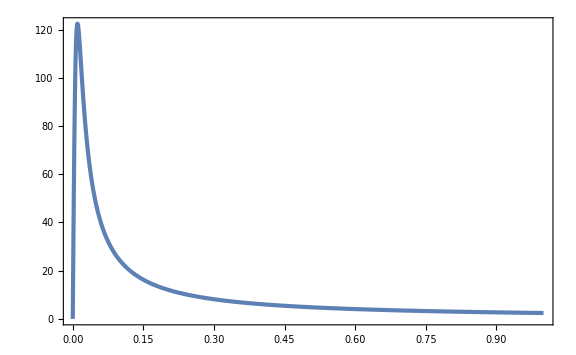

```mathematica
Plot[dzdr[r]/.{ξ->10^4},{r,0,1},PlotRange->Full]
```

```mathematica
z[r_]=Integrate[dzdr[rp],{rp,0,r}]//Simplify
```

(√(2+6 ξ)-√(1+6 ξ+1/(1+r^2 ξ))+√(1+6 ξ) (-ArcSinh[√(1+6 ξ)]+ArcSinh[√((1+6 ξ) (1+r^2 ξ))]))/(√ξ)

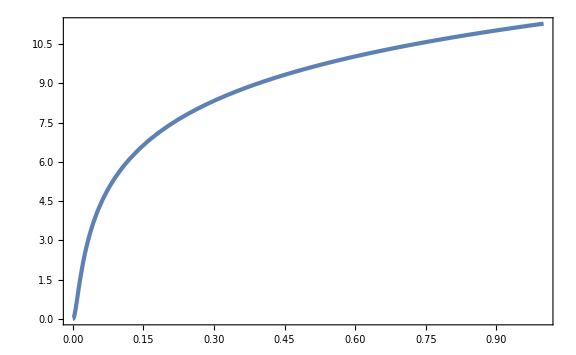

```mathematica
Plot[z[r]/.{ξ->10^4},{r,0,1}]
```

```mathematica
r[ρ_]=ρ/Sqrt[1-ξ ρ^2];
```

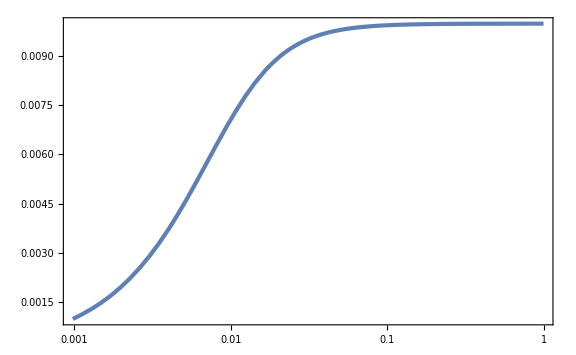

```mathematica
LogLinearPlot[ρ[r]/.{ξ->10^4},{r,0,1},PlotRange->Full]
```

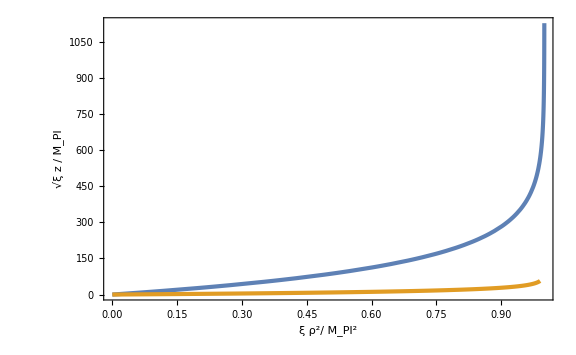

```mathematica
ParametricPlot[{{ξ ρ[r]^2/.{ξ->10^4},Sqrt[ξ]z[r]/.{ξ->10^4}},{ξ ρ[r]^2/.{ξ->10^2},Sqrt[ξ]z[r]/.{ξ->10^2}}},{r,0,1},PlotRange->Full,{FrameLabel->{Row[{ξ ρ^2,"/ ",Subscript[M, Pl]^2}],Row[{Sqrt[ξ]z," / ",Subscript[M, Pl]}]}}]
```

```mathematica
z[0]
```

0

```mathematica
zinρ2[ρ2_]=z[r[Sqrt[ρ2]]]//FullSimplify
```

(√(2+6 ξ)-√(2-ξ (-6+ρ2))+√(1+6 ξ) (-ArcSinh[√(1+6 ξ)]+ArcSinh[√((1+6 ξ)/(1-ξ ρ2))]))/(√ξ)

```mathematica
ξfid=Sqrt[1/(72 π^2 2 10^-9)]60;ξfid//N
```

50329.2

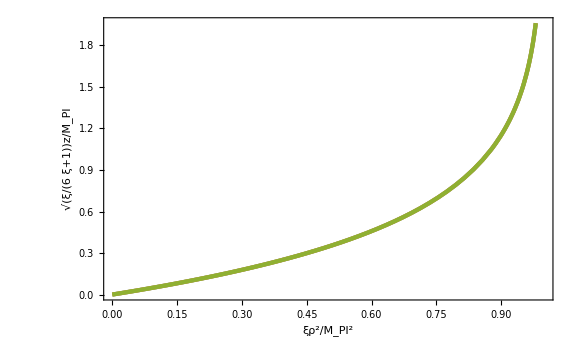

```mathematica
Plot[{Sqrt[ξ/(6ξ+1)]zinρ2[xr2/ξ]/.{ξ->10^3},Sqrt[ξ/(6ξ+1)]zinρ2[xr2/ξ]/.{ξ->10^4},Sqrt[ξ/(6ξ+1)]zinρ2[xr2/ξ]/.{ξ->10^5}},{xr2,0,1},{FrameLabel->{Row[{ξ,ρ^2/Subscript[M, Pl]^2}],Row[{Sqrt[ξ/(6ξ+1)],z/Subscript[M, Pl]}]}}]
```

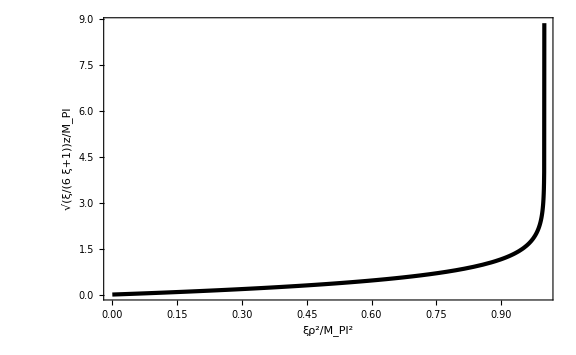

```mathematica
Plot[{Sqrt[ξ/(6ξ+1)]zinρ2[xr2/ξ]/.{ξ->10^4}},{xr2,0,1},{FrameLabel->{Row[{ξ,ρ^2/Subscript[M, Pl]^2}],Row[{Sqrt[ξ/(6ξ+1)],z/Subscript[M, Pl]}]}},PlotStyle->{Black,AbsoluteThickness[3]},PlotRange->Full]
```

```mathematica
Sqrt[ξ/(6ξ+1)]zinρ2[-1/ξ]/.{ξ->10^4}//N
```

-0.346578

```mathematica
ρ2inzList=Table[{Sqrt[ξ/(6ξ+1)]zinρ2[(1-10^-logx)/ξ]/.{ξ->10^4},1-10^-logx},{logx,-1,10,1/100}];
```

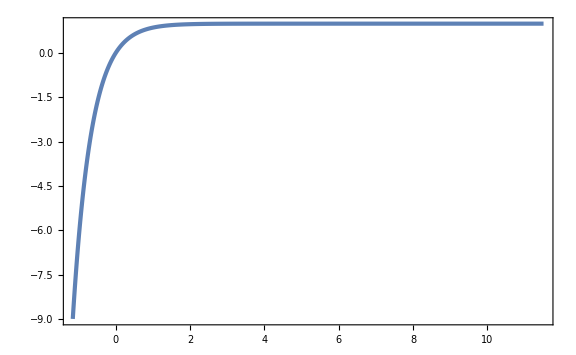

```mathematica
ListPlot[ρ2inzList,PlotRange->Full]
```

```mathematica
ρ2inzint[z_]=Interpolation[ρ2inzList][z];
```

```mathematica
V[r_,z_]=(1/2)/4 r^4+1/4(r^2-ρ2inzint[z])^2;
```

```mathematica
Plot3D[V[r,z],{r,0,1.2},{z,-1,10},PlotRange->{0,0.15},ClippingStyle->None]
```

-Graphics3D-

```mathematica
ContourPlot[V[r,z],{z,-1,10},{r,0,12/10},Contours->15,FrameLabel->{Row[{Sqrt[ξ/(6ξ+1)],z/Subscript[M, Pl]}],(Sqrt[ξ]ρ)/Subscript[M, Pl]},PlotLegends->BarLegend[Automatic,LegendLabel->Placed[V/(Subscript[M, Pl]^4/ ξ^2),Right]]]
```

-Graphics-

```mathematica
Normal[Series[zinρ2[ρ2],{ρ2,0,2}]]
```

(√ξ (√2+3 √2 ξ) ρ2)/(2 √(1+3 ξ))+(3 ξ^(3/2) (√2+7 √2 ξ+12 √2 ξ^2) ρ2^2)/(16 (1+3 ξ)^(3/2))

```mathematica
dρ2dz[ρ2_]=(zinρ2'[ρ2])^-1//Simplify;
d2ρ2dz2[ρ2_]=(zinρ2'[ρ2])^-1 dρ2dz'[ρ2]//Simplify;
d3ρ2dz3[ρ2_]=(zinρ2'[ρ2])^-1 d2ρ2dz2'[ρ2]//Simplify;
d4ρ2dz4[ρ2_]=(zinρ2'[ρ2])^-1 d3ρ2dz3'[ρ2]//Simplify;
d5ρ2dz5[ρ2_]=(zinρ2'[ρ2])^-1 d4ρ2dz4'[ρ2]//Simplify;
d6ρ2dz6[ρ2_]=(zinρ2'[ρ2])^-1 d5ρ2dz5'[ρ2]//Simplify;
d7ρ2dz7[ρ2_]=(zinρ2'[ρ2])^-1 d6ρ2dz6'[ρ2]//Simplify;
d8ρ2dz8[ρ2_]=(zinρ2'[ρ2])^-1 d7ρ2dz7'[ρ2]//Simplify;
```

```mathematica
ρ2inz[z_]=dρ2dz[0]z+1/2 d2ρ2dz2[0] z^2+1/(2 3)d3ρ2dz3[0] z^3+1/(2 3 4)d4ρ2dz4[0] z^4+1/(2 3 4 5)d5ρ2dz5[0] z^5+1/(2 3 4 5 6)d6ρ2dz6[0] z^6+1/(2 3 4 5 6 7)d7ρ2dz7[0] z^7+1/(2 3 4 5 6 7 8)d8ρ2dz8[0] z^8
```

(z^2 (-3-12 ξ))/(-2-6 ξ)^2+(4 z^3 √ξ (1+6 ξ)^2)/(3 (2+6 ξ)^(7/2))+(2 z)/(√(ξ (2+6 ξ)))-(z^4 ξ (1+6 ξ)^2 (-3+12 ξ))/(3 (2+6 ξ)^5)+(2 z^5 ξ^(3/2) (1+6 ξ)^2 (-1-84 ξ+72 ξ^2))/(15 (2+6 ξ)^(13/2))-(z^6 ξ^2 (1+6 ξ)^2 (57+456 ξ-2952 ξ^2+864 ξ^3))/(45 (-2-6 ξ)^8)+(8 z^7 ξ^(5/2) (1+6 ξ)^2 (-38+492 ξ+6264 ξ^2-10800 ξ^3+1296 ξ^4))/(315 (2+6 ξ)^(19/2))+(z^8 ξ^3 (1+6 ξ)^2 (-366-13092 ξ-23688 ξ^2+405648 ξ^3-289008 ξ^4+15552 ξ^5))/(315 (-2-6 ξ)^11)

```mathematica
Collect[Normal[Series[Normal[Series[zinρ2[ρ2],{ρ2,0,8}]]/.{ρ2->ρ2inz[z]},{z,0,8}]],z,FullSimplify]
```

z

```mathematica
Vsur[ρ2_,z_]=λt/4(ρ2-ρ2inz[z])^2;
(*1/ξ^2(Exp[-Sqrt[2/3]z]-Exp[-Sqrt[2/3]z[r[ρ]]])^2*)(*1/ξ^2(z-z[r[ρ]])^2+Sqrt[2/3] 1/ξ^2(z-z[r[ρ]])^3+7/18 1/ξ^2(z-z[r[ρ]])^4;*)
```

```mathematica
Normal[Series[SeriesCoefficient[Series[Vsur[ϵ^2 ρ^2,ϵ z],{ϵ,0,8}],0],{ξ,∞,1}]]//Simplify
Normal[Series[SeriesCoefficient[Series[Vsur[ϵ^2 ρ^2,ϵ z],{ϵ,0,8}],1],{ξ,∞,1}]]//Simplify
Normal[Series[SeriesCoefficient[Series[Vsur[ϵ^2 ρ^2,ϵ z],{ϵ,0,8}],2],{ξ,∞,2}]]//Simplify
Normal[Series[SeriesCoefficient[Series[Vsur[ϵ^2 ρ^2,ϵ z],{ϵ,0,8}],3],{ξ,∞,1}]]//Simplify
Normal[Series[SeriesCoefficient[Series[Vsur[ϵ^2 ρ^2,ϵ z],{ϵ,0,8}],4],{ξ,∞,1}]]//Simplify
Normal[Series[SeriesCoefficient[Series[Vsur[ϵ^2 ρ^2,ϵ z],{ϵ,0,8}],5],{ξ,∞,1}]]//Simplify
Normal[Series[SeriesCoefficient[Series[Vsur[ϵ^2 ρ^2,ϵ z],{ϵ,0,8}],6],{ξ,∞,1}]]//Simplify
Normal[Series[SeriesCoefficient[Series[Vsur[ϵ^2 ρ^2,ϵ z],{ϵ,0,8}],7],{ξ,∞,1}]]//Simplify
Normal[Series[SeriesCoefficient[Series[Vsur[ϵ^2 ρ^2,ϵ z],{ϵ,0,8}],8],{ξ,∞,1}]]//Simplify
```

0

0

(z^2 λt)/(6 ξ^2)

-(z λt ρ^2)/(√6 ξ)

(z^2 λt ρ^2)/(6 ξ)+(λt ρ^4)/4

-(z^3 λt ρ^2)/(9 √6 ξ)

(z^4 λt ρ^2)/(108 ξ)

-(z^5 λt ρ^2)/(270 √6 ξ)

(z^6 λt ρ^2)/(4860 ξ)

```mathematica
V[ρ2_,z_]=λ/4 ρ2^2+Vsur[ρ2,z]//Simplify
```

(λ ρ2^2)/4+1/4 λt ((3 z^2 (1+4 ξ))/(4 (1+3 ξ)^2)+(z^4 ξ (-1+4 ξ) (1+6 ξ)^2)/(32 (1+3 ξ)^5)-(4 z^3 √ξ (1+6 ξ)^2)/(3 (2+6 ξ)^(7/2))-(2 z)/(√(ξ (2+6 ξ)))-(2 z^5 ξ^(3/2) (1+6 ξ)^2 (-1-84 ξ+72 ξ^2))/(15 (2+6 ξ)^(13/2))+(z^6 ξ^2 (1+6 ξ)^2 (19+152 ξ-984 ξ^2+288 ξ^3))/(3840 (1+3 ξ)^8)-(16 z^7 ξ^(5/2) (1+6 ξ)^2 (-19+246 ξ+3132 ξ^2-5400 ξ^3+648 ξ^4))/(315 (2+6 ξ)^(19/2))+(z^8 ξ^3 (1+6 ξ)^2 (-61-2182 ξ-3948 ξ^2+67608 ξ^3-48168 ξ^4+2592 ξ^5))/(107520 (1+3 ξ)^11)+ρ2)^2

```mathematica
D[V[h1^2,0], h1]/.{h1->0}
D[V[0,z], z]/.{z->0}
```

0

0

```mathematica
coord={h1,h2,h3,h4,z};
```

```mathematica
M2matrix=Table[D[D[V[h1^2+h2^2+h3^2+h4^2,z], coord[[j]]], coord[[i]]],{i,5},{j,5}]/.{h1->0,h2->0,h3->0,h4->0,z->0}//Simplify
```

{{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,λt/(ξ+3 ξ^2)}}

```mathematica
ρ2indz[ρ2_,dz_]=ρ2+dρ2dz[ρ2]dz+1/2 d2ρ2dz2[ρ2] dz^2+1/(2 3)d3ρ2dz3[ρ2] dz^3+1/(2 3 4)d4ρ2dz4[ρ2] dz^4+1/(2 3 4 5)d5ρ2dz5[ρ2] dz^5+1/(2 3 4 5 6)d6ρ2dz6[ρ2] dz^6+1/(2 3 4 5 6 7)d7ρ2dz7[ρ2] dz^7+1/(2 3 4 5 6 7 8)d8ρ2dz8[ρ2] dz^8;
```

```mathematica
Vindρdz[ρ_,dρ_,dz_]=λ/4((ρ+dρ)^2)^2+λt/4((ρ+dρ)^2-ρ2indz[ρ^2,dz])^2;
```

```mathematica
Vindρdz[ρ,0,0]
```

(λ ρ^4)/4

```mathematica
Collect[Normal[Series[SeriesCoefficient[Series[Vindρdz[sqxr/Sqrt[ξ],ϵ dρ,ϵ dz],{ϵ,0,8}],0],{ξ,∞,2}]]/.{sqxr->Sqrt[ξ]ρ}//Simplify,ξ,Simplify]
Collect[Normal[Series[SeriesCoefficient[Series[Vindρdz[sqxr/Sqrt[ξ],ϵ dρ,ϵ dz],{ϵ,0,8}],1],{ξ,∞,2}]]/.{sqxr->Sqrt[ξ]ρ}//Simplify,ξ,Simplify]
Collect[Normal[Series[SeriesCoefficient[Series[Vindρdz[sqxr/Sqrt[ξ],ϵ dρ,ϵ dz],{ϵ,0,8}],2],{ξ,∞,2}]]/.{sqxr->Sqrt[ξ]ρ}//Simplify,ξ,Simplify]
Collect[Normal[Series[SeriesCoefficient[Series[Vindρdz[sqxr/Sqrt[ξ],ϵ dρ,ϵ dz],{ϵ,0,8}],3],{ξ,∞,2}]]/.{sqxr->Sqrt[ξ]ρ}//Simplify,ξ,Simplify]
Collect[Normal[Series[SeriesCoefficient[Series[Vindρdz[sqxr/Sqrt[ξ],ϵ dρ,ϵ dz],{ϵ,0,8}],4],{ξ,∞,2}]]/.{sqxr->Sqrt[ξ]ρ}//Simplify,ξ,Simplify]
Collect[Normal[Series[SeriesCoefficient[Series[Vindρdz[sqxr/Sqrt[ξ],ϵ dρ,ϵ dz],{ϵ,0,8}],5],{ξ,∞,2}]]/.{sqxr->Sqrt[ξ]ρ}//Simplify,ξ,Simplify]
Collect[Normal[Series[SeriesCoefficient[Series[Vindρdz[sqxr/Sqrt[ξ],ϵ dρ,ϵ dz],{ϵ,0,8}],6],{ξ,∞,2}]]/.{sqxr->Sqrt[ξ]ρ}//Simplify,ξ,Simplify]
Collect[Normal[Series[SeriesCoefficient[Series[Vindρdz[sqxr/Sqrt[ξ],ϵ dρ,ϵ dz],{ϵ,0,8}],7],{ξ,∞,2}]]/.{sqxr->Sqrt[ξ]ρ}//Simplify,ξ,Simplify]
Collect[Normal[Series[SeriesCoefficient[Series[Vindρdz[sqxr/Sqrt[ξ],ϵ dρ,ϵ dz],{ϵ,0,8}],8],{ξ,∞,2}]]/.{sqxr->Sqrt[ξ]ρ}//Simplify,ξ,Simplify]
```

(λ ρ^4)/4

dρ λ ρ^3

(dz λt (3 dz+√6 dρ ρ))/(18 ξ^2)-(dz λt ρ (4 dz ρ+√6 dρ (4+ρ^2)))/(12 ξ)+1/36 ρ^2 (18 dρ^2 (3 λ+2 λt)+6 dz^2 λt ρ^2+√6 dz dρ λt ρ (12+ρ^2))

(dz (-2 dz^2+dρ^2) λt)/(6 √6 ξ^2)+(dz λt (24 dz dρ ρ+8 √6 dz^2 ρ^2-3 √6 dρ^2 (4+ρ^2)))/(72 ξ)+1/72 ρ (72 dρ^3 (λ+λt)-24 dz^2 dρ λt ρ^2-4 √6 dz^3 λt ρ^3+√6 dz dρ^2 λt ρ (12+ρ^2))

(dz^2 (14 dz^2-15 dρ^2) λt)/(216 ξ^2)+1/216 (54 dρ^4 (λ+λt)+8 √6 dz^3 dρ λt ρ^3+14 dz^4 λt ρ^4-9 dz^2 dρ^2 λt ρ^2 (4+ρ^2))+(dz^2 λt (-2 √6 dz dρ ρ-7 dz^2 ρ^2+dρ^2 (9+6 ρ^2)))/(54 ξ)

-(dz^3 (3 dz^2-5 dρ^2) λt)/(54 √6 ξ^2)-1/648 dz^3 λt ρ^2 (12 dz dρ ρ+6 √6 dz^2 ρ^2-√6 dρ^2 (12+7 ρ^2))+(dz^3 λt (12 dz dρ ρ+12 √6 dz^2 ρ^2-√6 dρ^2 (12+17 ρ^2)))/(648 ξ)

(dz^4 (124 dz^2-285 dρ^2) λt)/(19440 ξ^2)+(dz^4 λt ρ^2 (24 √6 dz dρ ρ+124 dz^2 ρ^2-45 dρ^2 (4+5 ρ^2)))/19440-(dz^4 λt (12 √6 dz dρ ρ+124 dz^2 ρ^2-15 dρ^2 (6+17 ρ^2)))/(9720 ξ)

-(dz^5 (dz^2-3 dρ^2) λt)/(270 √6 ξ^2)-(dz^5 λt ρ^2 (8 dz dρ ρ+12 √6 dz^2 ρ^2-√6 dρ^2 (12+31 ρ^2)))/19440+(dz^5 λt (8 dz dρ ρ+24 √6 dz^2 ρ^2-√6 dρ^2 (12+67 ρ^2)))/(19440 ξ)

(dz^6 (127 dz^2-483 dρ^2) λt)/(408240 ξ^2)-(dz^6 λt (4 √6 dz dρ ρ+127 dz^2 ρ^2-42 dρ^2 (1+11 ρ^2)))/(204120 ξ)+(dz^6 λt ρ^2 (8 √6 dz dρ ρ+127 dz^2 ρ^2-21 dρ^2 (4+21 ρ^2)))/408240

```mathematica
dM2matrix=Normal[Series[{{D[D[Vindρdz[sqxr/Sqrt[ξ],dρ,dz], dρ], dρ],D[D[Vindρdz[sqxr/Sqrt[ξ],dρ,dz], dz], dρ]},{D[D[Vindρdz[sqxr/Sqrt[ξ],dρ,dz], dρ], dz],D[D[Vindρdz[sqxr/Sqrt[ξ],dρ,dz], dz], dz]}}/.{dρ->0,dz->0},{ξ,∞,2}]]/.{sqxr->Sqrt[ξ]ρ}
```

{{(3 λ ξ ρ^2+2 λt ξ ρ^2)/ξ,(√(2/3) λt ρ (-1+ξ ρ^2))/ξ},{(√(2/3) λt ρ (-1+ξ ρ^2))/ξ,(λt (-1+ξ ρ^2)^2)/(3 ξ^2)}}

```mathematica
(λ r[ρ]^4)/(4(1+ξ r[ρ]^2)^2)//Simplify
```

(λ ρ^4)/4

```mathematica
Normal[Series[Sqrt[ξ/(6ξ+1)]zinρ2[xr2/ξ]//Simplify,{ξ,∞,0}]]
```

-1/2 Log[1-xr2]

```mathematica
ρ2inzlargeξ[z_]=(1-Exp[-2Sqrt[ξ/(6ξ+1)]z])/ξ;
```

```mathematica
Vlargeξ[ρ2_,z_]=λ/4 ρ2^2+λt/4(ρ2-ρ2inzlargeξ[z])^2;
```

```mathematica
Plot3D[Log10[Vlargeξ[xρ2/ξ,Sqrt[(6ξ+1)/ξ]zp]/.{ξ->5 10^4 10^-1,λ->10^-2,λt->1}],{xρ2,0,2},{zp,-1,10}]
```

-Graphics3D-

```mathematica
(λ ρ2inzlargeξ[z]^2)/4
```

((1-ⅇ^(-2 z √(ξ/(1+6 ξ))))^2 λ)/(4 ξ^2)

```mathematica
SeriesCoefficient[Series[(ϵ^2 ρ^2-ρ2inzlargeξ[ϵ z])^2,{ϵ,0,8}],0]//Simplify
SeriesCoefficient[Series[(ϵ^2 ρ^2-ρ2inzlargeξ[ϵ z])^2,{ϵ,0,8}],1]//Simplify
SeriesCoefficient[Series[(ϵ^2 ρ^2-ρ2inzlargeξ[ϵ z])^2,{ϵ,0,8}],2]//Simplify
SeriesCoefficient[Series[(ϵ^2 ρ^2-ρ2inzlargeξ[ϵ z])^2,{ϵ,0,8}],3]//Simplify
SeriesCoefficient[Series[(ϵ^2 ρ^2-ρ2inzlargeξ[ϵ z])^2,{ϵ,0,8}],4]//Simplify
SeriesCoefficient[Series[(ϵ^2 ρ^2-ρ2inzlargeξ[ϵ z])^2,{ϵ,0,8}],5]//Simplify
SeriesCoefficient[Series[(ϵ^2 ρ^2-ρ2inzlargeξ[ϵ z])^2,{ϵ,0,8}],6]//Simplify
SeriesCoefficient[Series[(ϵ^2 ρ^2-ρ2inzlargeξ[ϵ z])^2,{ϵ,0,8}],7]//Simplify
SeriesCoefficient[Series[(ϵ^2 ρ^2-ρ2inzlargeξ[ϵ z])^2,{ϵ,0,8}],8]//Simplify
```

0

0

(4 z^2)/(ξ+6 ξ^2)

-(4 z (2 z^2+(1+6 ξ) ρ^2))/(√ξ (1+6 ξ)^(3/2))

(28 z^4)/(3 (1+6 ξ)^2)+(4 z^2 ρ^2)/(1+6 ξ)+ρ^4

-(8 √ξ (3 z^5+z^3 (1+6 ξ) ρ^2))/(3 (1+6 ξ)^(5/2))

(4 ξ (62 z^6+15 z^4 (1+6 ξ) ρ^2))/(45 (1+6 ξ)^3)

-(8 ξ^(3/2) (6 z^7+z^5 (1+6 ξ) ρ^2))/(15 (1+6 ξ)^(7/2))

(4 ξ^2 (127 z^8+14 z^6 (1+6 ξ) ρ^2))/(315 (1+6 ξ)^4)

#### embedding

```mathematica
$Assumptions={ξ>1/6,r>0,u>0};
```

```mathematica
G[r_]=Normal[Series[Sqrt[(1+ξ (1+6ξ) r^2)/((1+ξ r^2)^2)],{r,0,2}]]//Simplify
```

1+1/2 r^2 ξ (-1+6 ξ)

```mathematica
u[r_]=Integrate[G[r],r]//Simplify
```

r+r^3 (-ξ/6+ξ^2)

```mathematica
u'[r]//Simplify
```

1+1/2 r^2 ξ (-1+6 ξ)

```mathematica
f[r_]=G[r]r//Simplify
hu[r_]=Sqrt[1-(f'[r]/u'[r])^2]//Simplify
h[r_]=Integrate[Normal[Series[hu[r]u'[r],{r,0,2}]]//Simplify,r]//Simplify
```

r+1/2 r^3 ξ (-1+6 ξ)

√(1-((1+3/2 r^2 ξ (-1+6 ξ))^2)/((1+3 r^2 (-ξ/6+ξ^2))^2))

(ⅈ r^2 √(ξ (-1+6 ξ)))/(√2)

```mathematica
Normal[Series[(f'[r]^2+h'[r]^2)/u'[r]^2,{r,0,2}]]//Simplify
```

1

```mathematica
X[r_,θ_]=Normal[Series[f[r]Cos[θ],{r,0,2}]]
Y[r_,θ_]=Normal[Series[f[r]Sin[θ],{r,0,2}]]
Z[r_,θ_]=Normal[Series[h[r],{r,0,2}]]//Simplify
```

r Cos[θ]

r Sin[θ]

(ⅈ r^2 √(ξ (-1+6 ξ)))/(√2)

```mathematica
Z[r,θ]^2+1/2(X[r,θ]^2+Y[r,θ]^2)^2 ξ(6ξ-1)//Simplify
```

0

```mathematica
λ/ξ^2(Z^2+1/2(X^2+Y^2)^2 ξ(6ξ-1))//Expand
```

3 X^4 λ+6 X^2 Y^2 λ+3 Y^4 λ+(Z^2 λ)/ξ^2-(X^4 λ)/(2 ξ)-(X^2 Y^2 λ)/ξ-(Y^4 λ)/(2 ξ)

```mathematica
Clear[dr,dθ]
```

```mathematica
dX=dr D[X[r,θ], r]+dθ D[X[r,θ], θ]//Simplify
dY=dr D[Y[r,θ], r]+dθ D[Y[r,θ], θ]//Simplify
dZ=dr D[Z[r,θ], r]+dθ D[Z[r,θ], θ]//Simplify
```

dr Cos[θ]-dθ r Sin[θ]

dθ r Cos[θ]+dr Sin[θ]

ⅈ √2 dr r √(ξ (-1+6 ξ))

```mathematica
dX^2+dY^2+dZ^2//Simplify
```

dθ^2 r^2+dr^2 (1+2 r^2 (1-6 ξ) ξ)

```mathematica
Collect[Normal[Series[G[r]^2(dr^2+r^2 dθ^2),{r,0,2}]]//Simplify,dr]
```

dθ^2 r^2+dr^2 (1+r^2 ξ (-1+6 ξ))

```mathematica
Simplify[dX^2+dY^2+dZ^2/.{dr->dx D[Sqrt[x^2+y^2], x]+dy D[Sqrt[x^2+y^2], y],dθ->dx D[ArcTan[y/x], x]+dy D[ArcTan[y/x], y]}]/.{r^2->x^2+y^2}//Simplify
```

4 dx dy x y (1-6 ξ) ξ+dx^2 (1+2 x^2 (1-6 ξ) ξ)+dy^2 (1+2 y^2 (1-6 ξ) ξ)

```mathematica
dr^2+(x^2+y^2)dθ^2/.{dr->dx D[Sqrt[x^2+y^2], x]+dy D[Sqrt[x^2+y^2], y],dθ->dx D[ArcTan[y/x], x]+dy D[ArcTan[y/x], y]}//Simplify
```

dx^2+dy^2

### Higgs-R metric

```mathematica
Clear[coord,metric,inversemetric,affine,riemann,ricci,acalar,einstein,r,θ,ϕ,t]
```

```mathematica
coord={h1,h2,h3,h4,w};
n=Length[coord]
```

5

```mathematica
metric=DiagonalMatrix[Join[Table[Mp/w,{i,n-1}],{3/4 Mp^2/w^2}]]
```

{{Mp/w,0,0,0,0},{0,Mp/w,0,0,0},{0,0,Mp/w,0,0},{0,0,0,Mp/w,0},{0,0,0,0,(3 Mp^2)/(4 w^2)}}

```mathematica
metric//MatrixForm
```

(Mp/w | 0 | 0 | 0 | 0
0 | Mp/w | 0 | 0 | 0
0 | 0 | Mp/w | 0 | 0
0 | 0 | 0 | Mp/w | 0
0 | 0 | 0 | 0 | (3 Mp^2)/(4 w^2))

```mathematica
inversemetric=Simplify[Inverse[metric]]
```

{{w/Mp,0,0,0,0},{0,w/Mp,0,0,0},{0,0,w/Mp,0,0},{0,0,0,w/Mp,0},{0,0,0,0,(4 w^2)/(3 Mp^2)}}

```mathematica
inversemetric//MatrixForm
```

(w/Mp | 0 | 0 | 0 | 0
0 | w/Mp | 0 | 0 | 0
0 | 0 | w/Mp | 0 | 0
0 | 0 | 0 | w/Mp | 0
0 | 0 | 0 | 0 | (4 w^2)/(3 Mp^2))

```mathematica
affine:=affine=Simplify[Table[(1/2)*Sum[(inversemetric[[i,s]])*(D[metric[[s,j]],coord[[k]]]+D[metric[[s,k]],coord[[j]]]-D[metric[[j,k]],coord[[s]]]),{s,1,n}],{i,1,n},{j,1,n},{k,1,n}]]
```

```mathematica
listaffine:=Table[If[UnsameQ[affine[[i,j,k]],0],{ToString[Γ[i,j,k]],affine[[i,j,k]]}],{i,1,n},{j,1,n},{k,1,j}]
```

```mathematica
TableForm[Partition[DeleteCases[Flatten[listaffine],Null],2],TableSpacing->{2,2}]
```

Γ[1, 5, 1] | -1/(2 w)
Γ[2, 5, 2] | -1/(2 w)
Γ[3, 5, 3] | -1/(2 w)
Γ[4, 5, 4] | -1/(2 w)
Γ[5, 1, 1] | 2/(3 Mp)
Γ[5, 2, 2] | 2/(3 Mp)
Γ[5, 3, 3] | 2/(3 Mp)
Γ[5, 4, 4] | 2/(3 Mp)
Γ[5, 5, 5] | -1/w

```mathematica
riemann:=riemann=Simplify[Table[D[affine[[i,j,l]],coord[[k]]]-D[affine[[i,j,k]],coord[[l]]]+Sum[affine[[s,j,l]]affine[[i,k,s]]-affine[[s,j,k]]affine[[i,l,s]],{s,1,n}],{i,1,n},{j,1,n},{k,1,n},{l,1,n}]]
```

```mathematica
listriemann:=Table[If[UnsameQ[riemann[[i,j,k,l]],0],{ToString[R[i,j,k,l]],riemann[[i,j,k,l]]}],{i,1,n},{j,1,n},{k,1,n},{l,1,k-1}]
```

```mathematica
TableForm[Partition[DeleteCases[Flatten[listriemann],Null],2],TableSpacing->{2,2}]
```

R[1, 2, 2, 1] | 1/(3 Mp w)
R[1, 3, 3, 1] | 1/(3 Mp w)
R[1, 4, 4, 1] | 1/(3 Mp w)
R[1, 5, 5, 1] | 1/(4 w^2)
R[2, 1, 2, 1] | -1/(3 Mp w)
R[2, 3, 3, 2] | 1/(3 Mp w)
R[2, 4, 4, 2] | 1/(3 Mp w)
R[2, 5, 5, 2] | 1/(4 w^2)
R[3, 1, 3, 1] | -1/(3 Mp w)
R[3, 2, 3, 2] | -1/(3 Mp w)
R[3, 4, 4, 3] | 1/(3 Mp w)
R[3, 5, 5, 3] | 1/(4 w^2)
R[4, 1, 4, 1] | -1/(3 Mp w)
R[4, 2, 4, 2] | -1/(3 Mp w)
R[4, 3, 4, 3] | -1/(3 Mp w)
R[4, 5, 5, 4] | 1/(4 w^2)
R[5, 1, 5, 1] | -1/(3 Mp w)
R[5, 2, 5, 2] | -1/(3 Mp w)
R[5, 3, 5, 3] | -1/(3 Mp w)
R[5, 4, 5, 4] | -1/(3 Mp w)

```mathematica
ricci:=ricci=Simplify[Table[Sum[riemann[[i,j,i,l]],{i,1,n}],{j,1,n},{l,1,n}]]
```

```mathematica
listricci:=Table[If[UnsameQ[ricci[[j,l]],0],{ToString[R[j,l]],ricci[[j,l]]}],{j,1,n},{l,1,j}]
```

```mathematica
TableForm[Partition[DeleteCases[Flatten[listricci],Null],2],TableSpacing->{2,2}]
```

R[1, 1] | -4/(3 Mp w)
R[2, 2] | -4/(3 Mp w)
R[3, 3] | -4/(3 Mp w)
R[4, 4] | -4/(3 Mp w)
R[5, 5] | -1/w^2

```mathematica
scalar=Simplify[Sum[inversemetric[[i,j]]ricci[[i,j]],{i,1,n},{j,1,n}]]
```

-20/(3 Mp^2)

### Higgs Palatini

```mathematica
Clear[coord,metric,inversemetric,affine,riemann,ricci,acalar,einstein,r,θ,ϕ,t]
```

```mathematica
coord={h1,h2,h3,h4};
n=Length[coord]
```

4

```mathematica
metric=DiagonalMatrix[Table[1/(1+ξ Sum[coord[[i]]^2,{i,n}]),{j,n}]]//Simplify
```

{{1/(1+(h1^2+h2^2+h3^2+h4^2) ξ),0,0,0},{0,1/(1+(h1^2+h2^2+h3^2+h4^2) ξ),0,0},{0,0,1/(1+(h1^2+h2^2+h3^2+h4^2) ξ),0},{0,0,0,1/(1+(h1^2+h2^2+h3^2+h4^2) ξ)}}

```mathematica
Eigensystem[metric]
```

{{1/(1+h1^2 ξ+h2^2 ξ+h3^2 ξ+h4^2 ξ),1/(1+h1^2 ξ+h2^2 ξ+h3^2 ξ+h4^2 ξ),1/(1+h1^2 ξ+h2^2 ξ+h3^2 ξ+h4^2 ξ),1/(1+h1^2 ξ+h2^2 ξ+h3^2 ξ+h4^2 ξ)},{{0,0,0,1},{0,0,1,0},{0,1,0,0},{1,0,0,0}}}

```mathematica
metric//MatrixForm
```

(1/(1+(h1^2+h2^2+h3^2+h4^2) ξ) | 0 | 0 | 0
0 | 1/(1+(h1^2+h2^2+h3^2+h4^2) ξ) | 0 | 0
0 | 0 | 1/(1+(h1^2+h2^2+h3^2+h4^2) ξ) | 0
0 | 0 | 0 | 1/(1+(h1^2+h2^2+h3^2+h4^2) ξ))

```mathematica
inversemetric=Simplify[Inverse[metric]]
```

{{1+(h1^2+h2^2+h3^2+h4^2) ξ,0,0,0},{0,1+(h1^2+h2^2+h3^2+h4^2) ξ,0,0},{0,0,1+(h1^2+h2^2+h3^2+h4^2) ξ,0},{0,0,0,1+(h1^2+h2^2+h3^2+h4^2) ξ}}

```mathematica
inversemetric//MatrixForm
```

(1+(h1^2+h2^2+h3^2+h4^2) ξ | 0 | 0 | 0
0 | 1+(h1^2+h2^2+h3^2+h4^2) ξ | 0 | 0
0 | 0 | 1+(h1^2+h2^2+h3^2+h4^2) ξ | 0
0 | 0 | 0 | 1+(h1^2+h2^2+h3^2+h4^2) ξ)

```mathematica
affine:=affine=Simplify[Table[(1/2)*Sum[(inversemetric[[i,s]])*(D[metric[[s,j]],coord[[k]]]+D[metric[[s,k]],coord[[j]]]-D[metric[[j,k]],coord[[s]]]),{s,1,n}],{i,1,n},{j,1,n},{k,1,n}]]
```

```mathematica
listaffine:=Table[If[UnsameQ[affine[[i,j,k]],0],{ToString[Γ[i,j,k]],affine[[i,j,k]]}],{i,1,n},{j,1,n},{k,1,j}]
```

```mathematica
TableForm[Partition[DeleteCases[Flatten[listaffine],Null],2],TableSpacing->{2,2}]
```

Γ[1, 1, 1] | -(h1 ξ)/(1+(h1^2+h2^2+h3^2+h4^2) ξ)
Γ[1, 2, 1] | -(h2 ξ)/(1+(h1^2+h2^2+h3^2+h4^2) ξ)
Γ[1, 2, 2] | (h1 ξ)/(1+(h1^2+h2^2+h3^2+h4^2) ξ)
Γ[1, 3, 1] | -(h3 ξ)/(1+(h1^2+h2^2+h3^2+h4^2) ξ)
Γ[1, 3, 3] | (h1 ξ)/(1+(h1^2+h2^2+h3^2+h4^2) ξ)
Γ[1, 4, 1] | -(h4 ξ)/(1+(h1^2+h2^2+h3^2+h4^2) ξ)
Γ[1, 4, 4] | (h1 ξ)/(1+(h1^2+h2^2+h3^2+h4^2) ξ)
Γ[2, 1, 1] | (h2 ξ)/(1+(h1^2+h2^2+h3^2+h4^2) ξ)
Γ[2, 2, 1] | -(h1 ξ)/(1+(h1^2+h2^2+h3^2+h4^2) ξ)
Γ[2, 2, 2] | -(h2 ξ)/(1+(h1^2+h2^2+h3^2+h4^2) ξ)
Γ[2, 3, 2] | -(h3 ξ)/(1+(h1^2+h2^2+h3^2+h4^2) ξ)
Γ[2, 3, 3] | (h2 ξ)/(1+(h1^2+h2^2+h3^2+h4^2) ξ)
Γ[2, 4, 2] | -(h4 ξ)/(1+(h1^2+h2^2+h3^2+h4^2) ξ)
Γ[2, 4, 4] | (h2 ξ)/(1+(h1^2+h2^2+h3^2+h4^2) ξ)
Γ[3, 1, 1] | (h3 ξ)/(1+(h1^2+h2^2+h3^2+h4^2) ξ)
Γ[3, 2, 2] | (h3 ξ)/(1+(h1^2+h2^2+h3^2+h4^2) ξ)
Γ[3, 3, 1] | -(h1 ξ)/(1+(h1^2+h2^2+h3^2+h4^2) ξ)
Γ[3, 3, 2] | -(h2 ξ)/(1+(h1^2+h2^2+h3^2+h4^2) ξ)
Γ[3, 3, 3] | -(h3 ξ)/(1+(h1^2+h2^2+h3^2+h4^2) ξ)
Γ[3, 4, 3] | -(h4 ξ)/(1+(h1^2+h2^2+h3^2+h4^2) ξ)
Γ[3, 4, 4] | (h3 ξ)/(1+(h1^2+h2^2+h3^2+h4^2) ξ)
Γ[4, 1, 1] | (h4 ξ)/(1+(h1^2+h2^2+h3^2+h4^2) ξ)
Γ[4, 2, 2] | (h4 ξ)/(1+(h1^2+h2^2+h3^2+h4^2) ξ)
Γ[4, 3, 3] | (h4 ξ)/(1+(h1^2+h2^2+h3^2+h4^2) ξ)
Γ[4, 4, 1] | -(h1 ξ)/(1+(h1^2+h2^2+h3^2+h4^2) ξ)
Γ[4, 4, 2] | -(h2 ξ)/(1+(h1^2+h2^2+h3^2+h4^2) ξ)
Γ[4, 4, 3] | -(h3 ξ)/(1+(h1^2+h2^2+h3^2+h4^2) ξ)
Γ[4, 4, 4] | -(h4 ξ)/(1+(h1^2+h2^2+h3^2+h4^2) ξ)

```mathematica
riemann:=riemann=Simplify[Table[D[affine[[i,j,l]],coord[[k]]]-D[affine[[i,j,k]],coord[[l]]]+Sum[affine[[s,j,l]]affine[[i,k,s]]-affine[[s,j,k]]affine[[i,l,s]],{s,1,n}],{i,1,n},{j,1,n},{k,1,n},{l,1,n}]]
```

```mathematica
listriemann:=Table[If[UnsameQ[riemann[[i,j,k,l]],0],{ToString[R[i,j,k,l]],riemann[[i,j,k,l]]}],{i,1,n},{j,1,n},{k,1,n},{l,1,k-1}]
```

```mathematica
TableForm[Partition[DeleteCases[Flatten[listriemann],Null],2],TableSpacing->{2,2}]
```

R[1, 2, 2, 1] | -(ξ (2+h3^2 ξ+h4^2 ξ))/((1+h1^2 ξ+h2^2 ξ+h3^2 ξ+h4^2 ξ)^2)
R[1, 2, 3, 1] | (h2 h3 ξ^2)/((1+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[1, 2, 3, 2] | -(h1 h3 ξ^2)/((1+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[1, 2, 4, 1] | (h2 h4 ξ^2)/((1+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[1, 2, 4, 2] | -(h1 h4 ξ^2)/((1+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[1, 3, 2, 1] | (h2 h3 ξ^2)/((1+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[1, 3, 3, 1] | -(ξ (2+h2^2 ξ+h4^2 ξ))/((1+h1^2 ξ+h2^2 ξ+h3^2 ξ+h4^2 ξ)^2)
R[1, 3, 3, 2] | (h1 h2 ξ^2)/((1+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[1, 3, 4, 1] | (h3 h4 ξ^2)/((1+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[1, 3, 4, 3] | -(h1 h4 ξ^2)/((1+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[1, 4, 2, 1] | (h2 h4 ξ^2)/((1+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[1, 4, 3, 1] | (h3 h4 ξ^2)/((1+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[1, 4, 4, 1] | -(ξ (2+h2^2 ξ+h3^2 ξ))/((1+h1^2 ξ+h2^2 ξ+h3^2 ξ+h4^2 ξ)^2)
R[1, 4, 4, 2] | (h1 h2 ξ^2)/((1+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[1, 4, 4, 3] | (h1 h3 ξ^2)/((1+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[2, 1, 2, 1] | (ξ (2+h3^2 ξ+h4^2 ξ))/((1+h1^2 ξ+h2^2 ξ+h3^2 ξ+h4^2 ξ)^2)
R[2, 1, 3, 1] | -(h2 h3 ξ^2)/((1+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[2, 1, 3, 2] | (h1 h3 ξ^2)/((1+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[2, 1, 4, 1] | -(h2 h4 ξ^2)/((1+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[2, 1, 4, 2] | (h1 h4 ξ^2)/((1+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[2, 3, 2, 1] | -(h1 h3 ξ^2)/((1+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[2, 3, 3, 1] | (h1 h2 ξ^2)/((1+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[2, 3, 3, 2] | -(ξ (2+h1^2 ξ+h4^2 ξ))/((1+h1^2 ξ+h2^2 ξ+h3^2 ξ+h4^2 ξ)^2)
R[2, 3, 4, 2] | (h3 h4 ξ^2)/((1+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[2, 3, 4, 3] | -(h2 h4 ξ^2)/((1+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[2, 4, 2, 1] | -(h1 h4 ξ^2)/((1+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[2, 4, 3, 2] | (h3 h4 ξ^2)/((1+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[2, 4, 4, 1] | (h1 h2 ξ^2)/((1+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[2, 4, 4, 2] | -(ξ (2+h1^2 ξ+h3^2 ξ))/((1+h1^2 ξ+h2^2 ξ+h3^2 ξ+h4^2 ξ)^2)
R[2, 4, 4, 3] | (h2 h3 ξ^2)/((1+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[3, 1, 2, 1] | -(h2 h3 ξ^2)/((1+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[3, 1, 3, 1] | (ξ (2+h2^2 ξ+h4^2 ξ))/((1+h1^2 ξ+h2^2 ξ+h3^2 ξ+h4^2 ξ)^2)
R[3, 1, 3, 2] | -(h1 h2 ξ^2)/((1+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[3, 1, 4, 1] | -(h3 h4 ξ^2)/((1+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[3, 1, 4, 3] | (h1 h4 ξ^2)/((1+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[3, 2, 2, 1] | (h1 h3 ξ^2)/((1+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[3, 2, 3, 1] | -(h1 h2 ξ^2)/((1+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[3, 2, 3, 2] | (ξ (2+h1^2 ξ+h4^2 ξ))/((1+h1^2 ξ+h2^2 ξ+h3^2 ξ+h4^2 ξ)^2)
R[3, 2, 4, 2] | -(h3 h4 ξ^2)/((1+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[3, 2, 4, 3] | (h2 h4 ξ^2)/((1+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[3, 4, 3, 1] | -(h1 h4 ξ^2)/((1+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[3, 4, 3, 2] | -(h2 h4 ξ^2)/((1+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[3, 4, 4, 1] | (h1 h3 ξ^2)/((1+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[3, 4, 4, 2] | (h2 h3 ξ^2)/((1+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[3, 4, 4, 3] | -(ξ (2+h1^2 ξ+h2^2 ξ))/((1+h1^2 ξ+h2^2 ξ+h3^2 ξ+h4^2 ξ)^2)
R[4, 1, 2, 1] | -(h2 h4 ξ^2)/((1+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[4, 1, 3, 1] | -(h3 h4 ξ^2)/((1+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[4, 1, 4, 1] | (ξ (2+h2^2 ξ+h3^2 ξ))/((1+h1^2 ξ+h2^2 ξ+h3^2 ξ+h4^2 ξ)^2)
R[4, 1, 4, 2] | -(h1 h2 ξ^2)/((1+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[4, 1, 4, 3] | -(h1 h3 ξ^2)/((1+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[4, 2, 2, 1] | (h1 h4 ξ^2)/((1+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[4, 2, 3, 2] | -(h3 h4 ξ^2)/((1+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[4, 2, 4, 1] | -(h1 h2 ξ^2)/((1+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[4, 2, 4, 2] | (ξ (2+h1^2 ξ+h3^2 ξ))/((1+h1^2 ξ+h2^2 ξ+h3^2 ξ+h4^2 ξ)^2)
R[4, 2, 4, 3] | -(h2 h3 ξ^2)/((1+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[4, 3, 3, 1] | (h1 h4 ξ^2)/((1+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[4, 3, 3, 2] | (h2 h4 ξ^2)/((1+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[4, 3, 4, 1] | -(h1 h3 ξ^2)/((1+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[4, 3, 4, 2] | -(h2 h3 ξ^2)/((1+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[4, 3, 4, 3] | (ξ (2+h1^2 ξ+h2^2 ξ))/((1+h1^2 ξ+h2^2 ξ+h3^2 ξ+h4^2 ξ)^2)

```mathematica
ricci:=ricci=Simplify[Table[Sum[riemann[[i,j,i,l]],{i,1,n}],{j,1,n},{l,1,n}]]
```

```mathematica
listricci:=Table[If[UnsameQ[ricci[[j,l]],0],{ToString[R[j,l]],ricci[[j,l]]}],{j,1,n},{l,1,j}]
```

```mathematica
TableForm[Partition[DeleteCases[Flatten[listricci],Null],2],TableSpacing->{2,2}]
```

R[1, 1] | (2 ξ (3+h2^2 ξ+h3^2 ξ+h4^2 ξ))/((1+h1^2 ξ+h2^2 ξ+h3^2 ξ+h4^2 ξ)^2)
R[2, 1] | -(2 h1 h2 ξ^2)/((1+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[2, 2] | (2 ξ (3+h1^2 ξ+h3^2 ξ+h4^2 ξ))/((1+h1^2 ξ+h2^2 ξ+h3^2 ξ+h4^2 ξ)^2)
R[3, 1] | -(2 h1 h3 ξ^2)/((1+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[3, 2] | -(2 h2 h3 ξ^2)/((1+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[3, 3] | (2 ξ (3+h1^2 ξ+h2^2 ξ+h4^2 ξ))/((1+h1^2 ξ+h2^2 ξ+h3^2 ξ+h4^2 ξ)^2)
R[4, 1] | -(2 h1 h4 ξ^2)/((1+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[4, 2] | -(2 h2 h4 ξ^2)/((1+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[4, 3] | -(2 h3 h4 ξ^2)/((1+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[4, 4] | (2 ξ (3+h1^2 ξ+h2^2 ξ+h3^2 ξ))/((1+h1^2 ξ+h2^2 ξ+h3^2 ξ+h4^2 ξ)^2)

```mathematica
scalar=Simplify[Sum[inversemetric[[i,j]]ricci[[i,j]],{i,1,n},{j,1,n}]]
```

(6 ξ (4+h1^2 ξ+h2^2 ξ+h3^2 ξ+h4^2 ξ))/(1+h1^2 ξ+h2^2 ξ+h3^2 ξ+h4^2 ξ)

```mathematica
scalar/.{h1->0,h2->0,h3->0,h4->0}
```

24 ξ

#### embedding Izumi

```mathematica
Quit[]
```

```mathematica
$Assumptions={ξ>0,r>0,ρ>0,ρ2>0,z>0,ξ ρ^2<1,ξ ρ2<1,xr2<1,sqxr<1};
```

```mathematica
F[r_]=1/Sqrt[1+ξ r^2];
ρ[r_]=r/Sqrt[1+ξ r^2];
```

```mathematica
dzdr[r_]=Sqrt[F[r]^2-ρ'[r]^2]//Simplify
```

√((r^2 ξ (2+r^2 ξ))/((1+r^2 ξ)^3))

```mathematica
dzdr[0]
```

0

```mathematica
Normal[Series[dzdr[r],{r,∞,1}]]
```

1/(r √ξ)

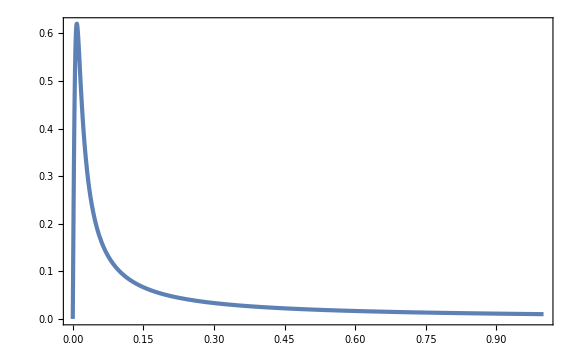

```mathematica
Plot[dzdr[r]/.{ξ->10^4},{r,0,1},PlotRange->Full]
```

```mathematica
z[r_]=Integrate[dzdr[rp],{rp,0,r}]//Simplify
```

(√2+(r^2 ξ)/(√(2+3 r^2 ξ+r^4 ξ^2))-2 √(1-1/(2+r^2 ξ))-ArcSinh[1]+ArcSinh[√(1+r^2 ξ)])/(√ξ)

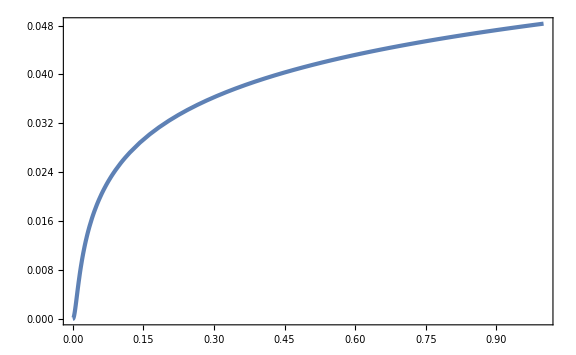

```mathematica
Plot[z[r]/.{ξ->10^4},{r,0,1}]
```

```mathematica
r[ρ_]=ρ/Sqrt[1-ξ ρ^2];
```

```mathematica
ρ[r[ρ]]//Simplify
```

ρ

```mathematica
LogLinearPlot[ρ[r]/.{ξ->10^4},{r,0,1},PlotRange->Full]
```

-Graphics-

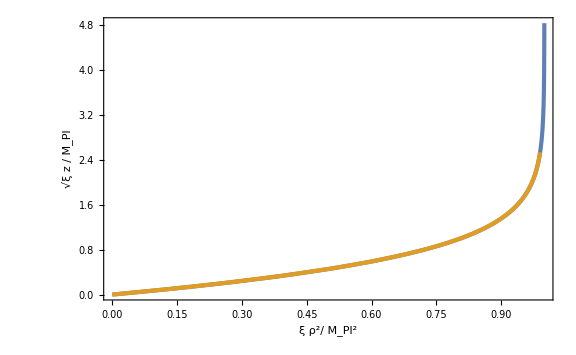

```mathematica
ParametricPlot[{{ξ ρ[r]^2/.{ξ->10^4},Sqrt[ξ]z[r]/.{ξ->10^4}},{ξ ρ[r]^2/.{ξ->10^2},Sqrt[ξ]z[r]/.{ξ->10^2}}},{r,0,1},PlotRange->Full,{FrameLabel->{Row[{ξ ρ^2,"/ ",Subscript[M, Pl]^2}],Row[{Sqrt[ξ]z," / ",Subscript[M, Pl]}]}}]
```

```mathematica
z[0]
```

0

```mathematica
zinρ2[ρ2_]=z[r[Sqrt[ρ2]]]//FullSimplify
```

(√2-√(2-ξ ρ2)+ArcCsch[√(1-ξ ρ2)]-ArcSinh[1])/(√ξ)

```mathematica
Clear[zinϵ]
```

```mathematica
zinϵ[ϵ_]=Simplify[Normal[Series[zinρ2[(1-ϵ)/ξ],{ϵ,0,0}]],{ϵ>0}]
```

(-2+2 √2-2 ArcSinh[1]+Log[4]-Log[ϵ])/(2 √ξ)

```mathematica
ρ2inz[zz_]=Simplify[(1-ϵ)/ξ/.Solve[zz==zinϵ[ϵ]&&zz>0,ϵ][[1]],{zz>0,ρ<1/Sqrt[ξ],ρ2<1/ξ}]
```

(1-4 ⅇ^(-2+2 √2-2 zz √ξ-2 ArcSinh[1]))/ξ

```mathematica
Normal[Series[Simplify[λ/4 ρ2inz[zz+1/(2Sqrt[ξ])(-2+2Sqrt[2]-2ArcSinh[1])]^2/.{zz->-1/Sqrt[ξ] Log[emz]}],{emz,0,2}]]/.{emz->E^(-Sqrt[ξ]zz)}//Simplify
Normal[Series[Simplify[(λ/(4 ξ^2)Tanh[Sqrt[ξ]zz]^4//TrigToExp//Simplify)/.{zz->-1/Sqrt[ξ] Log[emz]}],{emz,0,2}]]/.{emz->E^(-Sqrt[ξ]zz)}//Simplify
```

(λ-8 ⅇ^(-2 zz √ξ) λ)/(4 ξ^2)

(λ-8 ⅇ^(-2 zz √ξ) λ)/(4 ξ^2)

```mathematica
Normal[Series[Tanh[Log[ex/ϵ]]^4,{ϵ,0,2}]]
Normal[Series[(1-Csch[Log[ex/ϵ]]^2)^2,{ϵ,0,2}]]
```

1-(8 ϵ^2)/ex^2

1-(8 ϵ^2)/ex^2

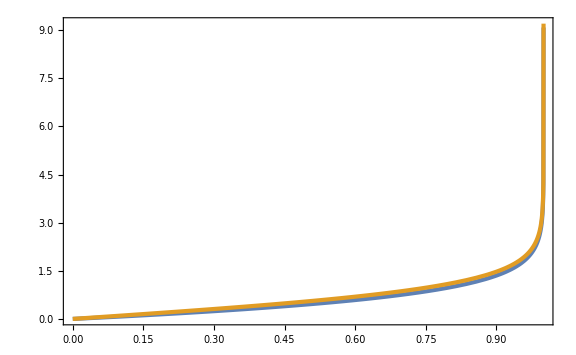

```mathematica
Plot[{Sqrt[ξ]zinρ2[xr2/ξ],ArcTanh[xr2]},{xr2,0,1},PlotRange->Full]
```

```mathematica
Sqrt[ξ]zinρ2[xr2/ξ]//TrigToExp//Simplify
```

√2-√(2-xr2)+Log[((-1+√2) (1+√(2-xr2)))/(√(1-xr2))]

```mathematica
ArcSinh[1]//TrigToExp
```

Log[1+√2]

```mathematica
Solve[(Sqrt[ξ]zinρ2[xr2/ξ]==sqxz//TrigToExp//FullSimplify)&&0<xr2<1&&0<sqxz<1,xr2]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[√2+Log[1+√(2-xr2)]==sqxz+√(2-xr2)+ArcSinh[1]+1/2 Log[1-xr2]&&0<xr2<1&&0<sqxz<1,xr2]

```mathematica
Normal[Series[zinρ2[ρ2],{ρ2,0,2}]]
```

(√ξ ρ2)/(√2)+(3 ξ^(3/2) ρ2^2)/(8 √2)

```mathematica
dρ2dz[ρ2_]=(zinρ2'[ρ2])^-1//Simplify
d2ρ2dz2[ρ2_]=(zinρ2'[ρ2])^-1 dρ2dz'[ρ2]//Simplify
d3ρ2dz3[ρ2_]=(zinρ2'[ρ2])^-1 d2ρ2dz2'[ρ2]//Simplify
d4ρ2dz4[ρ2_]=(zinρ2'[ρ2])^-1 d3ρ2dz3'[ρ2]//Simplify
d5ρ2dz5[ρ2_]=(zinρ2'[ρ2])^-1 d4ρ2dz4'[ρ2]//Simplify
d6ρ2dz6[ρ2_]=(zinρ2'[ρ2])^-1 d5ρ2dz5'[ρ2]//Simplify
d7ρ2dz7[ρ2_]=(zinρ2'[ρ2])^-1 d6ρ2dz6'[ρ2]//Simplify
d8ρ2dz8[ρ2_]=(zinρ2'[ρ2])^-1 d7ρ2dz7'[ρ2]//Simplify
```

(2-2 ξ ρ2)/(√(ξ (2-ξ ρ2)))

-(2 (-3+ξ ρ2) (-1+ξ ρ2))/(-2+ξ ρ2)^2

-(8 √ξ (-1+ξ ρ2))/(2-ξ ρ2)^(7/2)

-(8 ξ (-1+ξ ρ2) (-3+5 ξ ρ2))/(-2+ξ ρ2)^5

-(16 ξ^(3/2) (-1+ξ ρ2) (-1-12 ξ ρ2+15 ξ^2 ρ2^2))/(2-ξ ρ2)^(13/2)

(16 ξ^2 (-1+ξ ρ2) (57-95 ξ ρ2-63 ξ^2 ρ2^2+105 ξ^3 ρ2^3))/(-2+ξ ρ2)^8

-(128 ξ^(5/2) (-1+ξ ρ2) (-38+234 ξ ρ2-300 ξ^2 ρ2^2+105 ξ^4 ρ2^4))/(2-ξ ρ2)^(19/2)

-(128 ξ^3 (-1+ξ ρ2) (-366-352 ξ ρ2+4410 ξ^2 ρ2^2-5580 ξ^3 ρ2^3+945 ξ^4 ρ2^4+945 ξ^5 ρ2^5))/(-2+ξ ρ2)^11

```mathematica
ρ2inz[z_]=dρ2dz[0]z+1/2 d2ρ2dz2[0] z^2+1/(2 3)d3ρ2dz3[0] z^3+1/(2 3 4)d4ρ2dz4[0] z^4+1/(2 3 4 5)d5ρ2dz5[0] z^5+1/(2 3 4 5 6)d6ρ2dz6[0] z^6+1/(2 3 4 5 6 7)d7ρ2dz7[0] z^7+1/(2 3 4 5 6 7 8)d8ρ2dz8[0] z^8
```

-(3 z^2)/4+(√2 z)/(√ξ)+(z^3 √ξ)/(6 √2)+(z^4 ξ)/32-(z^5 ξ^(3/2))/(480 √2)-(19 z^6 ξ^2)/3840-(19 z^7 ξ^(5/2))/(10080 √2)+(61 z^8 ξ^3)/107520

```mathematica
Sqrt[ξ]dρ2dz[0]
d2ρ2dz2[0]
ξ^(-1/2)d3ρ2dz3[0]
ξ^-1 d4ρ2dz4[0]
ξ^(-3/2)d5ρ2dz5[0]
ξ^-2 d6ρ2dz6[0]
ξ^(-5/2)d7ρ2dz7[0]
ξ^-3 d8ρ2dz8[0]
```

√2

-3/2

1/(√2)

3/4

-1/(4 √2)

-57/16

-19/(2 √2)

183/8

```mathematica
Collect[Normal[Series[Normal[Series[zinρ2[ρ2],{ρ2,0,8}]]/.{ρ2->ρ2inz[z]},{z,0,8}]],z,FullSimplify]
```

z

```mathematica
Vsur[ρ2_,z_]=λt/4(ρ2-ρ2inz[z])^2;
(*1/ξ^2(Exp[-Sqrt[2/3]z]-Exp[-Sqrt[2/3]z[r[ρ]]])^2*)(*1/ξ^2(z-z[r[ρ]])^2+Sqrt[2/3] 1/ξ^2(z-z[r[ρ]])^3+7/18 1/ξ^2(z-z[r[ρ]])^4;*)
```

```mathematica
Normal[Series[SeriesCoefficient[Series[Vsur[ϵ^2 ρ^2,ϵ z],{ϵ,0,8}],0],{ξ,∞,0}]]//Simplify
Normal[Series[SeriesCoefficient[Series[Vsur[ϵ^2 ρ^2,ϵ z],{ϵ,0,8}],1],{ξ,∞,0}]]//Simplify
Normal[Series[SeriesCoefficient[Series[Vsur[ϵ^2 ρ^2,ϵ z],{ϵ,0,8}],2],{ξ,∞,1}]]//Simplify
Normal[Series[SeriesCoefficient[Series[Vsur[ϵ^2 ρ^2,ϵ z],{ϵ,0,8}],3],{ξ,∞,0}]]//Simplify
Normal[Series[SeriesCoefficient[Series[Vsur[ϵ^2 ρ^2,ϵ z],{ϵ,0,8}],4],{ξ,∞,0}]]//Simplify
Normal[Series[SeriesCoefficient[Series[Vsur[ϵ^2 ρ^2,ϵ z],{ϵ,0,8}],5],{ξ,∞,0}]]//Simplify
Normal[Series[SeriesCoefficient[Series[Vsur[ϵ^2 ρ^2,ϵ z],{ϵ,0,8}],6],{ξ,∞,0}]]//Simplify
Normal[Series[SeriesCoefficient[Series[Vsur[ϵ^2 ρ^2,ϵ z],{ϵ,0,8}],7],{ξ,∞,0}]]//Simplify
Normal[Series[SeriesCoefficient[Series[Vsur[ϵ^2 ρ^2,ϵ z],{ϵ,0,8}],8],{ξ,∞,0}]]//Simplify
```

0

0

(z^2 λt)/(2 ξ)

0

1/192 λt (43 z^4+72 z^2 ρ^2+48 ρ^4)

-(z^3 λt √ξ (3 z^2+8 ρ^2))/(96 √2)

-(λt ξ (107 z^6+180 z^4 ρ^2))/11520

-(z^5 λt ξ^(3/2) (3 z^2-2 ρ^2))/(1920 √2)

(λt ξ^2 (1381 z^8+3192 z^6 ρ^2))/1290240

```mathematica
V[ρ2_,z_]=λ/4 ρ2^2+Vsur[ρ2,z]//Simplify
```

1/4 (λ ρ2^2+λt ((3 z^2)/4-(√2 z)/(√ξ)-(z^3 √ξ)/(6 √2)-(z^4 ξ)/32+(z^5 ξ^(3/2))/(480 √2)+(19 z^6 ξ^2)/3840+(19 z^7 ξ^(5/2))/(10080 √2)-(61 z^8 ξ^3)/107520+ρ2)^2)

```mathematica
D[V[h1^2,0], h1]/.{h1->0}
D[V[0,z], z]/.{z->0}
```

0

0

```mathematica
coord={h1,h2,h3,h4,z};
```

```mathematica
M2matrix=Table[D[D[V[h1^2+h2^2+h3^2+h4^2,z], coord[[j]]], coord[[i]]],{i,5},{j,5}]/.{h1->0,h2->0,h3->0,h4->0,z->0}//Simplify
```

{{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,λt/ξ}}

```mathematica
ρ2indz[ρ2_,dz_]=ρ2+dρ2dz[ρ2]dz+1/2 d2ρ2dz2[ρ2] dz^2+1/(2 3)d3ρ2dz3[ρ2] dz^3+1/(2 3 4)d4ρ2dz4[ρ2] dz^4+1/(2 3 4 5)d5ρ2dz5[ρ2] dz^5+1/(2 3 4 5 6)d6ρ2dz6[ρ2] dz^6+1/(2 3 4 5 6 7)d7ρ2dz7[ρ2] dz^7+1/(2 3 4 5 6 7 8)d8ρ2dz8[ρ2] dz^8;
```

```mathematica
Vindρdz[ρ_,dρ_,dz_]=λ/4((ρ+dρ)^2)^2+λt/4((ρ+dρ)^2-ρ2indz[ρ^2,dz])^2;
```

```mathematica
Vindρdz[ρ,0,0]
```

(λ ρ^4)/4

```mathematica
Normal[Series[SeriesCoefficient[Series[Vindρdz[sqxr/Sqrt[ξ],ϵ dρ,ϵ dz],{ϵ,0,8}],0],{ξ,∞,0}]]//Simplify
Normal[Series[SeriesCoefficient[Series[Vindρdz[sqxr/Sqrt[ξ],ϵ dρ,ϵ dz],{ϵ,0,8}],1],{ξ,∞,0}]]//Simplify
Normal[Series[SeriesCoefficient[Series[Vindρdz[sqxr/Sqrt[ξ],ϵ dρ,ϵ dz],{ϵ,0,8}],2],{ξ,∞,0}]]//Simplify
Normal[Series[SeriesCoefficient[Series[Vindρdz[sqxr/Sqrt[ξ],ϵ dρ,ϵ dz],{ϵ,0,8}],3],{ξ,∞,0}]]//Simplify
Normal[Series[SeriesCoefficient[Series[Vindρdz[sqxr/Sqrt[ξ],ϵ dρ,ϵ dz],{ϵ,0,8}],4],{ξ,∞,0}]]//Simplify
Normal[Series[SeriesCoefficient[Series[Vindρdz[sqxr/Sqrt[ξ],ϵ dρ,ϵ dz],{ϵ,0,8}],5],{ξ,∞,0}]]//Simplify
Normal[Series[SeriesCoefficient[Series[Vindρdz[sqxr/Sqrt[ξ],ϵ dρ,ϵ dz],{ϵ,0,8}],6],{ξ,∞,0}]]//Simplify
Normal[Series[SeriesCoefficient[Series[Vindρdz[sqxr/Sqrt[ξ],ϵ dρ,ϵ dz],{ϵ,0,8}],7],{ξ,∞,0}]]//Simplify
Normal[Series[SeriesCoefficient[Series[Vindρdz[sqxr/Sqrt[ξ],ϵ dρ,ϵ dz],{ϵ,0,8}],8],{ξ,∞,0}]]//Simplify
```

0

0

0

«1 more identical outputs»

1/4 (dρ^4 λ+((16 dz^3 (-1+sqxr^2) (dρ sqxr √(2-sqxr^2)+dz (-1+sqxr^2)))/(3 (-2+sqxr^2)^4)+(dρ^2+(dz^2 (3-4 sqxr^2+sqxr^4))/((-2+sqxr^2)^2))^2) λt)

-(dz^3 (-1+sqxr^2) (-2 dρ^2 (-2+sqxr^2)^2+dz dρ sqxr √(2-sqxr^2) (-3+5 sqxr^2)+3 dz^2 (-1+sqxr^4)) λt √ξ)/(3 (2-sqxr^2)^(11/2))

-(dz^4 (-1+sqxr^2) (-15 dρ^2 (-2+sqxr^2)^2 (-3+5 sqxr^2)+12 dz dρ sqxr √(2-sqxr^2) (-1-12 sqxr^2+15 sqxr^4)+dz^2 (107-233 sqxr^2+21 sqxr^4+105 sqxr^6)) λt ξ)/(90 (-2+sqxr^2)^7)

-(dz^5 (-1+sqxr^2) (-3 dρ^2 (-2+sqxr^2)^2 (-1-12 sqxr^2+15 sqxr^4)+dz dρ sqxr √(2-sqxr^2) (57-95 sqxr^2-63 sqxr^4+105 sqxr^6)+6 dz^2 (-3+28 sqxr^2-43 sqxr^4+8 sqxr^6+10 sqxr^8)) λt ξ^(3/2))/(45 (2-sqxr^2)^(17/2))

1/(1260 (-2+sqxr^2)^10)dz^6 (-1+sqxr^2) (-14 dρ^2 (-2+sqxr^2)^2 (57-95 sqxr^2-63 sqxr^4+105 sqxr^6)+32 dz dρ sqxr √(2-sqxr^2) (-38+234 sqxr^2-300 sqxr^4+105 sqxr^8)+dz^2 (-1381+1075 sqxr^2+8667 sqxr^4-13653 sqxr^6+3402 sqxr^8+1890 sqxr^10)) λt ξ^2

```mathematica
Normal[Series[SeriesCoefficient[Series[Vindρdz[1/Sqrt[ξ],ϵ dρ,ϵ dz],{ϵ,0,8}],0],{ξ,∞,0}]]//Simplify
Normal[Series[SeriesCoefficient[Series[Vindρdz[1/Sqrt[ξ],ϵ dρ,ϵ dz],{ϵ,0,8}],1],{ξ,∞,0}]]//Simplify
Normal[Series[SeriesCoefficient[Series[Vindρdz[1/Sqrt[ξ],ϵ dρ,ϵ dz],{ϵ,0,8}],2],{ξ,∞,0}]]//Simplify
Normal[Series[SeriesCoefficient[Series[Vindρdz[1/Sqrt[ξ],ϵ dρ,ϵ dz],{ϵ,0,8}],3],{ξ,∞,0}]]//Simplify
Normal[Series[SeriesCoefficient[Series[Vindρdz[1/Sqrt[ξ],ϵ dρ,ϵ dz],{ϵ,0,8}],4],{ξ,∞,0}]]//Simplify
Normal[Series[SeriesCoefficient[Series[Vindρdz[1/Sqrt[ξ],ϵ dρ,ϵ dz],{ϵ,0,8}],5],{ξ,∞,0}]]//Simplify
Normal[Series[SeriesCoefficient[Series[Vindρdz[1/Sqrt[ξ],ϵ dρ,ϵ dz],{ϵ,0,8}],6],{ξ,∞,0}]]//Simplify
Normal[Series[SeriesCoefficient[Series[Vindρdz[1/Sqrt[ξ],ϵ dρ,ϵ dz],{ϵ,0,8}],7],{ξ,∞,0}]]//Simplify
Normal[Series[SeriesCoefficient[Series[Vindρdz[1/Sqrt[ξ],ϵ dρ,ϵ dz],{ϵ,0,8}],8],{ξ,∞,0}]]//Simplify
```

0

0

0

«1 more identical outputs»

1/4 dρ^4 (λ+λt)

0

0

0

«1 more identical outputs»

```mathematica
dM2matrix=Normal[Series[{{D[D[Vindρdz[sqxr/Sqrt[ξ],dρ,dz], dρ], dρ],D[D[Vindρdz[sqxr/Sqrt[ξ],dρ,dz], dz], dρ]},{D[D[Vindρdz[sqxr/Sqrt[ξ],dρ,dz], dρ], dz],D[D[Vindρdz[sqxr/Sqrt[ξ],dρ,dz], dz], dz]}}/.{dρ->0,dz->0},{ξ,∞,2}]]/.{sqxr->1}
```

{{(3 λ+2 λt)/ξ,0},{0,0}}

```mathematica
(λ r[ρ]^4)/(4(1+ξ r[ρ]^2)^2)//Simplify
```

(λ ρ^4)/4

#### embedding

```mathematica
$Assumptions={ξ>1/6,r>0,u>0,r^2 ξ<1};
```

```mathematica
G[r_]=Normal[Series[Sqrt[1/(1+ξ r^2)],{r,0,2}]]
```

1-(r^2 ξ)/2

```mathematica
u[r_]=Integrate[G[r],r]
```

r-(r^3 ξ)/6

```mathematica
u'[r]
```

1-(r^2 ξ)/2

```mathematica
f[r_]=Sqrt[G[r]]r//Simplify
hu[r_]=Sqrt[1-(f'[r]/u'[r])^2]//Simplify
h[r_]=Integrate[Normal[Series[hu[r]u'[r],{r,0,2}]]//Simplify,r]//Simplify
```

r √(1-(r^2 ξ)/2)

r √((ξ (-4+2 r^2 ξ+r^4 ξ^2))/((-2+r^2 ξ)^3))

(r^2 √ξ)/(2 √2)

```mathematica
Normal[Series[(f'[r]^2+h'[r]^2)/u'[r]^2,{r,0,2}]]//Simplify
```

1

```mathematica
X[r_,θ_]=Normal[Series[f[r]Cos[θ],{r,0,2}]]
Y[r_,θ_]=Normal[Series[f[r]Sin[θ],{r,0,2}]]
Z[r_,θ_]=Normal[Series[h[r],{r,0,2}]]//Simplify
```

r Cos[θ]

r Sin[θ]

(r^2 √ξ)/(2 √2)

```mathematica
Z[r,θ]-Sqrt[ξ]/(2Sqrt[2])(X[r,θ]^2+Y[r,θ]^2)//Simplify
```

0

```mathematica
λ/ξ^2(Z-Sqrt[ξ]/(2Sqrt[2])(X^2+Y^2))^2//Expand
```

(Z^2 λ)/ξ^2-(X^2 Z λ)/(√2 ξ^(3/2))-(Y^2 Z λ)/(√2 ξ^(3/2))+(X^4 λ)/(8 ξ)+(X^2 Y^2 λ)/(4 ξ)+(Y^4 λ)/(8 ξ)

```mathematica
Clear[dr,dθ]
```

```mathematica
dX=dr D[X[r,θ], r]+dθ D[X[r,θ], θ]//Simplify
dY=dr D[Y[r,θ], r]+dθ D[Y[r,θ], θ]//Simplify
dZ=dr D[Z[r,θ], r]+dθ D[Z[r,θ], θ]//Simplify
```

dr Cos[θ]-dθ r Sin[θ]

dθ r Cos[θ]+dr Sin[θ]

(dr r √ξ)/(√2)

```mathematica
dX^2+dY^2+dZ^2//Simplify
```

dθ^2 r^2+1/2 dr^2 (2+r^2 ξ)

```mathematica
Collect[Normal[Series[G[r]^2(dr^2+r^2 dθ^2),{r,0,2}]]//Simplify,dr]
```

dθ^2 r^2+dr^2 (1-r^2 ξ)

### Higgs Palatini conformal

```mathematica
Quit[]
```

```mathematica
coord={r,Phi};
dcoord={dr,dPhi};
n=Length[coord]
```

2

```mathematica
metric=1/ξ Table[If[i==n&&j==n,Sum[coord[[i]]^2,{i,n-1}]/Phi^2,If[i==n,-coord[[j]]/Phi,If[j==n,-coord[[i]]/Phi,KroneckerDelta[i,j]]]],{i,n},{j,n}]
```

{{1/ξ,-r/(Phi ξ)},{-r/(Phi ξ),r^2/(Phi^2 ξ)}}

```mathematica
ds2={dcoord}.metric.Transpose[{dcoord}]//Simplify
```

{{(dr Phi-dPhi r)^2/(Phi^2 ξ)}}

```mathematica
Phi^2/ξ(dr/Phi-r dPhi/Phi^2)^2//Simplify
```

(dr Phi-dPhi r)^2/(Phi^2 ξ)

```mathematica
xcoord={x,Phi};
dxi={dx,dPhi};
```

```mathematica
rx=Table[coord[[i]]->Phi xcoord[[i]],{i,n-1}]
drdx=Table[dcoord[[i]]->Phi dxi[[i]]+xcoord[[i]]dPhi,{i,n-1}]
```

{r→Phi x}

{dr→dx Phi+dPhi x}

```mathematica
ds2/.rx/.drdx//FullSimplify
```

{{(dx^2 Phi^2)/ξ}}

```mathematica
tcoord={R,θ};
dt={dR,dθ};
```

```mathematica
ds2/.{r->R Cos[θ],Phi->R Sin[θ]}/.{dr->dR Cos[θ]-R Sin[θ]dθ,dPhi->dR Sin[θ]+R Cos[θ]dθ}//Simplify
```

{{(dθ^2 R^2 Csc[θ]^2)/ξ}}

```mathematica
Eigensystem[metric]
```

{{0,(Phi^2+r^2)/(Phi^2 ξ)},{{r/Phi,1},{-Phi/r,1}}}

```mathematica
v1=Eigensystem[metric][[2,1]]
v2=Eigensystem[metric][[2,2]]
```

{r/Phi,1}

{-Phi/r,1}

```mathematica
v1.v2
```

0

```mathematica
Integrate[1/Sin[θ],θ]//Simplify
```

-Log[Cos[θ/2]]+Log[Sin[θ/2]]

```mathematica
ϑ[θ_]=Log[Tan[θ/2]];
```

```mathematica
ϑ'[θ]//Simplify
```

Csc[θ]

```mathematica
Simplify[ϑ[2ArcTan[E^x]],{x>0}]
```

x

```mathematica
θ[ϑ_]=2ArcTan[E^ϑ];
```

```mathematica
Cos[θ[ϑ]]//FullSimplify
```

Cos[2 ArcTan[ⅇ^ϑ]]

```mathematica
Integrate[1/Tan[θ],θ]
```

Log[Sin[θ]]

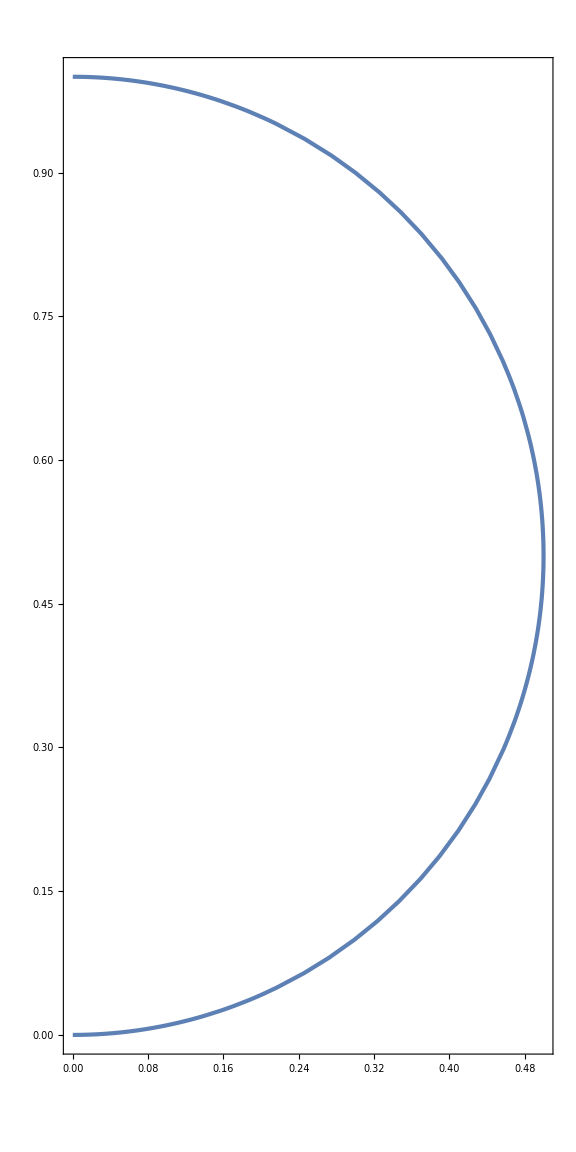

```mathematica
ParametricPlot[{Sin[θ]Cos[θ],Sin[θ]^2},{θ,0,π/2},AspectRatio->2]
```

```mathematica
Normal[Series[Cos[π+x],{x,0,2}]]
```

-1+x^2/2

```mathematica
Sin[θ]Cos[θ]//TrigReduce
```

1/2 Sin[2 θ]

```mathematica
Sin[θ]^2//TrigReduce
```

1/2 (1-Cos[2 θ])

```mathematica
metric//MatrixForm
```

(1/ξ | -r/(Phi ξ)
-r/(Phi ξ) | r^2/(Phi^2 ξ))

```mathematica
inversemetric=Simplify[Inverse[metric]]
```

Inverse::sing: Matrix {{1/ξ,-r/(Phi ξ)},{-r/(Phi ξ),r^2/(Phi^2 ξ)}} is singular.

Inverse[{{1/ξ,-r/(Phi ξ)},{-r/(Phi ξ),r^2/(Phi^2 ξ)}}]

```mathematica
inversemetric//MatrixForm
```

(2+(2 (h1^2+h2^2+h3^2+h4^2) ξ)/Mp^2 | 0 | 0 | 0
0 | 2+(2 (h1^2+h2^2+h3^2+h4^2) ξ)/Mp^2 | 0 | 0
0 | 0 | 2+(2 (h1^2+h2^2+h3^2+h4^2) ξ)/Mp^2 | 0
0 | 0 | 0 | 2+(2 (h1^2+h2^2+h3^2+h4^2) ξ)/Mp^2)

```mathematica
affine:=affine=Simplify[Table[(1/2)*Sum[(inversemetric[[i,s]])*(D[metric[[s,j]],coord[[k]]]+D[metric[[s,k]],coord[[j]]]-D[metric[[j,k]],coord[[s]]]),{s,1,n}],{i,1,n},{j,1,n},{k,1,n}]]
```

```mathematica
listaffine:=Table[If[UnsameQ[affine[[i,j,k]],0],{ToString[Γ[i,j,k]],affine[[i,j,k]]}],{i,1,n},{j,1,n},{k,1,j}]
```

```mathematica
TableForm[Partition[DeleteCases[Flatten[listaffine],Null],2],TableSpacing->{2,2}]
```

Γ[1, 1, 1] | -(h1 ξ)/(Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)
Γ[1, 2, 1] | -(h2 ξ)/(Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)
Γ[1, 2, 2] | (h1 ξ)/(Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)
Γ[1, 3, 1] | -(h3 ξ)/(Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)
Γ[1, 3, 3] | (h1 ξ)/(Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)
Γ[1, 4, 1] | -(h4 ξ)/(Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)
Γ[1, 4, 4] | (h1 ξ)/(Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)
Γ[2, 1, 1] | (h2 ξ)/(Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)
Γ[2, 2, 1] | -(h1 ξ)/(Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)
Γ[2, 2, 2] | -(h2 ξ)/(Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)
Γ[2, 3, 2] | -(h3 ξ)/(Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)
Γ[2, 3, 3] | (h2 ξ)/(Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)
Γ[2, 4, 2] | -(h4 ξ)/(Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)
Γ[2, 4, 4] | (h2 ξ)/(Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)
Γ[3, 1, 1] | (h3 ξ)/(Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)
Γ[3, 2, 2] | (h3 ξ)/(Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)
Γ[3, 3, 1] | -(h1 ξ)/(Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)
Γ[3, 3, 2] | -(h2 ξ)/(Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)
Γ[3, 3, 3] | -(h3 ξ)/(Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)
Γ[3, 4, 3] | -(h4 ξ)/(Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)
Γ[3, 4, 4] | (h3 ξ)/(Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)
Γ[4, 1, 1] | (h4 ξ)/(Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)
Γ[4, 2, 2] | (h4 ξ)/(Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)
Γ[4, 3, 3] | (h4 ξ)/(Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)
Γ[4, 4, 1] | -(h1 ξ)/(Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)
Γ[4, 4, 2] | -(h2 ξ)/(Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)
Γ[4, 4, 3] | -(h3 ξ)/(Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)
Γ[4, 4, 4] | -(h4 ξ)/(Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)

```mathematica
riemann:=riemann=Simplify[Table[D[affine[[i,j,l]],coord[[k]]]-D[affine[[i,j,k]],coord[[l]]]+Sum[affine[[s,j,l]]affine[[i,k,s]]-affine[[s,j,k]]affine[[i,l,s]],{s,1,n}],{i,1,n},{j,1,n},{k,1,n},{l,1,n}]]
```

```mathematica
listriemann:=Table[If[UnsameQ[riemann[[i,j,k,l]],0],{ToString[R[i,j,k,l]],riemann[[i,j,k,l]]}],{i,1,n},{j,1,n},{k,1,n},{l,1,k-1}]
```

```mathematica
TableForm[Partition[DeleteCases[Flatten[listriemann],Null],2],TableSpacing->{2,2}]
```

R[1, 2, 2, 1] | -(ξ (2 Mp^2+(h3^2+h4^2) ξ))/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[1, 2, 3, 1] | (h2 h3 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[1, 2, 3, 2] | -(h1 h3 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[1, 2, 4, 1] | (h2 h4 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[1, 2, 4, 2] | -(h1 h4 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[1, 3, 2, 1] | (h2 h3 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[1, 3, 3, 1] | -(ξ (2 Mp^2+(h2^2+h4^2) ξ))/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[1, 3, 3, 2] | (h1 h2 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[1, 3, 4, 1] | (h3 h4 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[1, 3, 4, 3] | -(h1 h4 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[1, 4, 2, 1] | (h2 h4 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[1, 4, 3, 1] | (h3 h4 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[1, 4, 4, 1] | -(ξ (2 Mp^2+(h2^2+h3^2) ξ))/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[1, 4, 4, 2] | (h1 h2 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[1, 4, 4, 3] | (h1 h3 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[2, 1, 2, 1] | (ξ (2 Mp^2+(h3^2+h4^2) ξ))/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[2, 1, 3, 1] | -(h2 h3 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[2, 1, 3, 2] | (h1 h3 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[2, 1, 4, 1] | -(h2 h4 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[2, 1, 4, 2] | (h1 h4 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[2, 3, 2, 1] | -(h1 h3 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[2, 3, 3, 1] | (h1 h2 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[2, 3, 3, 2] | -(ξ (2 Mp^2+(h1^2+h4^2) ξ))/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[2, 3, 4, 2] | (h3 h4 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[2, 3, 4, 3] | -(h2 h4 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[2, 4, 2, 1] | -(h1 h4 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[2, 4, 3, 2] | (h3 h4 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[2, 4, 4, 1] | (h1 h2 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[2, 4, 4, 2] | -(ξ (2 Mp^2+(h1^2+h3^2) ξ))/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[2, 4, 4, 3] | (h2 h3 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[3, 1, 2, 1] | -(h2 h3 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[3, 1, 3, 1] | (ξ (2 Mp^2+(h2^2+h4^2) ξ))/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[3, 1, 3, 2] | -(h1 h2 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[3, 1, 4, 1] | -(h3 h4 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[3, 1, 4, 3] | (h1 h4 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[3, 2, 2, 1] | (h1 h3 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[3, 2, 3, 1] | -(h1 h2 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[3, 2, 3, 2] | (ξ (2 Mp^2+(h1^2+h4^2) ξ))/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[3, 2, 4, 2] | -(h3 h4 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[3, 2, 4, 3] | (h2 h4 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[3, 4, 3, 1] | -(h1 h4 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[3, 4, 3, 2] | -(h2 h4 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[3, 4, 4, 1] | (h1 h3 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[3, 4, 4, 2] | (h2 h3 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[3, 4, 4, 3] | -(ξ (2 Mp^2+(h1^2+h2^2) ξ))/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[4, 1, 2, 1] | -(h2 h4 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[4, 1, 3, 1] | -(h3 h4 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[4, 1, 4, 1] | (ξ (2 Mp^2+(h2^2+h3^2) ξ))/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[4, 1, 4, 2] | -(h1 h2 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[4, 1, 4, 3] | -(h1 h3 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[4, 2, 2, 1] | (h1 h4 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[4, 2, 3, 2] | -(h3 h4 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[4, 2, 4, 1] | -(h1 h2 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[4, 2, 4, 2] | (ξ (2 Mp^2+(h1^2+h3^2) ξ))/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[4, 2, 4, 3] | -(h2 h3 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[4, 3, 3, 1] | (h1 h4 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[4, 3, 3, 2] | (h2 h4 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[4, 3, 4, 1] | -(h1 h3 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[4, 3, 4, 2] | -(h2 h3 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[4, 3, 4, 3] | (ξ (2 Mp^2+(h1^2+h2^2) ξ))/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)

```mathematica
ricci:=ricci=Simplify[Table[Sum[riemann[[i,j,i,l]],{i,1,n}],{j,1,n},{l,1,n}]]
```

```mathematica
listricci:=Table[If[UnsameQ[ricci[[j,l]],0],{ToString[R[j,l]],ricci[[j,l]]}],{j,1,n},{l,1,j}]
```

```mathematica
TableForm[Partition[DeleteCases[Flatten[listricci],Null],2],TableSpacing->{2,2}]
```

R[1, 1] | (2 ξ (3 Mp^2+(h2^2+h3^2+h4^2) ξ))/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[2, 1] | -(2 h1 h2 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[2, 2] | (2 ξ (3 Mp^2+(h1^2+h3^2+h4^2) ξ))/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[3, 1] | -(2 h1 h3 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[3, 2] | -(2 h2 h3 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[3, 3] | (2 ξ (3 Mp^2+(h1^2+h2^2+h4^2) ξ))/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[4, 1] | -(2 h1 h4 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[4, 2] | -(2 h2 h4 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[4, 3] | -(2 h3 h4 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[4, 4] | (2 ξ (3 Mp^2+(h1^2+h2^2+h3^2) ξ))/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)

```mathematica
scalar=Simplify[Sum[inversemetric[[i,j]]ricci[[i,j]],{i,1,n},{j,1,n}]]
```

(12 ξ (4 Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ))/(Mp^4+(h1^2+h2^2+h3^2+h4^2) Mp^2 ξ)

```mathematica
scalar/.{h1->0,h2->0,h3->0,h4->0}
```

(48 ξ)/Mp^2

### Higgs Palatini local conformal

```mathematica
Quit[]
```

```mathematica
rcoord={θ1,θ2,θ3,θ4};
drcoord={dθ1,dθ2,dθ3,dθ4};
nr=4;
```

```mathematica
S=Cos[θ1];
x1=Sin[θ1]Cos[θ2];
x2=Sin[θ1]Sin[θ2]Cos[θ3];
x3=Sin[θ1]Sin[θ2]Sin[θ3]Cos[θ4];
x4=Sin[θ1]Sin[θ2]Sin[θ3]Sin[θ4];
xcoord={S,x1,x2,x3,x4};
nx=5;
```

```mathematica
Sum[xcoord[[i]]^2,{i,nx}]//Simplify
```

1

```mathematica
dxcoord=Table[Sum[drcoord[[i]]D[xcoord[[j]], rcoord[[i]]],{i,nr}],{j,nx}]//Simplify
```

{-dθ1 Sin[θ1],dθ1 Cos[θ1] Cos[θ2]-dθ2 Sin[θ1] Sin[θ2],dθ2 Cos[θ2] Cos[θ3] Sin[θ1]+Sin[θ2] (dθ1 Cos[θ1] Cos[θ3]-dθ3 Sin[θ1] Sin[θ3]),dθ3 Cos[θ3] Cos[θ4] Sin[θ1] Sin[θ2]+Sin[θ3] (dθ2 Cos[θ2] Cos[θ4] Sin[θ1]+Sin[θ2] (dθ1 Cos[θ1] Cos[θ4]-dθ4 Sin[θ1] Sin[θ4])),dθ4 Cos[θ4] Sin[θ1] Sin[θ2] Sin[θ3]+(dθ3 Cos[θ3] Sin[θ1] Sin[θ2]+(dθ2 Cos[θ2] Sin[θ1]+dθ1 Cos[θ1] Sin[θ2]) Sin[θ3]) Sin[θ4]}

```mathematica
Collect[Sum[(dxcoord[[i]]-1/8 Q xcoord[[i]])^2,{i,nx}],Q,Simplify]
```

Q^2/64+1/32 (32 dθ1^2+16 dθ2^2+8 dθ3^2+4 dθ4^2-4 (4 dθ2^2+2 dθ3^2+dθ4^2) Cos[2 θ1]+2 (2 dθ3^2+dθ4^2) Cos[2 (θ1-θ2)]-8 dθ3^2 Cos[2 θ2]-4 dθ4^2 Cos[2 θ2]+4 dθ3^2 Cos[2 (θ1+θ2)]+2 dθ4^2 Cos[2 (θ1+θ2)]+2 dθ4^2 Cos[2 (θ1-θ3)]-dθ4^2 Cos[2 (θ1-θ2-θ3)]+2 dθ4^2 Cos[2 (θ2-θ3)]-dθ4^2 Cos[2 (θ1+θ2-θ3)]-4 dθ4^2 Cos[2 θ3]+2 dθ4^2 Cos[2 (θ1+θ3)]-dθ4^2 Cos[2 (θ1-θ2+θ3)]+2 dθ4^2 Cos[2 (θ2+θ3)]-dθ4^2 Cos[2 (θ1+θ2+θ3)])

```mathematica
coord={rho,Phi};
n=Length[coord]
```

2

```mathematica
metric=Table[If[i==n&&j==n,Sum[coord[[i]]^2,{i,n-1}],If[i==n,-coord[[j]],If[j==n,-coord[[i]],KroneckerDelta[i,j]]]],{i,n},{j,n}]
```

{{1,-rho},{-rho,rho^2}}

```mathematica
Eigensystem[metric]//Simplify
```

{{0,1+rho^2},{{rho,1},{-1/rho,1}}}

```mathematica
metric//MatrixForm
```

(1 | -rho
-rho | rho^2)

```mathematica
inversemetric=Simplify[Inverse[metric]]
```

{{-(h1^2-3 (h2^2+h3^2+h4^2))/(3 (h1^2+h2^2+h3^2+h4^2)),-(4 h1 h2)/(3 (h1^2+h2^2+h3^2+h4^2)),-(4 h1 h3)/(3 (h1^2+h2^2+h3^2+h4^2)),-(4 h1 h4)/(3 (h1^2+h2^2+h3^2+h4^2)),(2 h1)/(3 (h1^2+h2^2+h3^2+h4^2))},{-(4 h1 h2)/(3 (h1^2+h2^2+h3^2+h4^2)),(3 h1^2-h2^2+3 (h3^2+h4^2))/(3 (h1^2+h2^2+h3^2+h4^2)),-(4 h2 h3)/(3 (h1^2+h2^2+h3^2+h4^2)),-(4 h2 h4)/(3 (h1^2+h2^2+h3^2+h4^2)),(2 h2)/(3 (h1^2+h2^2+h3^2+h4^2))},{-(4 h1 h3)/(3 (h1^2+h2^2+h3^2+h4^2)),-(4 h2 h3)/(3 (h1^2+h2^2+h3^2+h4^2)),(3 h1^2+3 h2^2-h3^2+3 h4^2)/(3 (h1^2+h2^2+h3^2+h4^2)),-(4 h3 h4)/(3 (h1^2+h2^2+h3^2+h4^2)),(2 h3)/(3 (h1^2+h2^2+h3^2+h4^2))},{-(4 h1 h4)/(3 (h1^2+h2^2+h3^2+h4^2)),-(4 h2 h4)/(3 (h1^2+h2^2+h3^2+h4^2)),-(4 h3 h4)/(3 (h1^2+h2^2+h3^2+h4^2)),(3 h1^2+3 h2^2+3 h3^2-h4^2)/(3 (h1^2+h2^2+h3^2+h4^2)),(2 h4)/(3 (h1^2+h2^2+h3^2+h4^2))},{(2 h1)/(3 (h1^2+h2^2+h3^2+h4^2)),(2 h2)/(3 (h1^2+h2^2+h3^2+h4^2)),(2 h3)/(3 (h1^2+h2^2+h3^2+h4^2)),(2 h4)/(3 (h1^2+h2^2+h3^2+h4^2)),-1/(3 (h1^2+h2^2+h3^2+h4^2))}}

```mathematica
inversemetric//MatrixForm
```

(-(h1^2-3 (h2^2+h3^2+h4^2))/(3 (h1^2+h2^2+h3^2+h4^2)) | -(4 h1 h2)/(3 (h1^2+h2^2+h3^2+h4^2)) | -(4 h1 h3)/(3 (h1^2+h2^2+h3^2+h4^2)) | -(4 h1 h4)/(3 (h1^2+h2^2+h3^2+h4^2)) | (2 h1)/(3 (h1^2+h2^2+h3^2+h4^2))
-(4 h1 h2)/(3 (h1^2+h2^2+h3^2+h4^2)) | (3 h1^2-h2^2+3 (h3^2+h4^2))/(3 (h1^2+h2^2+h3^2+h4^2)) | -(4 h2 h3)/(3 (h1^2+h2^2+h3^2+h4^2)) | -(4 h2 h4)/(3 (h1^2+h2^2+h3^2+h4^2)) | (2 h2)/(3 (h1^2+h2^2+h3^2+h4^2))
-(4 h1 h3)/(3 (h1^2+h2^2+h3^2+h4^2)) | -(4 h2 h3)/(3 (h1^2+h2^2+h3^2+h4^2)) | (3 h1^2+3 h2^2-h3^2+3 h4^2)/(3 (h1^2+h2^2+h3^2+h4^2)) | -(4 h3 h4)/(3 (h1^2+h2^2+h3^2+h4^2)) | (2 h3)/(3 (h1^2+h2^2+h3^2+h4^2))
-(4 h1 h4)/(3 (h1^2+h2^2+h3^2+h4^2)) | -(4 h2 h4)/(3 (h1^2+h2^2+h3^2+h4^2)) | -(4 h3 h4)/(3 (h1^2+h2^2+h3^2+h4^2)) | (3 h1^2+3 h2^2+3 h3^2-h4^2)/(3 (h1^2+h2^2+h3^2+h4^2)) | (2 h4)/(3 (h1^2+h2^2+h3^2+h4^2))
(2 h1)/(3 (h1^2+h2^2+h3^2+h4^2)) | (2 h2)/(3 (h1^2+h2^2+h3^2+h4^2)) | (2 h3)/(3 (h1^2+h2^2+h3^2+h4^2)) | (2 h4)/(3 (h1^2+h2^2+h3^2+h4^2)) | -1/(3 (h1^2+h2^2+h3^2+h4^2)))

```mathematica
affine:=affine=Simplify[Table[(1/2)*Sum[(inversemetric[[i,s]])*(D[metric[[s,j]],coord[[k]]]+D[metric[[s,k]],coord[[j]]]-D[metric[[j,k]],coord[[s]]]),{s,1,n}],{i,1,n},{j,1,n},{k,1,n}]]
```

```mathematica
listaffine:=Table[If[UnsameQ[affine[[i,j,k]],0],{ToString[Γ[i,j,k]],affine[[i,j,k]]}],{i,1,n},{j,1,n},{k,1,j}]
```

```mathematica
TableForm[Partition[DeleteCases[Flatten[listaffine],Null],2],TableSpacing->{2,2}]
```

Γ[1, 1, 1] | (4 h1)/(3 (h1^2+h2^2+h3^2+h4^2))
Γ[1, 2, 2] | (4 h1)/(3 (h1^2+h2^2+h3^2+h4^2))
Γ[1, 3, 3] | (4 h1)/(3 (h1^2+h2^2+h3^2+h4^2))
Γ[1, 4, 4] | (4 h1)/(3 (h1^2+h2^2+h3^2+h4^2))
Γ[1, 5, 1] | (2 h1^2)/(3 (h1^2+h2^2+h3^2+h4^2))
Γ[1, 5, 2] | (2 h1 h2)/(3 (h1^2+h2^2+h3^2+h4^2))
Γ[1, 5, 3] | (2 h1 h3)/(3 (h1^2+h2^2+h3^2+h4^2))
Γ[1, 5, 4] | (2 h1 h4)/(3 (h1^2+h2^2+h3^2+h4^2))
Γ[1, 5, 5] | h1/3
Γ[2, 1, 1] | (4 h2)/(3 (h1^2+h2^2+h3^2+h4^2))
Γ[2, 2, 2] | (4 h2)/(3 (h1^2+h2^2+h3^2+h4^2))
Γ[2, 3, 3] | (4 h2)/(3 (h1^2+h2^2+h3^2+h4^2))
Γ[2, 4, 4] | (4 h2)/(3 (h1^2+h2^2+h3^2+h4^2))
Γ[2, 5, 1] | (2 h1 h2)/(3 (h1^2+h2^2+h3^2+h4^2))
Γ[2, 5, 2] | (2 h2^2)/(3 (h1^2+h2^2+h3^2+h4^2))
Γ[2, 5, 3] | (2 h2 h3)/(3 (h1^2+h2^2+h3^2+h4^2))
Γ[2, 5, 4] | (2 h2 h4)/(3 (h1^2+h2^2+h3^2+h4^2))
Γ[2, 5, 5] | h2/3
Γ[3, 1, 1] | (4 h3)/(3 (h1^2+h2^2+h3^2+h4^2))
Γ[3, 2, 2] | (4 h3)/(3 (h1^2+h2^2+h3^2+h4^2))
Γ[3, 3, 3] | (4 h3)/(3 (h1^2+h2^2+h3^2+h4^2))
Γ[3, 4, 4] | (4 h3)/(3 (h1^2+h2^2+h3^2+h4^2))
Γ[3, 5, 1] | (2 h1 h3)/(3 (h1^2+h2^2+h3^2+h4^2))
Γ[3, 5, 2] | (2 h2 h3)/(3 (h1^2+h2^2+h3^2+h4^2))
Γ[3, 5, 3] | (2 h3^2)/(3 (h1^2+h2^2+h3^2+h4^2))
Γ[3, 5, 4] | (2 h3 h4)/(3 (h1^2+h2^2+h3^2+h4^2))
Γ[3, 5, 5] | h3/3
Γ[4, 1, 1] | (4 h4)/(3 (h1^2+h2^2+h3^2+h4^2))
Γ[4, 2, 2] | (4 h4)/(3 (h1^2+h2^2+h3^2+h4^2))
Γ[4, 3, 3] | (4 h4)/(3 (h1^2+h2^2+h3^2+h4^2))
Γ[4, 4, 4] | (4 h4)/(3 (h1^2+h2^2+h3^2+h4^2))
Γ[4, 5, 1] | (2 h1 h4)/(3 (h1^2+h2^2+h3^2+h4^2))
Γ[4, 5, 2] | (2 h2 h4)/(3 (h1^2+h2^2+h3^2+h4^2))
Γ[4, 5, 3] | (2 h3 h4)/(3 (h1^2+h2^2+h3^2+h4^2))
Γ[4, 5, 4] | (2 h4^2)/(3 (h1^2+h2^2+h3^2+h4^2))
Γ[4, 5, 5] | h4/3
Γ[5, 1, 1] | -2/(3 (h1^2+h2^2+h3^2+h4^2))
Γ[5, 2, 2] | -2/(3 (h1^2+h2^2+h3^2+h4^2))
Γ[5, 3, 3] | -2/(3 (h1^2+h2^2+h3^2+h4^2))
Γ[5, 4, 4] | -2/(3 (h1^2+h2^2+h3^2+h4^2))
Γ[5, 5, 1] | -h1/(3 (h1^2+h2^2+h3^2+h4^2))
Γ[5, 5, 2] | -h2/(3 (h1^2+h2^2+h3^2+h4^2))
Γ[5, 5, 3] | -h3/(3 (h1^2+h2^2+h3^2+h4^2))
Γ[5, 5, 4] | -h4/(3 (h1^2+h2^2+h3^2+h4^2))
Γ[5, 5, 5] | -2/3

```mathematica
riemann:=riemann=Simplify[Table[D[affine[[i,j,l]],coord[[k]]]-D[affine[[i,j,k]],coord[[l]]]+Sum[affine[[s,j,l]]affine[[i,k,s]]-affine[[s,j,k]]affine[[i,l,s]],{s,1,n}],{i,1,n},{j,1,n},{k,1,n},{l,1,n}]]
```

```mathematica
listriemann:=Table[If[UnsameQ[riemann[[i,j,k,l]],0],{ToString[R[i,j,k,l]],riemann[[i,j,k,l]]}],{i,1,n},{j,1,n},{k,1,n},{l,1,k-1}]
```

```mathematica
TableForm[Partition[DeleteCases[Flatten[listriemann],Null],2],TableSpacing->{2,2}]
```

R[1, 1, 2, 1] | -(4 h1 h2)/(3 (h1^2+h2^2+h3^2+h4^2)^2)
R[1, 1, 3, 1] | -(4 h1 h3)/(3 (h1^2+h2^2+h3^2+h4^2)^2)
R[1, 1, 4, 1] | -(4 h1 h4)/(3 (h1^2+h2^2+h3^2+h4^2)^2)
R[1, 1, 5, 1] | -(2 h1 (h2^2+h3^2+h4^2))/(3 (h1^2+h2^2+h3^2+h4^2)^2)
R[1, 1, 5, 2] | (2 h1^2 h2)/(3 (h1^2+h2^2+h3^2+h4^2)^2)
R[1, 1, 5, 3] | (2 h1^2 h3)/(3 (h1^2+h2^2+h3^2+h4^2)^2)
R[1, 1, 5, 4] | (2 h1^2 h4)/(3 (h1^2+h2^2+h3^2+h4^2)^2)
R[1, 2, 2, 1] | -(4 (h2^2+h3^2+h4^2))/(3 (h1^2+h2^2+h3^2+h4^2)^2)
R[1, 2, 3, 2] | -(4 h1 h3)/(3 (h1^2+h2^2+h3^2+h4^2)^2)
R[1, 2, 4, 2] | -(4 h1 h4)/(3 (h1^2+h2^2+h3^2+h4^2)^2)
R[1, 2, 5, 1] | -(2 h2 (h2^2+h3^2+h4^2))/(3 (h1^2+h2^2+h3^2+h4^2)^2)
R[1, 2, 5, 2] | (2 h1 h2^2)/(3 (h1^2+h2^2+h3^2+h4^2)^2)
R[1, 2, 5, 3] | (2 h1 h2 h3)/(3 (h1^2+h2^2+h3^2+h4^2)^2)
R[1, 2, 5, 4] | (2 h1 h2 h4)/(3 (h1^2+h2^2+h3^2+h4^2)^2)
R[1, 3, 3, 1] | -(4 (h2^2+h3^2+h4^2))/(3 (h1^2+h2^2+h3^2+h4^2)^2)
R[1, 3, 3, 2] | (4 h1 h2)/(3 (h1^2+h2^2+h3^2+h4^2)^2)
R[1, 3, 4, 3] | -(4 h1 h4)/(3 (h1^2+h2^2+h3^2+h4^2)^2)
R[1, 3, 5, 1] | -(2 h3 (h2^2+h3^2+h4^2))/(3 (h1^2+h2^2+h3^2+h4^2)^2)
R[1, 3, 5, 2] | (2 h1 h2 h3)/(3 (h1^2+h2^2+h3^2+h4^2)^2)
R[1, 3, 5, 3] | (2 h1 h3^2)/(3 (h1^2+h2^2+h3^2+h4^2)^2)
R[1, 3, 5, 4] | (2 h1 h3 h4)/(3 (h1^2+h2^2+h3^2+h4^2)^2)
R[1, 4, 4, 1] | -(4 (h2^2+h3^2+h4^2))/(3 (h1^2+h2^2+h3^2+h4^2)^2)
R[1, 4, 4, 2] | (4 h1 h2)/(3 (h1^2+h2^2+h3^2+h4^2)^2)
R[1, 4, 4, 3] | (4 h1 h3)/(3 (h1^2+h2^2+h3^2+h4^2)^2)
R[1, 4, 5, 1] | -(2 h4 (h2^2+h3^2+h4^2))/(3 (h1^2+h2^2+h3^2+h4^2)^2)
R[1, 4, 5, 2] | (2 h1 h2 h4)/(3 (h1^2+h2^2+h3^2+h4^2)^2)
R[1, 4, 5, 3] | (2 h1 h3 h4)/(3 (h1^2+h2^2+h3^2+h4^2)^2)
R[1, 4, 5, 4] | (2 h1 h4^2)/(3 (h1^2+h2^2+h3^2+h4^2)^2)
R[1, 5, 2, 1] | -(2 h2)/(3 (h1^2+h2^2+h3^2+h4^2))
R[1, 5, 3, 1] | -(2 h3)/(3 (h1^2+h2^2+h3^2+h4^2))
R[1, 5, 4, 1] | -(2 h4)/(3 (h1^2+h2^2+h3^2+h4^2))
R[1, 5, 5, 1] | -(h2^2+h3^2+h4^2)/(3 (h1^2+h2^2+h3^2+h4^2))
R[1, 5, 5, 2] | (h1 h2)/(3 (h1^2+h2^2+h3^2+h4^2))
R[1, 5, 5, 3] | (h1 h3)/(3 (h1^2+h2^2+h3^2+h4^2))
R[1, 5, 5, 4] | (h1 h4)/(3 (h1^2+h2^2+h3^2+h4^2))
R[2, 1, 2, 1] | (4 (h1^2+h3^2+h4^2))/(3 (h1^2+h2^2+h3^2+h4^2)^2)
R[2, 1, 3, 1] | -(4 h2 h3)/(3 (h1^2+h2^2+h3^2+h4^2)^2)
R[2, 1, 4, 1] | -(4 h2 h4)/(3 (h1^2+h2^2+h3^2+h4^2)^2)
R[2, 1, 5, 1] | (2 h1^2 h2)/(3 (h1^2+h2^2+h3^2+h4^2)^2)
R[2, 1, 5, 2] | -(2 h1 (h1^2+h3^2+h4^2))/(3 (h1^2+h2^2+h3^2+h4^2)^2)
R[2, 1, 5, 3] | (2 h1 h2 h3)/(3 (h1^2+h2^2+h3^2+h4^2)^2)
R[2, 1, 5, 4] | (2 h1 h2 h4)/(3 (h1^2+h2^2+h3^2+h4^2)^2)
R[2, 2, 2, 1] | (4 h1 h2)/(3 (h1^2+h2^2+h3^2+h4^2)^2)
R[2, 2, 3, 2] | -(4 h2 h3)/(3 (h1^2+h2^2+h3^2+h4^2)^2)
R[2, 2, 4, 2] | -(4 h2 h4)/(3 (h1^2+h2^2+h3^2+h4^2)^2)
R[2, 2, 5, 1] | (2 h1 h2^2)/(3 (h1^2+h2^2+h3^2+h4^2)^2)
R[2, 2, 5, 2] | -(2 h2 (h1^2+h3^2+h4^2))/(3 (h1^2+h2^2+h3^2+h4^2)^2)
R[2, 2, 5, 3] | (2 h2^2 h3)/(3 (h1^2+h2^2+h3^2+h4^2)^2)
R[2, 2, 5, 4] | (2 h2^2 h4)/(3 (h1^2+h2^2+h3^2+h4^2)^2)
R[2, 3, 3, 1] | (4 h1 h2)/(3 (h1^2+h2^2+h3^2+h4^2)^2)
R[2, 3, 3, 2] | -(4 (h1^2+h3^2+h4^2))/(3 (h1^2+h2^2+h3^2+h4^2)^2)
R[2, 3, 4, 3] | -(4 h2 h4)/(3 (h1^2+h2^2+h3^2+h4^2)^2)
R[2, 3, 5, 1] | (2 h1 h2 h3)/(3 (h1^2+h2^2+h3^2+h4^2)^2)
R[2, 3, 5, 2] | -(2 h3 (h1^2+h3^2+h4^2))/(3 (h1^2+h2^2+h3^2+h4^2)^2)
R[2, 3, 5, 3] | (2 h2 h3^2)/(3 (h1^2+h2^2+h3^2+h4^2)^2)
R[2, 3, 5, 4] | (2 h2 h3 h4)/(3 (h1^2+h2^2+h3^2+h4^2)^2)
R[2, 4, 4, 1] | (4 h1 h2)/(3 (h1^2+h2^2+h3^2+h4^2)^2)
R[2, 4, 4, 2] | -(4 (h1^2+h3^2+h4^2))/(3 (h1^2+h2^2+h3^2+h4^2)^2)
R[2, 4, 4, 3] | (4 h2 h3)/(3 (h1^2+h2^2+h3^2+h4^2)^2)
R[2, 4, 5, 1] | (2 h1 h2 h4)/(3 (h1^2+h2^2+h3^2+h4^2)^2)
R[2, 4, 5, 2] | -(2 h4 (h1^2+h3^2+h4^2))/(3 (h1^2+h2^2+h3^2+h4^2)^2)
R[2, 4, 5, 3] | (2 h2 h3 h4)/(3 (h1^2+h2^2+h3^2+h4^2)^2)
R[2, 4, 5, 4] | (2 h2 h4^2)/(3 (h1^2+h2^2+h3^2+h4^2)^2)
R[2, 5, 2, 1] | (2 h1)/(3 (h1^2+h2^2+h3^2+h4^2))
R[2, 5, 3, 2] | -(2 h3)/(3 (h1^2+h2^2+h3^2+h4^2))
R[2, 5, 4, 2] | -(2 h4)/(3 (h1^2+h2^2+h3^2+h4^2))
R[2, 5, 5, 1] | (h1 h2)/(3 (h1^2+h2^2+h3^2+h4^2))
R[2, 5, 5, 2] | -(h1^2+h3^2+h4^2)/(3 (h1^2+h2^2+h3^2+h4^2))
R[2, 5, 5, 3] | (h2 h3)/(3 (h1^2+h2^2+h3^2+h4^2))
R[2, 5, 5, 4] | (h2 h4)/(3 (h1^2+h2^2+h3^2+h4^2))
R[3, 1, 2, 1] | -(4 h2 h3)/(3 (h1^2+h2^2+h3^2+h4^2)^2)
R[3, 1, 3, 1] | (4 (h1^2+h2^2+h4^2))/(3 (h1^2+h2^2+h3^2+h4^2)^2)
R[3, 1, 4, 1] | -(4 h3 h4)/(3 (h1^2+h2^2+h3^2+h4^2)^2)
R[3, 1, 5, 1] | (2 h1^2 h3)/(3 (h1^2+h2^2+h3^2+h4^2)^2)
R[3, 1, 5, 2] | (2 h1 h2 h3)/(3 (h1^2+h2^2+h3^2+h4^2)^2)
R[3, 1, 5, 3] | -(2 h1 (h1^2+h2^2+h4^2))/(3 (h1^2+h2^2+h3^2+h4^2)^2)
R[3, 1, 5, 4] | (2 h1 h3 h4)/(3 (h1^2+h2^2+h3^2+h4^2)^2)
R[3, 2, 2, 1] | (4 h1 h3)/(3 (h1^2+h2^2+h3^2+h4^2)^2)
R[3, 2, 3, 2] | (4 (h1^2+h2^2+h4^2))/(3 (h1^2+h2^2+h3^2+h4^2)^2)
R[3, 2, 4, 2] | -(4 h3 h4)/(3 (h1^2+h2^2+h3^2+h4^2)^2)
R[3, 2, 5, 1] | (2 h1 h2 h3)/(3 (h1^2+h2^2+h3^2+h4^2)^2)
R[3, 2, 5, 2] | (2 h2^2 h3)/(3 (h1^2+h2^2+h3^2+h4^2)^2)
R[3, 2, 5, 3] | -(2 h2 (h1^2+h2^2+h4^2))/(3 (h1^2+h2^2+h3^2+h4^2)^2)
R[3, 2, 5, 4] | (2 h2 h3 h4)/(3 (h1^2+h2^2+h3^2+h4^2)^2)
R[3, 3, 3, 1] | (4 h1 h3)/(3 (h1^2+h2^2+h3^2+h4^2)^2)
R[3, 3, 3, 2] | (4 h2 h3)/(3 (h1^2+h2^2+h3^2+h4^2)^2)
R[3, 3, 4, 3] | -(4 h3 h4)/(3 (h1^2+h2^2+h3^2+h4^2)^2)
R[3, 3, 5, 1] | (2 h1 h3^2)/(3 (h1^2+h2^2+h3^2+h4^2)^2)
R[3, 3, 5, 2] | (2 h2 h3^2)/(3 (h1^2+h2^2+h3^2+h4^2)^2)
R[3, 3, 5, 3] | -(2 h3 (h1^2+h2^2+h4^2))/(3 (h1^2+h2^2+h3^2+h4^2)^2)
R[3, 3, 5, 4] | (2 h3^2 h4)/(3 (h1^2+h2^2+h3^2+h4^2)^2)
R[3, 4, 4, 1] | (4 h1 h3)/(3 (h1^2+h2^2+h3^2+h4^2)^2)
R[3, 4, 4, 2] | (4 h2 h3)/(3 (h1^2+h2^2+h3^2+h4^2)^2)
R[3, 4, 4, 3] | -(4 (h1^2+h2^2+h4^2))/(3 (h1^2+h2^2+h3^2+h4^2)^2)
R[3, 4, 5, 1] | (2 h1 h3 h4)/(3 (h1^2+h2^2+h3^2+h4^2)^2)
R[3, 4, 5, 2] | (2 h2 h3 h4)/(3 (h1^2+h2^2+h3^2+h4^2)^2)
R[3, 4, 5, 3] | -(2 h4 (h1^2+h2^2+h4^2))/(3 (h1^2+h2^2+h3^2+h4^2)^2)
R[3, 4, 5, 4] | (2 h3 h4^2)/(3 (h1^2+h2^2+h3^2+h4^2)^2)
R[3, 5, 3, 1] | (2 h1)/(3 (h1^2+h2^2+h3^2+h4^2))
R[3, 5, 3, 2] | (2 h2)/(3 (h1^2+h2^2+h3^2+h4^2))
R[3, 5, 4, 3] | -(2 h4)/(3 (h1^2+h2^2+h3^2+h4^2))
R[3, 5, 5, 1] | (h1 h3)/(3 (h1^2+h2^2+h3^2+h4^2))
R[3, 5, 5, 2] | (h2 h3)/(3 (h1^2+h2^2+h3^2+h4^2))
R[3, 5, 5, 3] | -(h1^2+h2^2+h4^2)/(3 (h1^2+h2^2+h3^2+h4^2))
R[3, 5, 5, 4] | (h3 h4)/(3 (h1^2+h2^2+h3^2+h4^2))
R[4, 1, 2, 1] | -(4 h2 h4)/(3 (h1^2+h2^2+h3^2+h4^2)^2)
R[4, 1, 3, 1] | -(4 h3 h4)/(3 (h1^2+h2^2+h3^2+h4^2)^2)
R[4, 1, 4, 1] | (4 (h1^2+h2^2+h3^2))/(3 (h1^2+h2^2+h3^2+h4^2)^2)
R[4, 1, 5, 1] | (2 h1^2 h4)/(3 (h1^2+h2^2+h3^2+h4^2)^2)
R[4, 1, 5, 2] | (2 h1 h2 h4)/(3 (h1^2+h2^2+h3^2+h4^2)^2)
R[4, 1, 5, 3] | (2 h1 h3 h4)/(3 (h1^2+h2^2+h3^2+h4^2)^2)
R[4, 1, 5, 4] | -(2 h1 (h1^2+h2^2+h3^2))/(3 (h1^2+h2^2+h3^2+h4^2)^2)
R[4, 2, 2, 1] | (4 h1 h4)/(3 (h1^2+h2^2+h3^2+h4^2)^2)
R[4, 2, 3, 2] | -(4 h3 h4)/(3 (h1^2+h2^2+h3^2+h4^2)^2)
R[4, 2, 4, 2] | (4 (h1^2+h2^2+h3^2))/(3 (h1^2+h2^2+h3^2+h4^2)^2)
R[4, 2, 5, 1] | (2 h1 h2 h4)/(3 (h1^2+h2^2+h3^2+h4^2)^2)
R[4, 2, 5, 2] | (2 h2^2 h4)/(3 (h1^2+h2^2+h3^2+h4^2)^2)
R[4, 2, 5, 3] | (2 h2 h3 h4)/(3 (h1^2+h2^2+h3^2+h4^2)^2)
R[4, 2, 5, 4] | -(2 h2 (h1^2+h2^2+h3^2))/(3 (h1^2+h2^2+h3^2+h4^2)^2)
R[4, 3, 3, 1] | (4 h1 h4)/(3 (h1^2+h2^2+h3^2+h4^2)^2)
R[4, 3, 3, 2] | (4 h2 h4)/(3 (h1^2+h2^2+h3^2+h4^2)^2)
R[4, 3, 4, 3] | (4 (h1^2+h2^2+h3^2))/(3 (h1^2+h2^2+h3^2+h4^2)^2)
R[4, 3, 5, 1] | (2 h1 h3 h4)/(3 (h1^2+h2^2+h3^2+h4^2)^2)
R[4, 3, 5, 2] | (2 h2 h3 h4)/(3 (h1^2+h2^2+h3^2+h4^2)^2)
R[4, 3, 5, 3] | (2 h3^2 h4)/(3 (h1^2+h2^2+h3^2+h4^2)^2)
R[4, 3, 5, 4] | -(2 h3 (h1^2+h2^2+h3^2))/(3 (h1^2+h2^2+h3^2+h4^2)^2)
R[4, 4, 4, 1] | (4 h1 h4)/(3 (h1^2+h2^2+h3^2+h4^2)^2)
R[4, 4, 4, 2] | (4 h2 h4)/(3 (h1^2+h2^2+h3^2+h4^2)^2)
R[4, 4, 4, 3] | (4 h3 h4)/(3 (h1^2+h2^2+h3^2+h4^2)^2)
R[4, 4, 5, 1] | (2 h1 h4^2)/(3 (h1^2+h2^2+h3^2+h4^2)^2)
R[4, 4, 5, 2] | (2 h2 h4^2)/(3 (h1^2+h2^2+h3^2+h4^2)^2)
R[4, 4, 5, 3] | (2 h3 h4^2)/(3 (h1^2+h2^2+h3^2+h4^2)^2)
R[4, 4, 5, 4] | -(2 (h1^2+h2^2+h3^2) h4)/(3 (h1^2+h2^2+h3^2+h4^2)^2)
R[4, 5, 4, 1] | (2 h1)/(3 (h1^2+h2^2+h3^2+h4^2))
R[4, 5, 4, 2] | (2 h2)/(3 (h1^2+h2^2+h3^2+h4^2))
R[4, 5, 4, 3] | (2 h3)/(3 (h1^2+h2^2+h3^2+h4^2))
R[4, 5, 5, 1] | (h1 h4)/(3 (h1^2+h2^2+h3^2+h4^2))
R[4, 5, 5, 2] | (h2 h4)/(3 (h1^2+h2^2+h3^2+h4^2))
R[4, 5, 5, 3] | (h3 h4)/(3 (h1^2+h2^2+h3^2+h4^2))
R[4, 5, 5, 4] | -(h1^2+h2^2+h3^2)/(3 (h1^2+h2^2+h3^2+h4^2))
R[5, 1, 2, 1] | (2 h2)/(3 (h1^2+h2^2+h3^2+h4^2)^2)
R[5, 1, 3, 1] | (2 h3)/(3 (h1^2+h2^2+h3^2+h4^2)^2)
R[5, 1, 4, 1] | (2 h4)/(3 (h1^2+h2^2+h3^2+h4^2)^2)
R[5, 1, 5, 1] | (h2^2+h3^2+h4^2)/(3 (h1^2+h2^2+h3^2+h4^2)^2)
R[5, 1, 5, 2] | -(h1 h2)/(3 (h1^2+h2^2+h3^2+h4^2)^2)
R[5, 1, 5, 3] | -(h1 h3)/(3 (h1^2+h2^2+h3^2+h4^2)^2)
R[5, 1, 5, 4] | -(h1 h4)/(3 (h1^2+h2^2+h3^2+h4^2)^2)
R[5, 2, 2, 1] | -(2 h1)/(3 (h1^2+h2^2+h3^2+h4^2)^2)
R[5, 2, 3, 2] | (2 h3)/(3 (h1^2+h2^2+h3^2+h4^2)^2)
R[5, 2, 4, 2] | (2 h4)/(3 (h1^2+h2^2+h3^2+h4^2)^2)
R[5, 2, 5, 1] | -(h1 h2)/(3 (h1^2+h2^2+h3^2+h4^2)^2)
R[5, 2, 5, 2] | (h1^2+h3^2+h4^2)/(3 (h1^2+h2^2+h3^2+h4^2)^2)
R[5, 2, 5, 3] | -(h2 h3)/(3 (h1^2+h2^2+h3^2+h4^2)^2)
R[5, 2, 5, 4] | -(h2 h4)/(3 (h1^2+h2^2+h3^2+h4^2)^2)
R[5, 3, 3, 1] | -(2 h1)/(3 (h1^2+h2^2+h3^2+h4^2)^2)
R[5, 3, 3, 2] | -(2 h2)/(3 (h1^2+h2^2+h3^2+h4^2)^2)
R[5, 3, 4, 3] | (2 h4)/(3 (h1^2+h2^2+h3^2+h4^2)^2)
R[5, 3, 5, 1] | -(h1 h3)/(3 (h1^2+h2^2+h3^2+h4^2)^2)
R[5, 3, 5, 2] | -(h2 h3)/(3 (h1^2+h2^2+h3^2+h4^2)^2)
R[5, 3, 5, 3] | (h1^2+h2^2+h4^2)/(3 (h1^2+h2^2+h3^2+h4^2)^2)
R[5, 3, 5, 4] | -(h3 h4)/(3 (h1^2+h2^2+h3^2+h4^2)^2)
R[5, 4, 4, 1] | -(2 h1)/(3 (h1^2+h2^2+h3^2+h4^2)^2)
R[5, 4, 4, 2] | -(2 h2)/(3 (h1^2+h2^2+h3^2+h4^2)^2)
R[5, 4, 4, 3] | -(2 h3)/(3 (h1^2+h2^2+h3^2+h4^2)^2)
R[5, 4, 5, 1] | -(h1 h4)/(3 (h1^2+h2^2+h3^2+h4^2)^2)
R[5, 4, 5, 2] | -(h2 h4)/(3 (h1^2+h2^2+h3^2+h4^2)^2)
R[5, 4, 5, 3] | -(h3 h4)/(3 (h1^2+h2^2+h3^2+h4^2)^2)
R[5, 4, 5, 4] | (h1^2+h2^2+h3^2)/(3 (h1^2+h2^2+h3^2+h4^2)^2)

```mathematica
ricci:=ricci=Simplify[Table[Sum[riemann[[i,j,i,l]],{i,1,n}],{j,1,n},{l,1,n}]]
```

```mathematica
listricci:=Table[If[UnsameQ[ricci[[j,l]],0],{ToString[R[j,l]],ricci[[j,l]]}],{j,1,n},{l,1,j}]
```

```mathematica
TableForm[Partition[DeleteCases[Flatten[listricci],Null],2],TableSpacing->{2,2}]
```

R[1, 1] | (4 h1^2+3 (h2^2+h3^2+h4^2))/((h1^2+h2^2+h3^2+h4^2)^2)
R[2, 1] | (h1 h2)/((h1^2+h2^2+h3^2+h4^2)^2)
R[2, 2] | (3 h1^2+4 h2^2+3 (h3^2+h4^2))/((h1^2+h2^2+h3^2+h4^2)^2)
R[3, 1] | (h1 h3)/((h1^2+h2^2+h3^2+h4^2)^2)
R[3, 2] | (h2 h3)/((h1^2+h2^2+h3^2+h4^2)^2)
R[3, 3] | (3 h1^2+3 h2^2+4 h3^2+3 h4^2)/((h1^2+h2^2+h3^2+h4^2)^2)
R[4, 1] | (h1 h4)/((h1^2+h2^2+h3^2+h4^2)^2)
R[4, 2] | (h2 h4)/((h1^2+h2^2+h3^2+h4^2)^2)
R[4, 3] | (h3 h4)/((h1^2+h2^2+h3^2+h4^2)^2)
R[4, 4] | (3 h1^2+3 h2^2+3 h3^2+4 h4^2)/((h1^2+h2^2+h3^2+h4^2)^2)
R[5, 1] | (2 h1)/(h1^2+h2^2+h3^2+h4^2)
R[5, 2] | (2 h2)/(h1^2+h2^2+h3^2+h4^2)
R[5, 3] | (2 h3)/(h1^2+h2^2+h3^2+h4^2)
R[5, 4] | (2 h4)/(h1^2+h2^2+h3^2+h4^2)
R[5, 5] | 1

```mathematica
scalar=Simplify[Sum[inversemetric[[i,j]]ricci[[i,j]],{i,1,n},{j,1,n}]]
```

10/(h1^2+h2^2+h3^2+h4^2)